```mathematica
DiamondGraph[n_]:=With[
{max=2+n},
Graph[
Range[max]
,
DeleteDuplicates[
Join[
Flatten[Table[{1<->i,2<->i},{i,3,max}]],
Flatten[Table[{i<->i+1,2<->i},{i,3,max-1}]]
]
],
VertexCoordinates->Join[{{(n+1)/2,2},{(n+1)/2,-2}},Table[{i-2,0},{i,3,max}]]
]
]
```

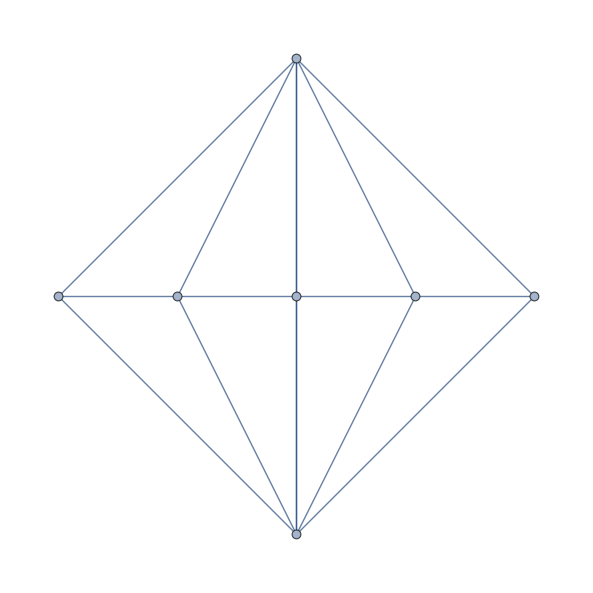

```mathematica
Graph[EdgeAdd[DiamondGraph[5],1<->2],GraphLayout->"PlanarEmbedding"]
```

```mathematica
ReadGraphHighlight[n_]:=Block[
{f, l},
f=OpenRead["d:\\grofs\\diamonds\\"<>ToString[n]<>".diamond"];
l=ReadList[f,"String",1,RecordSeparators->{"\r\n","\r" }];
Close[f];
l="{"<>l[[1]]<>"}";
l=ReadList[StringToStream[l],Expression,1];
Return[l[[1]]]
]
```

```mathematica
ReadGraphHighlight[58696]
```

{4<->9,6<->9,6<->8,8<->10}

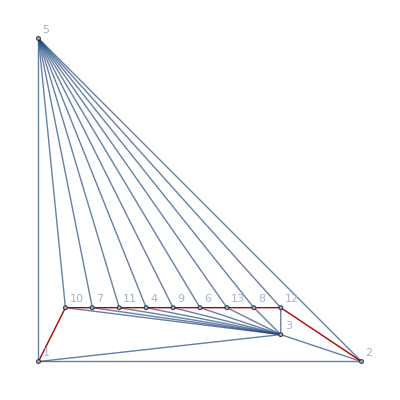

```mathematica
With[
{n=58715},
Graph[ReadGrof[n], VertexLabels->"Name",  GraphLayout->"PlanarEmbedding",GraphHighlight->ReadGraphHighlight[n]]
]
```

```mathematica
Graph[{1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,1<->6,2<->6,1<->7,2<->7,1<->8,2<->8,1<->9,2<->9,1<->10,2<->10,1<->11,2<->11,1<->12,2<->12,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,11<->12},VertexCoordinates->{{10,10},{10,-10},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0}}]
```

Graph[{1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,1<->6,2<->6,1<->7,2<->7,1<->8,2<->8,1<->9,2<->9,1<->10,2<->10,1<->11,2<->11,1<->12,2<->12,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,11<->12},VertexCoordinates→{{10,10},{10,-10},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0}}]

```mathematica
VertexList[Graph[{1,2,3,4,5,6,7,8,9,10,11,12},{1<->3,2<->3,1<->4,2<->4,1<->5,2<->5,1<->6,2<->6,1<->7,2<->7,1<->8,2<->8,1<->9,2<->9,1<->10,2<->10,1<->11,2<->11,1<->12,2<->12,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->11,11<->12}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
Differences[Table[ChromaticPolynomial[DiamondGraph[n],4],{n,1,10}]]
```

{12,24,48,96,192,384,768,1536,3072}

```mathematica
Table[ChromaticPolynomial[DiamondGraph[n],4]/12,{n,1,10}]
```

{3,4,6,10,18,34,66,130,258,514}

```mathematica
Differences[{24,60,120,210,336,504,720,990,1320,1716,2184,2730,3360,4080,4896,5814,6840}]
```

{36,60,90,126,168,216,270,330,396,468,546,630,720,816,918,1026}

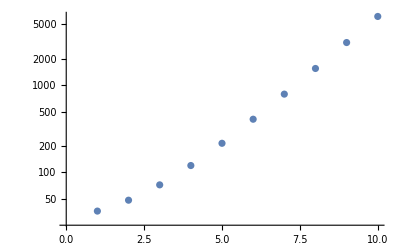

```mathematica
ListLogPlot[Table[{n,ChromaticPolynomial[DiamondGraph[n],4]},{n,1,10}]]
```

```mathematica
TableForm[Table[Factor[FlowPolynomial[EdgeAdd[DiamondGraph[n],1<->2],3]],{n,1,10}]]
```

2
0
4
12
36
108
324
972
2916
8748

```mathematica
TableForm[Table[ChromaticPolynomial[EdgeAdd[DiamondGraph[n],1<->2],5]/60,{n,1,10}]]
```

1
2
4
8
16
32
64
128
256
512

```mathematica
TableForm[Table[FactorInteger[ChromaticPolynomial[DiamondGraph[n],4]/12],{n,1,20}], TableDepth->1]
```

{{3,1}}
{{2,2}}
{{2,1},{3,1}}
{{2,1},{5,1}}
{{2,1},{3,2}}
{{2,1},{17,1}}
{{2,1},{3,1},{11,1}}
{{2,1},{5,1},{13,1}}
{{2,1},{3,1},{43,1}}
{{2,1},{257,1}}
{{2,1},{3,3},{19,1}}
{{2,1},{5,2},{41,1}}
{{2,1},{3,1},{683,1}}
{{2,1},{17,1},{241,1}}
{{2,1},{3,1},{2731,1}}
{{2,1},{5,1},{29,1},{113,1}}
{{2,1},{3,2},{11,1},{331,1}}
{{2,1},{65537,1}}
{{2,1},{3,1},{43691,1}}
{{2,1},{5,1},{13,1},{37,1},{109,1}}

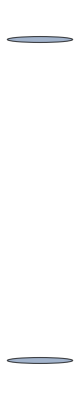

```mathematica
DiamondGraph[0]
```

```mathematica
MaximalPlanarQ[EdgeAdd[DiamondGraph[7],1<->2]]
```

True

```mathematica
Factor[ChromaticPolynomial[ReadGrof[57238],x]/ChromaticPolynomial[EdgeAdd[DiamondGraph[2],1<->2],x]]
```

-42263+109317 x-127092 x^2+87310 x^3-39131 x^4+11890 x^5-2455 x^6+333 x^7-27 x^8+x^9

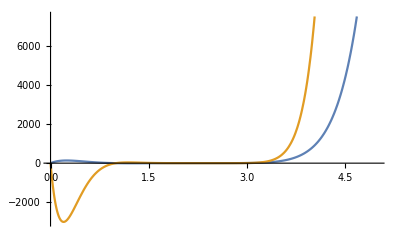

```mathematica
Plot[{(-2+x) (-1+x) x (697-1378 x+1135 x^2-500 x^3+125 x^4-17 x^5+x^6),(-2+x) (-1+x) x (-19427+58025 x-76940 x^2+59444 x^3-29498 x^4+9758 x^5-2156 x^6+308 x^7-26 x^8+x^9)},{x,0,5}]
```

```mathematica
JacobsThalQ[EdgeAdd[DiamondGraph[5],1<->2]]
```

False

```mathematica
Factor[ChromaticPolynomial[ReadGrof[57238],x]/ChromaticPolynomial[EdgeAdd[DiamondGraph[2],1<->2],x]]
```

```mathematica
Dalers = {{7,18,"{2,1<->5,2<->7}"},{18,46,"{2,2<->5,6<->7}"},{21,40,"{2,1<->5,2<->7}"},{40,215,"{2,2<->5,6<->9}"},{40,207,"{2,1<->7,3<->9}"},{41,215,"{2,2<->5,6<->7}"},{62,218,"{2,3<->5,4<->7}"},{72,205,"{2,1<->5,2<->7}"},{111,456,"{2,2<->6,3<->9}"},{111,602,"{2,3<->5,7<->8}"},{111,708,"{2,4<->5,8<->9}"},{120,602,"{2,2<->6,3<->9}"},{120,605,"{2,3<->6,2<->8}"},{120,636,"{2,3<->5,7<->8}"},{161,456,"{2,3<->6,2<->8}"},{161,458,"{2,3<->5,7<->10}"},{171,458,"{2,2<->6,3<->5}"},{171,605,"{2,3<->6,2<->8}"},{171,405,"{2,4<->6,5<->8}"},{202,636,"{2,2<->6,3<->9}"},{205,458,"{2,3<->4,6<->8}"},{205,1302,"{2,3<->7,1<->8}"},{205,1316,"{2,3<->8,4<->7}"},{207,1302,"{2,2<->7,1<->5}"},{207,1318,"{2,3<->8,4<->10}"},{215,1318,"{2,2<->7,1<->5}"},{218,1330,"{2,2<->5,6<->10}"},{218,602,"{2,2<->6,5<->9}"},{218,605,"{2,4<->5,6<->8}"},{218,1316,"{2,4<->8,3<->5}"},{224,1318,"{2,1<->7,3<->10}"},{233,791,"{2,2<->5,6<->9}"},{305,1291,"{2,1<->5,2<->10}"},{383,2489,"{2,3<->5,7<->8}"},{383,3046,"{2,5<->8,3<->4}"},{383,1640,"{2,4<->5,8<->10}"},{383,3047,"{2,3<->6,8<->9}"},{383,3049,"{2,2<->5,9<->11}"},{383,3051,"{2,5<->10,4<->9}"},{402,3069,"{2,3<->7,1<->5}"},{402,2967,"{2,3<->5,7<->8}"},{402,2274,"{2,4<->5,8<->10}"},{402,3090,"{2,3<->6,8<->9}"},{402,3174,"{2,3<->9,2<->6}"},{402,3049,"{2,6<->9,3<->10}"},{405,3091,"{2,2<->5,7<->9}"},{405,3211,"{2,5<->8,4<->11}"},{405,3065,"{2,6<->8,3<->4}"},{405,3363,"{2,3<->11,1<->8}"},{443,3046,"{2,5<->6,4<->9}"},{456,3834,"{2,3<->5,7<->8}"},{456,3853,"{2,3<->6,8<->9}"},{456,3973,"{2,5<->11,2<->4}"},{456,3070,"{2,6<->11,4<->9}"},{458,3065,"{2,5<->6,4<->9}"},{458,3834,"{2,3<->7,1<->11}"},{602,4355,"{2,3<->5,7<->8}"},{602,3363,"{2,3<->6,8<->9}"},{602,3091,"{2,6<->10,4<->9}"},{602,3834,"{2,2<->11,1<->10}"},{605,3363,"{2,2<->7,1<->5}"},{605,3393,"{2,6<->10,4<->9}"},{605,5449,"{2,3<->11,1<->8}"},{605,3834,"{2,8<->11,3<->5}"},{605,4357,"{2,5<->11,7<->8}"},{605,3091,"{2,1<->11,3<->7}"},{636,3377,"{2,5<->6,4<->9}"},{636,4355,"{2,8<->10,3<->11}"},{708,3070,"{2,5<->6,2<->4}"},{708,3853,"{2,6<->9,2<->11}"},{723,3366,"{2,4<->6,5<->10}"},{723,5441,"{2,5<->6,4<->11}"},{723,3091,"{2,5<->8,3<->4}"},{723,3363,"{2,8<->9,3<->10}"},{723,3388,"{2,6<->10,4<->9}"},{791,5442,"{2,3<->8,5<->9}"},{791,5438,"{2,5<->8,3<->4}"},{791,5441,"{2,6<->8,4<->9}"},{791,6264,"{2,2<->9,3<->6}"},{806,3051,"{2,2<->6,3<->9}"},{806,3090,"{2,2<->7,5<->11}"},{806,3047,"{2,5<->8,3<->4}"},{806,3067,"{2,4<->5,8<->9}"},{816,3069,"{2,2<->6,3<->9}"},{816,3982,"{2,3<->5,8<->11}"},{816,3049,"{2,5<->8,3<->4}"},{816,3365,"{2,4<->5,8<->9}"},{817,3048,"{2,2<->6,3<->9}"},{817,2928,"{2,3<->5,7<->11}"},{817,2040,"{2,4<->5,8<->9}"},{817,3971,"{2,5<->9,2<->4}"},{821,3363,"{2,2<->6,3<->9}"},{821,3366,"{2,4<->5,8<->9}"},{821,3091,"{2,6<->8,3<->4}"},{821,3990,"{2,2<->5,9<->10}"},{821,3071,"{2,5<->9,2<->4}"},{822,3176,"{2,2<->6,3<->9}"},{822,3174,"{2,3<->6,2<->11}"},{822,3368,"{2,3<->7,1<->11}"},{822,2328,"{2,4<->5,8<->9}"},{822,2329,"{2,5<->8,4<->11}"},{822,2936,"{2,2<->5,9<->10}"},{822,3980,"{2,5<->9,2<->4}"},{822,6005,"{2,3<->11,6<->7}"},{822,4218,"{2,6<->11,3<->8}"},{822,5442,"{2,5<->11,7<->8}"},{896,5438,"{2,2<->6,3<->9}"},{896,3981,"{2,3<->7,1<->5}"},{896,5442,"{2,3<->8,5<->6}"},{896,5451,"{2,4<->5,8<->11}"},{896,5441,"{2,4<->6,8<->9}"},{896,5361,"{2,2<->10,1<->9}"},{896,5382,"{2,1<->10,2<->7}"},{897,3377,"{2,6<->8,3<->4}"},{897,3990,"{2,9<->10,2<->5}"},{898,3393,"{2,4<->5,8<->9}"},{898,4226,"{2,6<->9,2<->4}"},{899,1830,"{2,2<->6,3<->10}"},{899,5374,"{2,3<->6,2<->8}"},{899,3390,"{2,1<->7,3<->11}"},{899,3368,"{2,3<->7,1<->5}"},{899,3155,"{2,5<->8,3<->4}"},{899,3391,"{2,4<->5,8<->9}"},{928,3051,"{2,2<->5,6<->10}"},{928,3047,"{2,6<->8,3<->4}"},{1291,8522,"{2,1<->7,3<->11}"},{1291,8525,"{2,3<->7,1<->8}"},{1291,3872,"{2,3<->4,8<->10}"},{1291,8526,"{2,3<->8,4<->7}"},{1291,3825,"{2,3<->10,4<->6}"},{1293,8525,"{2,2<->7,1<->5}"},{1293,8531,"{2,2<->5,7<->9}"},{1293,8530,"{2,3<->8,4<->11}"},{1316,3834,"{2,3<->4,6<->11}"},{1316,8542,"{2,3<->7,1<->11}"},{1317,1830,"{2,3<->4,6<->8}"},{1317,6005,"{2,3<->7,1<->8}"},{1317,8629,"{2,3<->8,4<->7}"},{1319,4355,"{2,3<->8,4<->11}"},{1319,8545,"{2,2<->9,3<->10}"},{1329,3155,"{2,3<->4,6<->8}"},{1329,3972,"{2,3<->6,4<->9}"},{1329,5438,"{2,3<->7,1<->8}"},{1329,4615,"{2,5<->7,8<->10}"},{1329,8629,"{2,5<->10,7<->9}"},{1329,3174,"{2,2<->11,1<->9}"},{1329,3368,"{2,9<->11,2<->10}"},{1330,8542,"{2,4<->6,3<->5}"},{1330,4226,"{2,4<->5,6<->8}"},{1330,4355,"{2,2<->9,3<->10}"},{1331,8531,"{2,2<->7,1<->5}"},{1331,8545,"{2,3<->8,4<->10}"},{1349,5448,"{2,2<->5,6<->10}"},{1349,4613,"{2,2<->6,5<->9}"},{1554,8527,"{2,1<->5,2<->10}"},{1609,10533,"{2,3<->8,5<->12}"},{1609,10615,"{2,2<->5,9<->11}"},{1609,10552,"{2,4<->6,10<->12}"},{1609,10617,"{2,6<->10,4<->5}"},{1617,10533,"{2,5<->8,3<->10}"},{1617,10617,"{2,6<->8,3<->4}"},{1617,10767,"{2,2<->5,9<->11}"},{1640,10565,"{2,5<->8,3<->10}"},{1640,10794,"{2,2<->5,9<->11}"},{1640,10826,"{2,5<->6,9<->10}"},{1640,11280,"{2,6<->12,4<->9}"},{1640,10628,"{2,8<->12,3<->4}"},{1827,10615,"{2,3<->7,1<->5}"},{1827,13194,"{2,3<->8,5<->11}"},{1827,13292,"{2,5<->8,3<->10}"},{1827,13516,"{2,4<->6,10<->11}"},{1827,14767,"{2,6<->10,4<->5}"},{1827,14789,"{2,6<->11,3<->4}"},{1827,15052,"{2,2<->12,1<->9}"},{1827,11501,"{2,5<->12,7<->9}"},{1827,10317,"{2,1<->12,2<->7}"},{1830,11502,"{2,2<->5,7<->9}"},{1830,14544,"{2,3<->6,9<->11}"},{1830,15098,"{2,5<->8,10<->12}"},{1830,12363,"{2,3<->12,1<->8}"},{2037,10874,"{2,3<->7,1<->5}"},{2037,13194,"{2,5<->8,3<->10}"},{2037,14767,"{2,6<->8,3<->4}"},{2037,18339,"{2,2<->12,1<->9}"},{2037,10767,"{2,9<->12,2<->5}"},{2037,11772,"{2,5<->12,7<->9}"},{2037,9813,"{2,1<->12,2<->7}"},{2040,10868,"{2,2<->7,1<->5}"},{2040,11773,"{2,2<->5,7<->9}"},{2040,14770,"{2,6<->8,3<->4}"},{2040,18375,"{2,3<->12,1<->8}"},{2040,12542,"{2,5<->12,7<->8}"},{2040,10869,"{2,1<->12,3<->7}"},{2274,11283,"{2,3<->7,1<->5}"},{2274,13783,"{2,5<->8,3<->10}"},{2274,17744,"{2,5<->6,9<->10}"},{2274,12143,"{2,2<->11,1<->9}"},{2274,10794,"{2,9<->11,2<->5}"},{2274,11284,"{2,1<->11,2<->7}"},{2274,21391,"{2,6<->12,4<->9}"},{2274,15059,"{2,8<->12,3<->4}"},{2328,12158,"{2,2<->5,7<->9}"},{2328,17771,"{2,5<->6,9<->10}"},{2328,21763,"{2,3<->11,1<->8}"},{2328,12775,"{2,5<->11,7<->8}"},{2328,15103,"{2,8<->12,3<->4}"},{2329,12159,"{2,2<->5,7<->9}"},{2329,21750,"{2,5<->8,10<->11}"},{2329,12776,"{2,5<->11,7<->8}"},{2329,21832,"{2,8<->12,4<->11}"},{2329,15107,"{2,6<->12,3<->4}"},{2467,23098,"{2,3<->5,7<->12}"},{2467,10617,"{2,3<->8,6<->12}"},{2467,23131,"{2,6<->8,3<->10}"},{2467,23134,"{2,2<->5,9<->11}"},{2467,10629,"{2,4<->5,10<->12}"},{2467,10533,"{2,5<->10,4<->6}"},{2489,23518,"{2,3<->7,1<->12}"},{2489,23148,"{2,6<->8,3<->10}"},{2489,23298,"{2,2<->5,9<->11}"},{2489,23519,"{2,5<->7,11<->12}"},{2601,23150,"{2,3<->7,1<->5}"},{2601,22945,"{2,3<->5,7<->11}"},{2601,14767,"{2,3<->8,6<->11}"},{2601,23134,"{2,6<->8,3<->10}"},{2601,10211,"{2,4<->5,10<->11}"},{2601,13194,"{2,5<->10,4<->6}"},{2894,23298,"{2,6<->8,3<->10}"},{2928,23954,"{2,2<->5,7<->9}"},{2928,25878,"{2,3<->6,8<->9}"},{2928,26117,"{2,6<->8,3<->10}"},{2928,26380,"{2,2<->9,3<->5}"},{2928,26857,"{2,5<->6,9<->10}"},{2928,23099,"{2,8<->11,3<->12}"},{2928,24524,"{2,5<->11,7<->12}"},{2936,23961,"{2,2<->5,7<->9}"},{2936,25197,"{2,6<->8,3<->10}"},{2936,26388,"{2,2<->9,3<->5}"},{2936,26863,"{2,5<->6,9<->10}"},{2936,24538,"{2,8<->11,3<->12}"},{2936,28820,"{2,7<->11,1<->12}"},{2967,23518,"{2,2<->7,1<->5}"},{2967,24538,"{2,5<->11,4<->7}"},{2967,23519,"{2,8<->11,3<->4}"},{3044,23067,"{2,3<->5,8<->12}"},{3044,23134,"{2,5<->8,3<->4}"},{3044,10475,"{2,4<->5,8<->10}"},{3044,14789,"{2,3<->6,8<->9}"},{3044,23150,"{2,6<->9,3<->10}"},{3044,13292,"{2,5<->10,4<->9}"},{3045,23074,"{2,3<->5,7<->12}"},{3045,10542,"{2,4<->5,8<->10}"},{3045,10801,"{2,5<->8,4<->12}"},{3045,29640,"{2,3<->9,2<->6}"},{3045,29641,"{2,3<->6,9<->12}"},{3045,23130,"{2,6<->9,3<->10}"},{3045,29642,"{2,2<->5,9<->11}"},{3045,23149,"{2,5<->9,2<->10}"},{3045,29643,"{2,5<->10,4<->9}"},{3045,29644,"{2,5<->12,3<->8}"},{3046,29662,"{2,3<->6,8<->9}"},{3046,10565,"{2,4<->6,8<->10}"},{3046,29664,"{2,2<->5,9<->11}"},{3046,10628,"{2,4<->5,10<->12}"},{3047,29662,"{2,5<->8,3<->4}"},{3047,10826,"{2,6<->8,4<->12}"},{3047,29676,"{2,2<->5,9<->11}"},{3047,11280,"{2,6<->9,10<->12}"},{3048,23099,"{2,3<->5,7<->8}"},{3048,29691,"{2,3<->6,8<->12}"},{3048,23149,"{2,2<->9,5<->12}"},{3048,29693,"{2,5<->9,2<->10}"},{3048,29661,"{2,6<->9,10<->12}"},{3048,29695,"{2,3<->12,2<->6}"},{3049,23519,"{2,3<->5,7<->8}"},{3049,29664,"{2,5<->8,3<->4}"},{3049,10794,"{2,4<->5,8<->10}"},{3049,29676,"{2,3<->6,8<->9}"},{3049,29675,"{2,6<->9,3<->10}"},{3049,29714,"{2,5<->10,4<->9}"},{3049,13783,"{2,2<->11,1<->12}"},{3049,15059,"{2,5<->11,7<->12}"},{3050,23520,"{2,3<->5,7<->8}"},{3050,18375,"{2,3<->6,8<->9}"},{3050,29693,"{2,3<->9,2<->6}"},{3050,12542,"{2,6<->10,4<->9}"},{3050,29661,"{2,9<->10,6<->12}"},{3051,11280,"{2,4<->5,8<->12}"},{3051,10826,"{2,4<->6,8<->10}"},{3051,29662,"{2,6<->9,3<->10}"},{3051,29714,"{2,2<->5,9<->11}"},{3063,23298,"{2,6<->8,3<->4}"},{3064,23954,"{2,3<->7,1<->12}"},{3064,23074,"{2,2<->9,3<->5}"},{3064,29709,"{2,3<->9,2<->6}"},{3064,23202,"{2,6<->9,3<->10}"},{3064,23964,"{2,2<->5,9<->11}"},{3064,23525,"{2,5<->9,2<->10}"},{3065,29728,"{2,3<->7,1<->12}"},{3065,29875,"{2,5<->7,11<->12}"},{3066,11251,"{2,4<->5,8<->10}"},{3066,29876,"{2,5<->8,4<->12}"},{3066,13292,"{2,2<->5,9<->11}"},{3066,10767,"{2,5<->10,4<->9}"},{3066,29878,"{2,6<->9,10<->12}"},{3066,10874,"{2,6<->12,8<->9}"},{3067,11280,"{2,6<->8,3<->4}"},{3067,10826,"{2,6<->9,3<->10}"},{3067,12143,"{2,2<->5,9<->11}"},{3068,11773,"{2,6<->8,4<->12}"},{3068,29691,"{2,9<->12,2<->6}"},{3069,23518,"{2,3<->5,7<->8}"},{3069,29675,"{2,5<->8,3<->4}"},{3069,11283,"{2,4<->5,8<->10}"},{3069,29692,"{2,3<->6,8<->9}"},{3069,29664,"{2,6<->9,3<->10}"},{3069,29676,"{2,5<->10,4<->9}"},{3069,13783,"{2,1<->12,2<->11}"},{3069,29730,"{2,5<->12,9<->11}"},{3071,23528,"{2,3<->5,7<->8}"},{3071,21763,"{2,3<->6,8<->9}"},{3071,21822,"{2,5<->10,4<->12}"},{3071,12775,"{2,6<->10,4<->9}"},{3090,29730,"{2,3<->7,1<->5}"},{3090,29692,"{2,5<->8,3<->4}"},{3090,12143,"{2,4<->5,8<->10}"},{3090,29714,"{2,3<->6,8<->9}"},{3090,12363,"{2,3<->9,2<->6}"},{3090,29676,"{2,6<->9,3<->10}"},{3090,21391,"{2,9<->12,2<->11}"},{3090,17744,"{2,7<->12,1<->11}"},{3091,29728,"{2,6<->8,3<->4}"},{3091,29875,"{2,6<->9,3<->10}"},{3113,29660,"{2,3<->7,1<->5}"},{3113,23530,"{2,3<->5,7<->11}"},{3113,11180,"{2,4<->5,8<->10}"},{3113,15405,"{2,5<->8,4<->11}"},{3113,30211,"{2,3<->9,2<->6}"},{3113,15051,"{2,3<->6,9<->11}"},{3113,24916,"{2,6<->9,3<->10}"},{3113,29990,"{2,5<->10,4<->9}"},{3113,28741,"{2,5<->9,10<->12}"},{3113,29890,"{2,5<->11,3<->8}"},{3113,29916,"{2,2<->12,1<->9}"},{3113,29642,"{2,9<->12,2<->5}"},{3113,21291,"{2,1<->12,2<->7}"},{3155,29689,"{2,2<->7,1<->5}"},{3155,21750,"{2,2<->5,7<->9}"},{3155,11341,"{2,4<->5,8<->10}"},{3155,21767,"{2,5<->8,4<->12}"},{3155,17771,"{2,6<->8,4<->11}"},{3155,21832,"{2,3<->12,1<->8}"},{3155,21836,"{2,1<->12,3<->7}"},{3174,24538,"{2,3<->5,7<->8}"},{3174,30138,"{2,3<->6,8<->11}"},{3174,31012,"{2,5<->9,10<->12}"},{3174,29729,"{2,6<->9,10<->11}"},{3174,12363,"{2,2<->12,1<->9}"},{3176,23525,"{2,2<->9,5<->11}"},{3176,30841,"{2,5<->9,2<->10}"},{3176,17772,"{2,6<->9,10<->11}"},{3176,31030,"{2,3<->12,1<->8}"},{3176,23099,"{2,8<->12,3<->5}"},{3176,30140,"{2,5<->12,7<->8}"},{3211,30139,"{2,3<->12,1<->8}"},{3363,29875,"{2,6<->8,3<->4}"},{3363,29728,"{2,6<->9,3<->10}"},{3364,16287,"{2,4<->5,8<->10}"},{3364,15801,"{2,5<->8,4<->12}"},{3364,30152,"{2,3<->9,2<->6}"},{3364,24537,"{2,6<->9,3<->10}"},{3364,28759,"{2,5<->10,4<->9}"},{3364,28723,"{2,5<->9,10<->11}"},{3364,28564,"{2,2<->11,1<->9}"},{3364,23964,"{2,9<->11,2<->5}"},{3364,15106,"{2,5<->11,7<->9}"},{3364,23954,"{2,7<->11,1<->5}"},{3364,21361,"{2,1<->11,2<->7}"},{3364,28669,"{2,3<->12,6<->7}"},{3364,23986,"{2,6<->12,3<->8}"},{3364,28627,"{2,5<->12,7<->8}"},{3364,23530,"{2,7<->12,3<->5}"},{3365,10794,"{2,3<->7,1<->5}"},{3365,13783,"{2,3<->6,8<->9}"},{3365,15059,"{2,6<->10,4<->9}"},{3365,11283,"{2,9<->11,2<->5}"},{3365,22255,"{2,1<->11,2<->7}"},{3366,21822,"{2,5<->8,3<->4}"},{3366,12158,"{2,6<->8,4<->12}"},{3366,15108,"{2,5<->9,10<->11}"},{3366,12159,"{2,6<->9,10<->12}"},{3366,21763,"{2,2<->11,1<->9}"},{3366,12775,"{2,5<->11,7<->9}"},{3367,29896,"{2,3<->7,1<->5}"},{3367,23537,"{2,3<->5,7<->8}"},{3367,13975,"{2,4<->5,8<->10}"},{3367,15106,"{2,5<->10,4<->9}"},{3367,31017,"{2,5<->9,10<->11}"},{3367,32593,"{2,9<->12,6<->11}"},{3368,21750,"{2,3<->7,1<->5}"},{3368,28820,"{2,3<->5,7<->8}"},{3368,15072,"{2,3<->6,8<->9}"},{3368,28819,"{2,3<->9,2<->6}"},{3368,21832,"{2,2<->11,1<->9}"},{3368,30140,"{2,9<->11,2<->12}"},{3368,31030,"{2,5<->11,7<->12}"},{3368,17771,"{2,1<->11,2<->7}"},{3368,12363,"{2,11<->12,5<->9}"},{3381,28659,"{2,3<->8,6<->11}"},{3381,11773,"{2,6<->8,3<->4}"},{3381,21836,"{2,2<->11,5<->12}"},{3388,12158,"{2,6<->8,3<->4}"},{3388,12159,"{2,6<->9,3<->10}"},{3388,21537,"{2,5<->9,2<->10}"},{3390,28727,"{2,2<->5,7<->9}"},{3390,15072,"{2,5<->8,4<->11}"},{3390,11502,"{2,6<->8,3<->4}"},{3390,32583,"{2,3<->11,1<->8}"},{3391,21340,"{2,2<->7,1<->5}"},{3391,17771,"{2,2<->5,7<->9}"},{3392,31033,"{2,1<->7,2<->11}"},{3392,31318,"{2,5<->8,4<->11}"},{3392,28830,"{2,6<->8,4<->12}"},{3392,23500,"{2,2<->9,3<->5}"},{3392,23982,"{2,1<->11,7<->12}"},{3392,23961,"{2,1<->12,3<->11}"},{3393,30145,"{2,3<->11,1<->8}"},{3394,29878,"{2,5<->8,3<->4}"},{3394,21882,"{2,4<->5,8<->10}"},{3394,18339,"{2,3<->6,8<->9}"},{3394,29876,"{2,6<->9,3<->10}"},{3394,11772,"{2,5<->10,4<->9}"},{3394,11501,"{2,2<->11,9<->12}"},{3404,30152,"{2,2<->5,7<->9}"},{3404,11212,"{2,4<->5,8<->10}"},{3404,21827,"{2,5<->8,4<->11}"},{3404,24061,"{2,2<->9,3<->5}"},{3404,25886,"{2,6<->9,3<->10}"},{3404,28573,"{2,7<->12,1<->11}"},{3825,23098,"{2,4<->6,5<->12}"},{3825,23148,"{2,5<->6,4<->9}"},{3834,29875,"{2,3<->7,1<->11}"},{3834,29728,"{2,5<->7,10<->11}"},{3836,23131,"{2,5<->6,4<->9}"},{3837,29663,"{2,5<->6,4<->9}"},{3837,36371,"{2,3<->5,7<->11}"},{3872,23251,"{2,4<->6,5<->8}"},{3872,23148,"{2,5<->6,4<->9}"},{3872,36392,"{2,3<->7,1<->12}"},{3887,36410,"{2,3<->5,7<->8}"},{3887,29693,"{2,2<->12,5<->9}"},{3889,29710,"{2,5<->6,4<->9}"},{3889,36411,"{2,3<->7,1<->12}"},{3970,15098,"{2,3<->5,7<->8}"},{3970,12542,"{2,5<->8,3<->12}"},{3970,36511,"{2,3<->6,8<->9}"},{3970,18375,"{2,6<->8,3<->4}"},{3970,21736,"{2,2<->5,10<->11}"},{3971,26117,"{2,3<->5,7<->8}"},{3971,29731,"{2,5<->8,3<->4}"},{3971,37461,"{2,4<->5,8<->11}"},{3971,18375,"{2,3<->6,8<->9}"},{3971,37411,"{2,2<->5,10<->11}"},{3971,29693,"{2,5<->11,2<->4}"},{3971,12542,"{2,6<->11,4<->9}"},{3972,29891,"{2,3<->7,1<->5}"},{3972,36450,"{2,3<->5,7<->8}"},{3972,21736,"{2,4<->5,8<->11}"},{3972,21832,"{2,3<->6,8<->9}"},{3972,21750,"{2,2<->10,1<->12}"},{3972,30841,"{2,5<->11,4<->12}"},{3980,25197,"{2,3<->5,7<->8}"},{3980,21763,"{2,3<->6,8<->9}"},{3980,12775,"{2,6<->11,4<->9}"},{3980,36451,"{2,5<->12,10<->11}"},{3980,21750,"{2,1<->12,2<->10}"},{3981,21822,"{2,3<->7,1<->5}"},{3981,31318,"{2,3<->5,7<->8}"},{3981,30139,"{2,2<->10,1<->12}"},{3982,23519,"{2,6<->8,3<->4}"},{3982,23518,"{2,8<->11,3<->12}"},{3982,36464,"{2,5<->11,7<->12}"},{3995,29876,"{2,5<->6,4<->9}"},{3995,29878,"{2,6<->11,8<->9}"},{4218,30140,"{2,5<->6,4<->9}"},{4218,12780,"{2,2<->7,1<->10}"},{4218,31030,"{2,3<->6,8<->9}"},{4218,26857,"{2,2<->9,3<->10}"},{4218,26117,"{2,6<->9,3<->5}"},{4218,39218,"{2,5<->11,4<->7}"},{4218,28761,"{2,3<->11,8<->12}"},{4226,21831,"{2,2<->7,1<->10}"},{4226,25197,"{2,6<->9,3<->5}"},{4226,21837,"{2,8<->11,4<->12}"},{4357,30145,"{2,6<->11,4<->9}"},{5449,30145,"{2,6<->10,4<->9}"},{4483,23518,"{2,2<->5,7<->10}"},{4483,36392,"{2,6<->8,3<->4}"},{4483,39524,"{2,5<->11,7<->12}"},{4492,23528,"{2,5<->6,4<->9}"},{4492,25197,"{2,2<->5,7<->10}"},{4492,39524,"{2,8<->11,3<->12}"},{4613,17295,"{2,3<->7,1<->5}"},{4613,31028,"{2,3<->5,7<->8}"},{4613,32584,"{2,3<->6,8<->10}"},{4613,30141,"{2,6<->11,4<->9}"},{4613,36411,"{2,2<->12,1<->11}"},{4613,36887,"{2,11<->12,2<->5}"},{4615,30138,"{2,2<->7,1<->5}"},{4615,37475,"{2,2<->5,7<->11}"},{4615,30882,"{2,4<->8,5<->6}"},{4615,31175,"{2,6<->8,3<->4}"},{4615,30841,"{2,2<->11,5<->9}"},{4615,37473,"{2,5<->11,2<->4}"},{4615,28827,"{2,6<->11,4<->9}"},{4615,31030,"{2,3<->12,1<->8}"},{4615,36410,"{2,8<->12,3<->5}"},{4615,30140,"{2,5<->12,7<->8}"},{4615,29729,"{2,1<->12,3<->7}"},{4645,28825,"{2,5<->6,4<->9}"},{4645,37475,"{2,5<->7,2<->12}"},{4645,31028,"{2,8<->11,3<->12}"},{4645,21835,"{2,7<->11,1<->12}"},{5361,21837,"{2,2<->7,1<->11}"},{5361,39252,"{2,3<->6,8<->9}"},{5361,31016,"{2,6<->8,3<->4}"},{5361,36450,"{2,8<->12,3<->5}"},{5374,32583,"{2,2<->7,1<->5}"},{5374,28819,"{2,2<->5,7<->10}"},{5374,28627,"{2,3<->6,8<->9}"},{5374,21767,"{2,6<->8,3<->4}"},{5374,38021,"{2,2<->9,3<->10}"},{5374,15102,"{2,2<->10,5<->9}"},{5374,21538,"{2,6<->10,4<->9}"},{5374,31030,"{2,3<->12,1<->8}"},{5374,15098,"{2,8<->12,3<->5}"},{5374,30140,"{2,5<->12,7<->8}"},{5374,28727,"{2,1<->12,3<->7}"},{5382,21537,"{2,2<->7,1<->5}"},{5382,39252,"{2,2<->5,7<->10}"},{5382,30139,"{2,3<->12,1<->8}"},{5438,31012,"{2,3<->8,5<->6}"},{5438,28820,"{2,4<->5,8<->12}"},{5438,24538,"{2,4<->6,8<->10}"},{5438,36450,"{2,2<->11,1<->10}"},{5438,28821,"{2,5<->11,7<->12}"},{5438,46276,"{2,4<->12,5<->10}"},{5441,15108,"{2,2<->11,1<->10}"},{5441,31016,"{2,6<->12,3<->8}"},{5441,24538,"{2,7<->12,3<->5}"},{5442,12776,"{2,2<->11,1<->12}"},{5442,46276,"{2,10<->12,6<->11}"},{5446,32586,"{2,6<->10,4<->9}"},{5448,31029,"{2,4<->8,5<->6}"},{5448,37475,"{2,5<->8,4<->11}"},{5448,21835,"{2,6<->8,4<->12}"},{5448,31028,"{2,2<->10,5<->9}"},{5448,39251,"{2,3<->11,1<->12}"},{5450,31318,"{2,2<->10,5<->9}"},{5450,32586,"{2,6<->10,4<->9}"},{5450,28821,"{2,8<->11,5<->12}"},{5450,28829,"{2,1<->11,7<->12}"},{5451,21536,"{2,6<->8,4<->12}"},{5451,15108,"{2,2<->10,5<->9}"},{5451,21837,"{2,3<->11,1<->12}"},{5593,24523,"{2,4<->6,5<->8}"},{5593,28829,"{2,5<->6,4<->9}"},{5593,28821,"{2,2<->7,1<->5}"},{5782,15106,"{2,2<->5,6<->11}"},{5782,28659,"{2,5<->6,2<->10}"},{5782,28653,"{2,2<->9,3<->6}"},{5782,36511,"{2,6<->9,2<->12}"},{5784,18373,"{2,2<->5,6<->11}"},{5784,29690,"{2,6<->8,4<->9}"},{6005,46276,"{2,5<->6,2<->10}"},{6005,31017,"{2,3<->8,9<->11}"},{6005,39223,"{2,6<->8,9<->10}"},{6005,14544,"{2,4<->5,10<->12}"},{6005,15098,"{2,5<->10,4<->6}"},{6005,24523,"{2,5<->11,7<->12}"},{6005,36410,"{2,5<->12,4<->11}"},{6168,23961,"{2,5<->6,4<->11}"},{6168,23537,"{2,2<->9,3<->6}"},{6264,46276,"{2,3<->8,5<->9}"},{6264,24538,"{2,6<->8,4<->9}"},{6273,37868,"{2,2<->5,6<->7}"},{6273,39646,"{2,6<->8,4<->9}"},{6590,18338,"{2,2<->6,3<->9}"},{6590,28653,"{2,2<->5,7<->9}"},{6590,29916,"{2,2<->7,5<->12}"},{6590,15454,"{2,4<->5,8<->9}"},{6590,29677,"{2,5<->9,2<->4}"},{6612,15052,"{2,2<->6,3<->9}"},{6612,11501,"{2,5<->8,3<->4}"},{6612,29614,"{2,4<->5,8<->9}"},{6672,29628,"{2,2<->6,3<->9}"},{6672,18168,"{2,4<->5,8<->9}"},{6672,23491,"{2,2<->5,9<->10}"},{6672,29716,"{2,5<->9,2<->4}"},{6672,29642,"{2,1<->10,2<->7}"},{6672,30390,"{2,1<->7,10<->11}"},{6674,23954,"{2,2<->6,3<->9}"},{6674,29896,"{2,3<->6,2<->8}"},{6674,15062,"{2,4<->5,8<->9}"},{6674,23964,"{2,6<->8,3<->4}"},{6674,23500,"{2,2<->5,9<->10}"},{6674,25155,"{2,5<->9,2<->4}"},{6674,28760,"{2,1<->10,2<->7}"},{6674,18381,"{2,1<->7,10<->11}"},{6674,18382,"{2,1<->11,7<->12}"},{6674,30008,"{2,1<->12,3<->11}"},{6674,41202,"{2,3<->12,1<->8}"},{6674,37473,"{2,5<->12,8<->11}"},{6674,23491,"{2,8<->12,3<->5}"},{6675,29640,"{2,2<->6,3<->9}"},{6675,27069,"{2,3<->5,7<->11}"},{6675,37465,"{2,5<->9,2<->4}"},{6675,16513,"{2,4<->5,9<->12}"},{6675,10488,"{2,5<->12,4<->8}"},{6679,29709,"{2,2<->6,3<->9}"},{6679,30211,"{2,3<->6,2<->12}"},{6679,32595,"{2,3<->7,1<->12}"},{6679,15104,"{2,4<->5,8<->9}"},{6679,10501,"{2,5<->8,4<->11}"},{6679,24061,"{2,2<->5,9<->10}"},{6679,37472,"{2,5<->9,2<->4}"},{6679,16806,"{2,5<->11,8<->12}"},{6679,25878,"{2,6<->12,3<->11}"},{6679,28757,"{2,5<->12,7<->11}"},{6679,27069,"{2,7<->12,3<->5}"},{6694,32585,"{2,2<->6,3<->9}"},{6694,30807,"{2,4<->5,8<->9}"},{6694,37475,"{2,5<->8,4<->11}"},{6694,28767,"{2,6<->8,4<->12}"},{6694,37514,"{2,2<->5,9<->10}"},{6694,29713,"{2,5<->9,2<->4}"},{6694,41893,"{2,1<->12,3<->11}"},{6694,41897,"{2,11<->12,1<->8}"},{6696,28777,"{2,2<->6,3<->9}"},{6696,31017,"{2,3<->6,2<->12}"},{6696,15103,"{2,4<->5,8<->9}"},{6696,15107,"{2,5<->8,4<->11}"},{6696,36451,"{2,5<->9,2<->4}"},{6696,30152,"{2,1<->7,10<->12}"},{6696,39218,"{2,6<->11,8<->12}"},{6752,14746,"{2,2<->6,3<->11}"},{6752,28669,"{2,3<->6,2<->10}"},{6752,32666,"{2,1<->7,3<->12}"},{6752,32595,"{2,3<->7,1<->5}"},{6752,11207,"{2,4<->5,8<->9}"},{6752,30691,"{2,5<->9,4<->11}"},{6984,37514,"{2,2<->6,3<->9}"},{6984,31026,"{2,3<->6,2<->8}"},{6986,30146,"{2,3<->6,2<->8}"},{6986,30806,"{2,1<->7,3<->12}"},{6986,32667,"{2,4<->5,8<->9}"},{7064,11772,"{2,2<->7,5<->12}"},{7064,18339,"{2,3<->7,5<->10}"},{7235,21861,"{2,3<->5,7<->8}"},{8522,23251,"{2,3<->4,8<->10}"},{8522,40362,"{2,3<->8,4<->7}"},{8522,57167,"{2,3<->7,8<->11}"},{8522,57229,"{2,5<->7,8<->12}"},{8522,23098,"{2,3<->10,4<->6}"},{8522,57136,"{2,2<->12,1<->5}"},{8525,40371,"{2,3<->8,4<->12}"},{8525,57167,"{2,7<->8,5<->12}"},{8526,40362,"{2,1<->7,3<->11}"},{8526,57237,"{2,3<->7,1<->12}"},{8526,36392,"{2,4<->5,8<->10}"},{8527,57136,"{2,3<->7,1<->8}"},{8527,57239,"{2,3<->8,7<->12}"},{8527,36650,"{2,3<->6,9<->10}"},{8527,36370,"{2,3<->4,10<->12}"},{8528,48401,"{2,3<->7,1<->8}"},{8528,14654,"{2,3<->4,8<->10}"},{8528,57238,"{2,3<->8,4<->7}"},{8528,10482,"{2,3<->10,4<->6}"},{8530,57231,"{2,4<->8,5<->12}"},{8530,39524,"{2,3<->4,10<->12}"},{8531,57247,"{2,5<->8,4<->7}"},{8531,57231,"{2,2<->9,3<->11}"},{8541,28750,"{2,3<->7,1<->8}"},{8541,14770,"{2,3<->4,8<->10}"},{8541,37411,"{2,3<->8,4<->7}"},{8541,41202,"{2,5<->7,8<->11}"},{8541,57262,"{2,5<->11,7<->9}"},{8541,30211,"{2,2<->12,1<->9}"},{8541,32595,"{2,9<->12,2<->11}"},{8542,57247,"{2,1<->12,3<->7}"},{8543,57248,"{2,2<->5,7<->9}"},{8543,57231,"{2,3<->8,4<->11}"},{8629,36410,"{2,3<->4,6<->11}"},{8629,46276,"{2,3<->7,1<->11}"},{8629,12363,"{2,2<->5,9<->10}"},{8630,14746,"{2,3<->4,6<->8}"},{8630,57262,"{2,1<->7,3<->11}"},{8630,32593,"{2,3<->7,1<->8}"},{8645,29873,"{2,3<->4,6<->8}"},{8645,28749,"{2,3<->6,4<->9}"},{8645,37498,"{2,3<->7,8<->12}"},{8645,32596,"{2,5<->7,8<->10}"},{8646,30707,"{2,3<->4,6<->8}"},{8646,36887,"{2,3<->6,4<->9}"},{8646,41897,"{2,3<->7,1<->8}"},{8646,30880,"{2,5<->10,9<->12}"},{8646,32597,"{2,9<->11,2<->10}"},{9149,57240,"{2,1<->5,2<->10}"},{9498,60736,"{2,2<->7,5<->13}"},{9498,60735,"{2,3<->7,5<->11}"},{9498,61032,"{2,3<->8,5<->12}"},{9498,65737,"{2,5<->8,3<->10}"},{9498,66029,"{2,4<->6,10<->12}"},{9498,61033,"{2,6<->10,4<->5}"},{9498,61053,"{2,6<->12,3<->4}"},{9518,60772,"{2,3<->7,5<->11}"},{9518,65392,"{2,3<->8,5<->12}"},{9518,65762,"{2,5<->8,3<->10}"},{9518,66049,"{2,4<->6,10<->12}"},{9518,68061,"{2,6<->10,4<->5}"},{9518,68088,"{2,3<->11,1<->7}"},{9518,68118,"{2,6<->12,3<->4}"},{9518,60735,"{2,1<->13,2<->11}"},{9518,60736,"{2,5<->13,2<->7}"},{9522,60736,"{2,2<->7,5<->11}"},{9522,60735,"{2,3<->8,5<->12}"},{9522,66052,"{2,4<->6,10<->12}"},{9757,61033,"{2,2<->7,5<->13}"},{9757,61032,"{2,3<->7,5<->11}"},{9774,61064,"{2,3<->7,5<->11}"},{9774,65392,"{2,5<->8,3<->10}"},{9774,68061,"{2,6<->8,3<->4}"},{9774,68097,"{2,3<->11,1<->7}"},{9774,61032,"{2,1<->13,2<->11}"},{9774,73839,"{2,2<->13,1<->5}"},{9774,61033,"{2,5<->13,2<->7}"},{9813,61165,"{2,2<->7,5<->12}"},{9813,61131,"{2,3<->7,5<->11}"},{9813,66089,"{2,5<->8,3<->10}"},{9813,72292,"{2,5<->6,9<->10}"},{9813,74560,"{2,6<->13,4<->9}"},{9813,68094,"{2,8<->13,3<->4}"},{10211,61842,"{2,3<->7,5<->11}"},{10211,66545,"{2,5<->8,3<->10}"},{10211,72805,"{2,5<->6,9<->10}"},{10211,74406,"{2,3<->11,1<->7}"},{10211,61131,"{2,1<->12,2<->11}"},{10211,80871,"{2,2<->12,1<->5}"},{10211,61165,"{2,5<->12,2<->7}"},{10211,81185,"{2,6<->13,4<->9}"},{10211,68542,"{2,8<->13,3<->4}"},{10317,61671,"{2,2<->7,5<->11}"},{10317,66596,"{2,5<->8,3<->10}"},{10317,72902,"{2,5<->6,9<->10}"},{10317,74504,"{2,2<->11,1<->7}"},{10317,61165,"{2,1<->12,3<->11}"},{10317,82414,"{2,3<->12,1<->5}"},{10317,61131,"{2,5<->12,3<->7}"},{10317,82563,"{2,6<->13,4<->9}"},{10317,68603,"{2,8<->13,3<->4}"},{10451,65762,"{2,5<->8,3<->10}"},{10451,68118,"{2,6<->8,3<->4}"},{10451,65737,"{2,1<->11,2<->7}"},{10451,68095,"{2,1<->7,11<->12}"},{10451,73839,"{2,1<->12,3<->7}"},{10475,66545,"{2,5<->8,3<->10}"},{10475,84264,"{2,5<->6,9<->10}"},{10475,82414,"{2,1<->11,2<->7}"},{10475,81018,"{2,1<->7,11<->12}"},{10475,80871,"{2,1<->12,3<->7}"},{10475,84713,"{2,6<->13,4<->9}"},{10475,68542,"{2,8<->13,3<->4}"},{10482,63307,"{2,1<->7,3<->11}"},{10482,68538,"{2,3<->7,1<->12}"},{10482,84824,"{2,3<->6,9<->13}"},{10488,81054,"{2,3<->7,1<->12}"},{10488,84799,"{2,3<->6,8<->9}"},{10488,84933,"{2,3<->9,2<->6}"},{10488,73843,"{2,2<->5,9<->11}"},{10488,84970,"{2,5<->6,9<->13}"},{10501,64181,"{2,1<->7,3<->11}"},{10501,81081,"{2,3<->7,1<->12}"},{10501,81038,"{2,2<->5,9<->11}"},{10501,84994,"{2,5<->6,9<->10}"},{10501,84995,"{2,5<->8,10<->12}"},{10501,68537,"{2,2<->11,1<->5}"},{10501,81037,"{2,5<->7,11<->12}"},{10501,85254,"{2,6<->13,4<->9}"},{10501,84825,"{2,3<->13,8<->9}"},{10507,85351,"{2,2<->5,9<->11}"},{10507,62498,"{2,4<->6,10<->13}"},{10507,85354,"{2,6<->10,4<->5}"},{10507,85355,"{2,5<->8,10<->12}"},{10507,85357,"{2,8<->12,5<->13}"},{10507,85359,"{2,6<->13,4<->12}"},{10513,85354,"{2,6<->8,4<->12}"},{10513,85357,"{2,2<->5,9<->11}"},{10533,85529,"{2,2<->5,9<->11}"},{10533,85603,"{2,5<->8,10<->12}"},{10533,86001,"{2,6<->13,3<->4}"},{10533,85387,"{2,8<->13,4<->12}"},{10542,85247,"{2,3<->5,7<->12}"},{10542,73842,"{2,4<->8,6<->10}"},{10542,85381,"{2,6<->8,4<->12}"},{10542,85533,"{2,2<->5,9<->11}"},{10542,84309,"{2,8<->10,4<->5}"},{10542,85610,"{2,5<->8,10<->12}"},{10542,86122,"{2,6<->13,4<->9}"},{10542,85570,"{2,5<->13,9<->10}"},{10552,85387,"{2,6<->8,3<->4}"},{10552,86271,"{2,2<->5,9<->11}"},{10552,85603,"{2,8<->12,3<->13}"},{10565,86293,"{2,2<->5,9<->11}"},{10571,86012,"{2,5<->8,3<->10}"},{10571,86604,"{2,2<->5,9<->11}"},{10571,86606,"{2,5<->6,9<->10}"},{10571,86610,"{2,3<->12,8<->9}"},{10571,86611,"{2,8<->12,3<->13}"},{10571,86612,"{2,9<->12,3<->6}"},{10571,86613,"{2,6<->12,9<->13}"},{10579,84799,"{2,3<->5,7<->8}"},{10579,85998,"{2,5<->8,3<->10}"},{10579,86609,"{2,6<->8,4<->12}"},{10579,86683,"{2,3<->9,2<->12}"},{10579,86722,"{2,2<->5,9<->11}"},{10579,86759,"{2,5<->9,2<->6}"},{10579,86798,"{2,5<->6,9<->13}"},{10602,86748,"{2,2<->5,9<->11}"},{10602,86611,"{2,3<->8,12<->13}"},{10602,87413,"{2,8<->13,3<->4}"},{10602,85563,"{2,5<->13,3<->10}"},{10605,86751,"{2,2<->5,9<->11}"},{10605,86826,"{2,5<->6,9<->10}"},{10605,87443,"{2,6<->13,4<->9}"},{10605,86613,"{2,9<->13,6<->12}"},{10613,85415,"{2,3<->8,5<->12}"},{10613,86238,"{2,4<->6,10<->12}"},{10613,87538,"{2,6<->10,4<->5}"},{10613,60772,"{2,2<->5,11<->13}"},{10614,84837,"{2,3<->5,7<->8}"},{10614,85454,"{2,3<->8,5<->12}"},{10614,87553,"{2,2<->5,9<->11}"},{10614,86786,"{2,5<->6,9<->10}"},{10614,86255,"{2,4<->6,10<->12}"},{10614,87556,"{2,6<->10,4<->5}"},{10615,85529,"{2,3<->8,5<->12}"},{10615,86009,"{2,5<->8,3<->10}"},{10615,86271,"{2,4<->6,10<->12}"},{10615,87573,"{2,6<->10,4<->5}"},{10615,66596,"{2,2<->11,1<->13}"},{10615,68603,"{2,5<->11,7<->13}"},{10615,87574,"{2,6<->12,3<->4}"},{10616,85356,"{2,3<->8,5<->12}"},{10616,86612,"{2,3<->6,9<->12}"},{10616,87572,"{2,2<->5,9<->11}"},{10616,87600,"{2,6<->10,5<->13}"},{10616,86150,"{2,4<->6,12<->13}"},{10617,86001,"{2,5<->8,3<->10}"},{10617,87573,"{2,2<->5,9<->11}"},{10617,85387,"{2,4<->8,10<->12}"},{10617,85603,"{2,4<->6,12<->13}"},{10626,87341,"{2,3<->6,9<->12}"},{10626,87593,"{2,2<->5,9<->11}"},{10626,87388,"{2,5<->6,9<->10}"},{10626,80793,"{2,4<->6,10<->12}"},{10626,87628,"{2,6<->10,4<->5}"},{10626,87748,"{2,5<->8,10<->13}"},{10626,87629,"{2,6<->12,3<->4}"},{10626,87750,"{2,3<->8,12<->13}"},{10626,87751,"{2,3<->13,1<->8}"},{10626,84845,"{2,5<->13,7<->8}"},{10626,68538,"{2,1<->13,3<->7}"},{10627,84846,"{2,3<->5,7<->8}"},{10627,85024,"{2,3<->8,5<->12}"},{10627,86010,"{2,5<->8,3<->10}"},{10627,87595,"{2,2<->5,9<->11}"},{10627,87420,"{2,5<->6,9<->10}"},{10627,87570,"{2,8<->12,3<->4}"},{10627,87769,"{2,3<->13,2<->12}"},{10627,86786,"{2,12<->13,3<->6}"},{10627,87418,"{2,6<->13,9<->12}"},{10628,87596,"{2,2<->5,9<->11}"},{10629,86008,"{2,3<->8,5<->12}"},{10629,61842,"{2,2<->5,9<->11}"},{10629,85603,"{2,6<->10,4<->13}"},{10629,87550,"{2,8<->10,4<->5}"},{10629,85387,"{2,3<->6,12<->13}"},{10630,86011,"{2,3<->8,5<->12}"},{10630,86500,"{2,5<->8,3<->10}"},{10630,87421,"{2,3<->6,9<->12}"},{10630,83722,"{2,4<->6,10<->12}"},{10630,87632,"{2,6<->10,4<->5}"},{10630,87789,"{2,5<->6,10<->13}"},{10630,87790,"{2,2<->11,1<->13}"},{10630,87791,"{2,5<->11,7<->13}"},{10630,87792,"{2,6<->12,3<->4}"},{10630,87793,"{2,5<->13,6<->11}"},{10630,87597,"{2,2<->13,9<->11}"},{10639,87891,"{2,2<->5,9<->11}"},{10639,85359,"{2,5<->10,6<->13}"},{10639,87987,"{2,6<->10,5<->12}"},{10639,85383,"{2,4<->8,12<->13}"},{10639,85355,"{2,8<->12,4<->6}"},{10639,88073,"{2,8<->13,4<->5}"},{10641,87893,"{2,2<->5,9<->11}"},{10641,85359,"{2,6<->10,5<->12}"},{10641,85355,"{2,8<->10,4<->5}"},{10698,86012,"{2,5<->8,3<->10}"},{10698,88660,"{2,2<->5,9<->11}"},{10698,85610,"{2,8<->10,5<->12}"},{10698,85381,"{2,10<->13,4<->5}"},{10698,87432,"{2,5<->13,9<->10}"},{10704,85415,"{2,5<->8,3<->10}"},{10704,87538,"{2,6<->8,3<->4}"},{10704,73839,"{2,2<->5,11<->12}"},{10735,84933,"{2,3<->5,7<->8}"},{10735,85454,"{2,5<->8,3<->10}"},{10735,86759,"{2,3<->6,8<->12}"},{10735,87556,"{2,6<->8,3<->4}"},{10735,89627,"{2,2<->5,9<->11}"},{10735,89696,"{2,5<->6,9<->13}"},{10761,84963,"{2,3<->5,7<->8}"},{10761,84799,"{2,3<->8,5<->6}"},{10761,86010,"{2,5<->8,3<->10}"},{10761,86792,"{2,3<->6,8<->12}"},{10761,87570,"{2,6<->8,3<->4}"},{10761,85378,"{2,4<->8,6<->10}"},{10761,87778,"{2,2<->9,5<->12}"},{10761,87769,"{2,5<->9,2<->13}"},{10761,86903,"{2,8<->10,4<->5}"},{10761,89690,"{2,3<->12,2<->6}"},{10761,87418,"{2,6<->9,12<->13}"},{10761,90233,"{2,6<->13,4<->9}"},{10761,89722,"{2,5<->13,9<->10}"},{10761,89696,"{2,9<->13,5<->6}"},{10767,85529,"{2,5<->8,3<->10}"},{10767,87573,"{2,6<->8,3<->4}"},{10767,66089,"{2,2<->11,1<->12}"},{10767,68094,"{2,5<->11,7<->12}"},{10794,86293,"{2,5<->8,3<->10}"},{10794,90290,"{2,5<->6,9<->10}"},{10794,84717,"{2,2<->11,1<->12}"},{10794,82566,"{2,5<->11,7<->12}"},{10794,90988,"{2,6<->13,4<->9}"},{10794,87596,"{2,8<->13,3<->4}"},{10801,84970,"{2,3<->5,7<->8}"},{10801,85563,"{2,5<->8,3<->13}"},{10801,87413,"{2,6<->8,3<->4}"},{10801,85352,"{2,4<->8,6<->13}"},{10801,90262,"{2,2<->5,9<->11}"},{10801,85610,"{2,6<->10,4<->12}"},{10801,85381,"{2,5<->10,12<->13}"},{10801,91107,"{2,8<->13,4<->5}"},{10826,90290,"{2,2<->5,9<->11}"},{10854,88073,"{2,4<->6,8<->12}"},{10854,85354,"{2,4<->8,6<->13}"},{10854,90321,"{2,2<->5,9<->11}"},{10854,85357,"{2,4<->12,6<->10}"},{10854,85384,"{2,4<->10,12<->13}"},{10854,87987,"{2,4<->13,8<->10}"},{10868,90339,"{2,2<->5,9<->11}"},{10868,85023,"{2,5<->13,7<->8}"},{10868,81054,"{2,1<->13,3<->7}"},{10869,81054,"{2,2<->11,1<->5}"},{10869,73843,"{2,11<->13,5<->7}"},{10869,85028,"{2,3<->13,7<->8}"},{10870,92188,"{2,6<->8,4<->13}"},{10870,86037,"{2,2<->5,9<->11}"},{10871,85024,"{2,3<->5,7<->8}"},{10871,90341,"{2,2<->5,9<->11}"},{10871,89766,"{2,5<->9,2<->6}"},{10871,86683,"{2,2<->13,3<->9}"},{10871,86759,"{2,3<->13,2<->8}"},{10872,88073,"{2,6<->8,4<->13}"},{10872,90342,"{2,2<->5,9<->11}"},{10872,87987,"{2,5<->6,12<->13}"},{10873,90343,"{2,2<->5,9<->11}"},{10873,85381,"{2,4<->8,10<->13}"},{10873,85610,"{2,4<->6,12<->13}"},{10873,92204,"{2,6<->13,4<->9}"},{10873,87631,"{2,8<->13,3<->4}"},{10874,86009,"{2,5<->8,3<->10}"},{10874,87574,"{2,6<->8,3<->4}"},{10874,66089,"{2,1<->13,2<->11}"},{10874,90345,"{2,5<->13,9<->11}"},{10875,85028,"{2,3<->5,7<->8}"},{10875,86011,"{2,5<->8,3<->10}"},{10875,87632,"{2,6<->8,3<->4}"},{10875,86826,"{2,2<->11,1<->13}"},{10875,87443,"{2,5<->11,7<->13}"},{10875,92218,"{2,5<->13,6<->11}"},{10875,90344,"{2,2<->13,9<->11}"},{11166,90838,"{2,2<->5,9<->11}"},{11166,91529,"{2,5<->6,9<->10}"},{11166,96135,"{2,5<->8,10<->12}"},{11166,96166,"{2,3<->12,1<->8}"},{11166,85214,"{2,5<->12,7<->8}"},{11166,81081,"{2,1<->12,3<->7}"},{11167,90838,"{2,2<->5,9<->11}"},{11167,91530,"{2,5<->6,9<->10}"},{11167,86519,"{2,5<->8,10<->12}"},{11167,81082,"{2,1<->12,3<->7}"},{11167,87804,"{2,8<->13,4<->12}"},{11180,80962,"{2,1<->7,3<->11}"},{11180,87791,"{2,3<->7,1<->12}"},{11180,90846,"{2,2<->5,9<->11}"},{11180,91540,"{2,5<->6,9<->10}"},{11180,83712,"{2,4<->6,10<->13}"},{11180,86072,"{2,6<->10,4<->5}"},{11180,96472,"{2,5<->8,10<->12}"},{11180,68530,"{2,2<->11,1<->5}"},{11180,87790,"{2,5<->7,11<->12}"},{11180,84825,"{2,6<->12,3<->13}"},{11180,85533,"{2,8<->12,5<->13}"},{11180,96474,"{2,6<->13,4<->12}"},{11200,80980,"{2,1<->7,3<->11}"},{11200,90898,"{2,3<->7,1<->12}"},{11200,85247,"{2,2<->9,3<->5}"},{11200,84830,"{2,3<->9,2<->6}"},{11200,90860,"{2,2<->5,9<->11}"},{11200,85240,"{2,5<->9,2<->13}"},{11200,84693,"{2,8<->10,4<->5}"},{11207,96761,"{2,3<->7,1<->12}"},{11207,96774,"{2,3<->8,6<->12}"},{11207,85254,"{2,6<->8,3<->4}"},{11207,85259,"{2,4<->8,6<->13}"},{11207,90909,"{2,2<->5,9<->11}"},{11207,84994,"{2,10<->12,5<->13}"},{11207,96785,"{2,8<->13,4<->12}"},{11212,80998,"{2,1<->7,3<->11}"},{11212,90917,"{2,3<->7,1<->12}"},{11227,90935,"{2,2<->5,9<->11}"},{11227,91563,"{2,5<->6,9<->10}"},{11227,96948,"{2,5<->8,10<->12}"},{11227,81081,"{2,2<->11,1<->5}"},{11227,96964,"{2,5<->12,8<->11}"},{11227,81037,"{2,11<->12,5<->7}"},{11227,85263,"{2,3<->12,7<->8}"},{11228,90936,"{2,2<->5,9<->11}"},{11228,91564,"{2,5<->6,9<->10}"},{11228,96949,"{2,5<->8,10<->12}"},{11228,81082,"{2,2<->11,1<->5}"},{11228,81038,"{2,11<->12,5<->7}"},{11228,85298,"{2,3<->12,7<->13}"},{11228,97067,"{2,8<->13,4<->12}"},{11238,90947,"{2,2<->5,9<->11}"},{11238,74446,"{2,4<->6,10<->13}"},{11238,92188,"{2,6<->10,4<->5}"},{11238,97147,"{2,5<->8,10<->12}"},{11238,86037,"{2,8<->12,5<->13}"},{11238,97149,"{2,6<->13,4<->12}"},{11251,82414,"{2,2<->5,9<->11}"},{11251,66089,"{2,5<->6,9<->10}"},{11251,97192,"{2,5<->8,10<->12}"},{11251,68094,"{2,6<->13,4<->9}"},{11251,97158,"{2,8<->13,4<->12}"},{11260,85226,"{2,3<->5,7<->8}"},{11260,86458,"{2,5<->8,3<->10}"},{11260,90965,"{2,2<->5,9<->11}"},{11260,91587,"{2,5<->6,9<->10}"},{11260,87460,"{2,6<->12,9<->13}"},{11260,86789,"{2,8<->12,3<->13}"},{11269,85236,"{2,3<->5,7<->8}"},{11269,86089,"{2,5<->8,3<->10}"},{11269,90974,"{2,2<->5,9<->11}"},{11269,91596,"{2,5<->6,9<->10}"},{11269,90341,"{2,6<->9,5<->13}"},{11269,90185,"{2,9<->12,2<->13}"},{11269,86792,"{2,8<->12,3<->13}"},{11269,87446,"{2,12<->13,8<->9}"},{11280,90988,"{2,2<->5,9<->11}"},{11283,86293,"{2,5<->8,3<->10}"},{11283,91602,"{2,5<->6,9<->10}"},{11283,97545,"{2,6<->12,4<->9}"},{11283,87596,"{2,8<->12,3<->4}"},{11283,84717,"{2,1<->13,2<->11}"},{11283,90994,"{2,5<->13,9<->11}"},{11284,84717,"{2,3<->7,1<->5}"},{11284,91603,"{2,5<->6,9<->10}"},{11284,90995,"{2,6<->12,4<->9}"},{11284,82566,"{2,8<->12,3<->4}"},{11285,85257,"{2,3<->5,7<->8}"},{11285,86089,"{2,3<->8,5<->12}"},{11285,87449,"{2,5<->10,8<->13}"},{11285,97565,"{2,2<->5,11<->13}"},{11285,87420,"{2,9<->12,3<->6}"},{11285,91604,"{2,6<->9,12<->13}"},{11286,85258,"{2,3<->5,7<->8}"},{11286,86473,"{2,5<->8,3<->10}"},{11286,97569,"{2,5<->6,10<->13}"},{11286,97570,"{2,2<->11,1<->13}"},{11286,97571,"{2,5<->11,7<->13}"},{11286,87785,"{2,8<->12,3<->4}"},{11287,90991,"{2,2<->5,9<->11}"},{11287,86606,"{2,9<->12,3<->6}"},{11287,91605,"{2,6<->12,4<->9}"},{11316,85273,"{2,3<->5,7<->8}"},{11316,86079,"{2,3<->8,5<->6}"},{11316,87491,"{2,3<->6,8<->9}"},{11316,90233,"{2,8<->10,4<->5}"},{11316,97795,"{2,5<->10,8<->12}"},{11316,89722,"{2,10<->12,5<->13}"},{11316,91604,"{2,6<->12,9<->13}"},{11341,85298,"{2,3<->5,7<->8}"},{11341,86519,"{2,5<->8,3<->10}"},{11341,87804,"{2,6<->8,3<->4}"},{11341,96761,"{2,2<->11,1<->12}"},{11341,97067,"{2,6<->13,4<->12}"},{11341,96949,"{2,5<->13,10<->12}"},{11344,85304,"{2,3<->5,7<->8}"},{11344,86614,"{2,6<->8,3<->4}"},{11344,88140,"{2,3<->9,2<->6}"},{11344,90996,"{2,2<->5,9<->11}"},{11344,91635,"{2,6<->12,9<->13}"},{11501,87598,"{2,3<->7,1<->5}"},{11501,98764,"{2,3<->8,5<->12}"},{11501,98981,"{2,5<->8,3<->10}"},{11501,99242,"{2,4<->6,10<->12}"},{11501,100730,"{2,6<->10,4<->5}"},{11501,100801,"{2,6<->12,3<->4}"},{11501,82563,"{2,9<->13,2<->11}"},{11501,72902,"{2,7<->13,1<->11}"},{11502,100457,"{2,3<->6,9<->12}"},{11502,100645,"{2,5<->6,9<->10}"},{11772,90345,"{2,3<->7,1<->5}"},{11772,98764,"{2,5<->8,3<->10}"},{11772,100730,"{2,6<->8,3<->4}"},{11772,74560,"{2,9<->13,2<->11}"},{11772,72292,"{2,7<->13,1<->11}"},{11773,100731,"{2,6<->8,3<->4}"},{11773,92183,"{2,2<->9,3<->11}"},{11773,90339,"{2,7<->13,1<->5}"},{12143,90994,"{2,3<->7,1<->5}"},{12143,91602,"{2,5<->8,3<->10}"},{12143,90290,"{2,5<->6,9<->10}"},{12143,90995,"{2,9<->12,2<->11}"},{12143,91603,"{2,7<->12,1<->11}"},{12143,90988,"{2,6<->13,4<->9}"},{12143,97545,"{2,8<->13,3<->4}"},{12158,104463,"{2,5<->6,9<->10}"},{12158,111365,"{2,6<->13,4<->9}"},{12158,101070,"{2,8<->13,3<->4}"},{12159,111365,"{2,5<->8,10<->12}"},{12159,111454,"{2,8<->13,4<->12}"},{12159,101070,"{2,6<->13,3<->4}"},{12363,113407,"{2,3<->6,9<->12}"},{12363,113600,"{2,5<->6,9<->10}"},{12363,113886,"{2,3<->8,12<->13}"},{12542,85023,"{2,2<->7,1<->5}"},{12542,113658,"{2,6<->8,3<->4}"},{12542,117177,"{2,5<->8,10<->11}"},{12542,85028,"{2,8<->13,3<->11}"},{12775,111365,"{2,5<->6,9<->10}"},{12775,104463,"{2,6<->13,4<->9}"},{12775,113901,"{2,8<->13,3<->4}"},{12776,113912,"{2,8<->13,4<->12}"},{12780,113907,"{2,6<->8,3<->4}"},{12780,115488,"{2,2<->9,3<->5}"},{12780,116775,"{2,5<->6,9<->10}"},{12780,85298,"{2,8<->12,3<->11}"},{12780,92186,"{2,1<->12,3<->7}"},{12780,104464,"{2,8<->13,4<->11}"},{12780,111364,"{2,5<->13,10<->11}"},{12898,85377,"{2,3<->7,1<->5}"},{12898,63070,"{2,4<->6,10<->12}"},{12898,98144,"{2,5<->8,10<->11}"},{12898,85351,"{2,8<->11,5<->12}"},{12898,121908,"{2,6<->12,4<->11}"},{13194,86009,"{2,3<->7,1<->5}"},{13194,81185,"{2,5<->8,10<->11}"},{13194,126236,"{2,6<->12,3<->4}"},{13194,72805,"{2,8<->12,4<->11}"},{13194,126315,"{2,2<->13,1<->9}"},{13194,85529,"{2,9<->13,2<->5}"},{13194,98764,"{2,5<->13,7<->9}"},{13194,61131,"{2,1<->13,2<->7}"},{13292,85529,"{2,3<->7,1<->5}"},{13292,126236,"{2,6<->10,4<->5}"},{13292,84264,"{2,8<->10,4<->11}"},{13292,84713,"{2,3<->8,11<->12}"},{13292,127711,"{2,2<->13,1<->9}"},{13292,86009,"{2,9<->13,2<->5}"},{13292,98981,"{2,5<->13,7<->9}"},{13292,82414,"{2,1<->13,2<->7}"},{13516,86271,"{2,3<->7,1<->5}"},{13516,84264,"{2,6<->8,3<->4}"},{13516,72805,"{2,6<->10,4<->5}"},{13516,84713,"{2,8<->11,3<->12}"},{13516,81185,"{2,10<->11,5<->12}"},{13516,130921,"{2,2<->13,1<->9}"},{13516,99242,"{2,5<->13,7<->9}"},{13516,74504,"{2,1<->13,2<->7}"},{13783,86293,"{2,3<->7,1<->5}"},{13783,90290,"{2,2<->12,1<->9}"},{13783,91602,"{2,5<->12,7<->9}"},{13783,84717,"{2,1<->12,2<->7}"},{13972,86633,"{2,3<->7,1<->5}"},{13972,87763,"{2,3<->5,7<->8}"},{13972,126632,"{2,5<->8,3<->10}"},{13972,136237,"{2,5<->6,9<->10}"},{13972,136325,"{2,3<->11,8<->9}"},{13972,136348,"{2,8<->11,3<->12}"},{13972,136371,"{2,9<->11,3<->6}"},{13972,111514,"{2,6<->11,9<->12}"},{13972,99819,"{2,2<->13,1<->9}"},{13972,86604,"{2,9<->13,2<->5}"},{13972,82567,"{2,1<->13,2<->7}"},{13975,99820,"{2,2<->5,7<->9}"},{13975,111315,"{2,5<->6,9<->10}"},{13975,92186,"{2,5<->8,10<->13}"},{13975,92223,"{2,8<->11,3<->12}"},{13975,136374,"{2,9<->11,3<->6}"},{13975,91047,"{2,6<->11,9<->12}"},{13975,113905,"{2,3<->13,1<->8}"},{13975,112691,"{2,5<->13,7<->8}"},{14175,86908,"{2,3<->7,1<->5}"},{14175,86079,"{2,3<->5,7<->8}"},{14175,96473,"{2,5<->8,3<->10}"},{14175,101068,"{2,6<->8,4<->11}"},{14175,87446,"{2,3<->9,2<->11}"},{14175,138375,"{2,5<->6,9<->12}"},{14175,100008,"{2,2<->13,1<->9}"},{14175,86722,"{2,9<->13,2<->5}"},{14175,59583,"{2,1<->13,2<->7}"},{14501,87419,"{2,3<->7,1<->5}"},{14501,87748,"{2,3<->5,7<->13}"},{14501,87808,"{2,3<->9,2<->11}"},{14501,136348,"{2,3<->8,11<->13}"},{14501,100443,"{2,2<->12,1<->9}"},{14501,86748,"{2,9<->12,2<->5}"},{14501,100441,"{2,5<->12,7<->9}"},{14501,60174,"{2,1<->12,2<->7}"},{14501,143821,"{2,8<->13,3<->4}"},{14501,117044,"{2,5<->13,3<->10}"},{14503,87447,"{2,3<->7,1<->5}"},{14503,96933,"{2,3<->5,7<->8}"},{14503,98008,"{2,3<->9,2<->11}"},{14503,87790,"{2,5<->6,9<->10}"},{14503,100441,"{2,2<->12,1<->9}"},{14503,86751,"{2,9<->12,2<->5}"},{14503,100443,"{2,5<->12,7<->9}"},{14503,87448,"{2,1<->12,2<->7}"},{14503,87791,"{2,6<->13,4<->9}"},{14503,111514,"{2,9<->13,6<->11}"},{14544,100457,"{2,2<->5,7<->9}"},{14544,113600,"{2,3<->12,1<->8}"},{14544,113407,"{2,5<->12,7<->8}"},{14544,92223,"{2,3<->13,8<->11}"},{14548,87350,"{2,2<->7,1<->5}"},{14548,100462,"{2,2<->5,7<->9}"},{14548,90164,"{2,4<->6,8<->10}"},{14548,105767,"{2,6<->8,4<->11}"},{14548,137264,"{2,2<->9,3<->5}"},{14548,138973,"{2,6<->9,5<->11}"},{14548,90109,"{2,6<->10,4<->5}"},{14548,90238,"{2,3<->8,11<->12}"},{14548,144025,"{2,3<->12,1<->8}"},{14548,87394,"{2,1<->12,3<->7}"},{14548,120730,"{2,8<->13,4<->12}"},{14548,84963,"{2,12<->13,5<->8}"},{14548,116174,"{2,5<->13,10<->12}"},{14654,87549,"{2,2<->7,1<->5}"},{14654,68538,"{2,2<->5,7<->12}"},{14654,137261,"{2,3<->6,9<->11}"},{14654,145117,"{2,5<->8,10<->13}"},{14654,113517,"{2,3<->13,1<->8}"},{14687,100613,"{2,2<->5,7<->9}"},{14687,138280,"{2,5<->6,9<->10}"},{14687,113560,"{2,3<->13,1<->8}"},{14718,86748,"{2,3<->7,1<->5}"},{14718,87750,"{2,3<->5,7<->8}"},{14718,114189,"{2,3<->8,5<->11}"},{14718,87789,"{2,3<->9,2<->6}"},{14718,145760,"{2,8<->10,4<->5}"},{14718,145778,"{2,5<->10,8<->12}"},{14718,86751,"{2,2<->13,1<->9}"},{14718,87419,"{2,9<->13,2<->5}"},{14718,87447,"{2,5<->13,7<->9}"},{14718,91619,"{2,1<->13,2<->7}"},{14743,87572,"{2,3<->7,1<->5}"},{14743,121886,"{2,3<->8,5<->11}"},{14743,127339,"{2,5<->8,3<->10}"},{14743,136371,"{2,3<->6,9<->11}"},{14743,145740,"{2,5<->6,9<->10}"},{14743,146154,"{2,6<->10,5<->12}"},{14743,146174,"{2,6<->11,3<->4}"},{14743,130487,"{2,4<->6,11<->12}"},{14743,96486,"{2,6<->12,4<->10}"},{14743,146377,"{2,2<->13,1<->9}"},{14743,100705,"{2,5<->13,7<->9}"},{14743,82395,"{2,1<->13,2<->7}"},{14746,100706,"{2,2<->5,7<->9}"},{14746,136374,"{2,3<->6,9<->11}"},{14746,146156,"{2,6<->10,5<->12}"},{14746,146409,"{2,5<->8,10<->13}"},{14746,96774,"{2,4<->6,11<->12}"},{14746,113642,"{2,3<->13,1<->8}"},{14767,87574,"{2,3<->7,1<->5}"},{14767,126236,"{2,5<->8,3<->10}"},{14767,72805,"{2,4<->8,10<->11}"},{14767,81185,"{2,4<->6,11<->12}"},{14767,98764,"{2,2<->13,1<->9}"},{14767,87573,"{2,9<->13,2<->5}"},{14767,100730,"{2,5<->13,7<->9}"},{14767,61165,"{2,1<->13,2<->7}"},{14770,100731,"{2,2<->5,7<->9}"},{14770,144062,"{2,5<->6,9<->12}"},{14770,85254,"{2,4<->8,10<->11}"},{14770,92217,"{2,4<->10,8<->12}"},{14770,146682,"{2,5<->8,10<->13}"},{14770,146156,"{2,3<->11,6<->8}"},{14770,84994,"{2,4<->6,11<->12}"},{14770,84825,"{2,4<->12,6<->10}"},{14770,113673,"{2,3<->13,1<->8}"},{14770,113658,"{2,5<->13,7<->8}"},{14789,87573,"{2,3<->7,1<->5}"},{14789,126236,"{2,3<->8,5<->11}"},{14789,84713,"{2,4<->6,10<->12}"},{14789,84264,"{2,4<->8,10<->11}"},{14789,98981,"{2,2<->13,1<->9}"},{14789,87574,"{2,9<->13,2<->5}"},{14789,100801,"{2,5<->13,7<->9}"},{14789,61671,"{2,1<->13,2<->7}"},{15050,68539,"{2,3<->5,7<->8}"},{15050,87576,"{2,3<->7,5<->13}"},{15050,126313,"{2,3<->8,5<->11}"},{15050,127709,"{2,5<->8,3<->10}"},{15050,68546,"{2,3<->9,2<->6}"},{15050,149862,"{2,5<->9,6<->12}"},{15050,130920,"{2,4<->6,10<->11}"},{15050,146670,"{2,6<->10,4<->5}"},{15050,146955,"{2,6<->11,3<->4}"},{15050,148195,"{2,2<->12,1<->9}"},{15050,68534,"{2,9<->12,2<->5}"},{15050,101059,"{2,5<->12,7<->9}"},{15050,65474,"{2,1<->12,2<->13}"},{15050,72226,"{2,3<->13,1<->7}"},{15051,87751,"{2,3<->5,7<->8}"},{15051,126314,"{2,3<->8,5<->11}"},{15051,127710,"{2,5<->8,3<->10}"},{15051,87793,"{2,3<->9,2<->6}"},{15051,68546,"{2,6<->9,3<->13}"},{15051,111185,"{2,4<->6,10<->11}"},{15051,146671,"{2,6<->10,4<->5}"},{15051,146066,"{2,5<->6,10<->13}"},{15051,146956,"{2,6<->11,3<->4}"},{15051,87597,"{2,9<->12,2<->13}"},{15051,101067,"{2,5<->12,7<->13}"},{15051,149873,"{2,5<->13,6<->12}"},{15052,126315,"{2,3<->8,5<->11}"},{15052,127711,"{2,5<->8,3<->10}"},{15052,130921,"{2,4<->6,10<->11}"},{15052,98764,"{2,6<->10,4<->5}"},{15052,98981,"{2,6<->11,3<->4}"},{15052,87598,"{2,9<->12,5<->13}"},{15052,72902,"{2,1<->12,7<->13}"},{15056,90947,"{2,3<->7,1<->13}"},{15056,125779,"{2,3<->8,5<->11}"},{15056,127714,"{2,5<->8,3<->10}"},{15056,81709,"{2,4<->6,10<->11}"},{15056,105529,"{2,6<->10,4<->5}"},{15056,146958,"{2,6<->11,3<->4}"},{15056,87891,"{2,2<->12,1<->9}"},{15056,97157,"{2,9<->12,2<->13}"},{15056,82520,"{2,1<->12,2<->7}"},{15056,88091,"{2,12<->13,7<->9}"},{15057,87802,"{2,3<->9,2<->6}"},{15057,134256,"{2,3<->6,9<->11}"},{15057,68539,"{2,6<->9,3<->5}"},{15057,146065,"{2,5<->6,9<->10}"},{15057,149876,"{2,5<->9,6<->12}"},{15057,130927,"{2,4<->6,10<->11}"},{15057,146673,"{2,6<->10,4<->5}"},{15057,146959,"{2,6<->11,3<->4}"},{15057,87594,"{2,9<->12,2<->5}"},{15058,85351,"{2,3<->7,1<->5}"},{15058,63069,"{2,4<->6,10<->11}"},{15058,125779,"{2,6<->10,4<->13}"},{15058,91970,"{2,6<->11,3<->4}"},{15058,105529,"{2,3<->8,11<->13}"},{15058,149882,"{2,2<->12,1<->9}"},{15058,85377,"{2,9<->12,2<->5}"},{15058,101066,"{2,5<->12,7<->9}"},{15058,81130,"{2,1<->12,2<->7}"},{15058,90321,"{2,8<->13,3<->10}"},{15059,87596,"{2,3<->7,1<->5}"},{15059,90988,"{2,2<->12,1<->9}"},{15059,97545,"{2,5<->12,7<->9}"},{15059,82566,"{2,1<->12,2<->7}"},{15060,86604,"{2,3<->7,1<->5}"},{15060,87766,"{2,3<->5,7<->8}"},{15060,126318,"{2,3<->8,5<->11}"},{15060,86633,"{2,9<->12,2<->5}"},{15060,97767,"{2,1<->12,2<->7}"},{15060,145740,"{2,5<->13,8<->9}"},{15060,145778,"{2,8<->13,5<->10}"},{15061,105757,"{2,3<->8,5<->11}"},{15061,90343,"{2,5<->8,3<->10}"},{15061,92182,"{2,3<->6,9<->11}"},{15061,60343,"{2,4<->6,10<->11}"},{15061,87342,"{2,5<->6,10<->13}"},{15061,92206,"{2,6<->11,3<->4}"},{15061,90869,"{2,9<->12,2<->13}"},{15061,90846,"{2,7<->12,1<->13}"},{15061,101067,"{2,7<->13,5<->12}"},{15061,146674,"{2,9<->13,6<->12}"},{15062,87767,"{2,3<->5,7<->8}"},{15062,112691,"{2,3<->8,5<->11}"},{15062,87805,"{2,3<->9,2<->6}"},{15062,149904,"{2,6<->10,4<->13}"},{15062,113905,"{2,8<->10,4<->5}"},{15062,96322,"{2,9<->12,2<->13}"},{15062,96310,"{2,5<->12,7<->13}"},{15062,149877,"{2,9<->13,6<->12}"},{15072,143921,"{2,3<->6,9<->11}"},{15072,149944,"{2,5<->6,10<->12}"},{15088,145634,"{2,3<->9,2<->6}"},{15088,111314,"{2,3<->6,9<->11}"},{15088,90992,"{2,5<->6,9<->10}"},{15088,98011,"{2,5<->8,10<->12}"},{15088,96965,"{2,3<->8,11<->13}"},{15088,113882,"{2,8<->12,5<->13}"},{15088,120673,"{2,3<->13,1<->8}"},{15088,113899,"{2,12<->13,7<->8}"},{15097,100758,"{2,2<->5,7<->9}"},{15097,145644,"{2,3<->9,2<->6}"},{15097,113882,"{2,5<->8,10<->12}"},{15098,100457,"{2,2<->5,7<->9}"},{15098,146415,"{2,5<->10,6<->13}"},{15098,113886,"{2,3<->12,1<->8}"},{15102,101069,"{2,2<->5,7<->9}"},{15102,111434,"{2,5<->6,9<->10}"},{15102,113903,"{2,3<->12,1<->8}"},{15102,113900,"{2,5<->12,7<->8}"},{15102,138280,"{2,11<->13,3<->6}"},{15103,101070,"{2,2<->5,7<->9}"},{15103,92223,"{2,4<->10,6<->8}"},{15103,113901,"{2,3<->12,1<->8}"},{15104,87759,"{2,2<->7,1<->5}"},{15104,81037,"{2,2<->5,7<->9}"},{15104,84994,"{2,6<->10,4<->13}"},{15104,92217,"{2,5<->10,8<->13}"},{15104,85254,"{2,3<->6,11<->13}"},{15104,117177,"{2,3<->8,11<->12}"},{15104,113904,"{2,3<->12,1<->8}"},{15104,113902,"{2,5<->12,7<->8}"},{15104,87762,"{2,1<->12,3<->7}"},{15105,145649,"{2,3<->9,2<->6}"},{15105,111339,"{2,3<->6,9<->11}"},{15105,106259,"{2,5<->6,9<->10}"},{15105,87450,"{2,5<->8,10<->12}"},{15105,120473,"{2,3<->8,11<->12}"},{15105,96488,"{2,3<->12,1<->8}"},{15105,101074,"{2,2<->13,7<->9}"},{15105,100758,"{2,9<->13,2<->5}"},{15106,99820,"{2,2<->5,7<->9}"},{15106,144066,"{2,3<->6,9<->11}"},{15106,150175,"{2,3<->8,11<->12}"},{15106,113910,"{2,3<->12,1<->8}"},{15106,146409,"{2,12<->13,5<->8}"},{15106,150173,"{2,8<->13,10<->12}"},{15106,146415,"{2,6<->13,5<->10}"},{15107,101070,"{2,2<->5,7<->9}"},{15107,146415,"{2,4<->10,6<->13}"},{15107,113912,"{2,3<->12,1<->8}"},{15402,88091,"{2,3<->7,1<->5}"},{15402,121908,"{2,5<->10,6<->12}"},{15402,149882,"{2,6<->10,5<->11}"},{15402,122168,"{2,4<->8,11<->12}"},{15402,98144,"{2,8<->11,4<->6}"},{15402,101066,"{2,8<->12,4<->5}"},{15402,111282,"{2,2<->13,1<->9}"},{15402,87891,"{2,9<->13,2<->5}"},{15402,101406,"{2,5<->13,7<->9}"},{15402,74003,"{2,1<->13,2<->7}"},{15405,88088,"{2,2<->7,1<->5}"},{15405,90869,"{2,2<->5,7<->9}"},{15405,92217,"{2,6<->8,3<->11}"},{15405,96474,"{2,5<->10,6<->12}"},{15405,90262,"{2,6<->10,5<->11}"},{15405,91129,"{2,4<->8,11<->12}"},{15405,96472,"{2,8<->11,4<->6}"},{15405,91128,"{2,8<->12,4<->5}"},{15405,92174,"{2,5<->8,12<->13}"},{15405,145760,"{2,3<->13,1<->8}"},{15405,114189,"{2,5<->13,7<->8}"},{15405,88089,"{2,1<->13,3<->7}"},{15452,88138,"{2,3<->7,1<->5}"},{15452,121908,"{2,6<->10,5<->11}"},{15452,98144,"{2,8<->10,4<->5}"},{15452,154868,"{2,2<->13,1<->9}"},{15452,87893,"{2,9<->13,2<->5}"},{15452,101510,"{2,5<->13,7<->9}"},{15452,88139,"{2,1<->13,2<->7}"},{15454,73833,"{2,2<->7,1<->5}"},{15454,91605,"{2,2<->5,7<->9}"},{15454,96774,"{2,6<->8,3<->12}"},{15454,96474,"{2,6<->10,5<->11}"},{15454,96472,"{2,8<->10,4<->5}"},{15454,87443,"{2,3<->13,1<->8}"},{15454,86826,"{2,5<->13,7<->8}"},{15454,87451,"{2,1<->13,3<->7}"},{15801,88462,"{2,2<->7,1<->5}"},{15801,101853,"{2,2<->5,7<->9}"},{15801,146693,"{2,6<->8,3<->11}"},{15801,103903,"{2,6<->10,5<->11}"},{15801,158970,"{2,3<->12,1<->8}"},{15801,85273,"{2,8<->12,3<->13}"},{15801,120702,"{2,5<->12,7<->13}"},{15801,88492,"{2,1<->12,3<->7}"},{15801,92174,"{2,12<->13,5<->8}"},{15801,105759,"{2,10<->13,4<->5}"},{16264,89020,"{2,3<->7,1<->5}"},{16264,88492,"{2,3<->5,7<->8}"},{16264,126318,"{2,5<->8,3<->10}"},{16264,87389,"{2,3<->9,2<->6}"},{16264,90846,"{2,8<->10,5<->11}"},{16264,90991,"{2,2<->12,1<->9}"},{16264,88660,"{2,9<->12,2<->5}"},{16264,89033,"{2,1<->12,2<->7}"},{16264,90869,"{2,10<->13,4<->5}"},{16264,136237,"{2,5<->13,9<->10}"},{16287,80785,"{2,2<->7,1<->5}"},{16287,101879,"{2,2<->5,7<->9}"},{16287,87369,"{2,6<->8,3<->11}"},{16287,87359,"{2,6<->9,3<->13}"},{16287,96789,"{2,5<->9,2<->13}"},{16287,90860,"{2,8<->10,5<->11}"},{16287,97571,"{2,3<->12,1<->8}"},{16287,97570,"{2,5<->12,7<->8}"},{16287,88980,"{2,1<->12,3<->7}"},{16287,90898,"{2,10<->13,4<->5}"},{16287,91540,"{2,9<->13,5<->6}"},{16513,81054,"{2,2<->5,7<->11}"},{16513,89696,"{2,3<->6,8<->9}"},{16513,166348,"{2,3<->8,6<->13}"},{16513,164460,"{2,3<->9,6<->11}"},{16513,150222,"{2,5<->6,9<->12}"},{16513,166349,"{2,5<->8,10<->13}"},{16513,166150,"{2,3<->11,2<->9}"},{16513,166350,"{2,3<->13,1<->8}"},{16513,114971,"{2,5<->13,7<->8}"},{16806,89528,"{2,2<->7,1<->5}"},{16806,81082,"{2,2<->5,7<->11}"},{16806,165715,"{2,5<->6,9<->10}"},{16806,169866,"{2,5<->8,10<->12}"},{16806,115482,"{2,5<->12,7<->8}"},{16806,89577,"{2,1<->12,3<->7}"},{16806,169882,"{2,3<->12,1<->13}"},{16806,169951,"{2,8<->13,4<->12}"},{16806,169852,"{2,3<->13,6<->12}"},{17005,89764,"{2,2<->7,1<->5}"},{17005,103272,"{2,2<->5,7<->9}"},{17005,87769,"{2,3<->6,8<->11}"},{17005,145306,"{2,6<->8,3<->4}"},{17005,166357,"{2,2<->9,5<->11}"},{17005,137264,"{2,5<->6,9<->12}"},{17005,166358,"{2,2<->11,3<->9}"},{17005,172177,"{2,3<->13,1<->8}"},{17005,84933,"{2,8<->13,3<->5}"},{17005,115732,"{2,5<->13,7<->8}"},{17005,89765,"{2,1<->13,3<->7}"},{17295,103726,"{2,2<->5,7<->9}"},{17295,171655,"{2,5<->6,9<->10}"},{17295,175478,"{2,5<->8,10<->12}"},{17295,145653,"{2,6<->13,3<->4}"},{17415,91124,"{2,2<->7,1<->5}"},{17415,103903,"{2,2<->5,7<->9}"},{17415,150171,"{2,3<->8,6<->13}"},{17415,144062,"{2,6<->8,3<->4}"},{17415,91540,"{2,4<->8,6<->12}"},{17415,150222,"{2,2<->9,3<->5}"},{17415,137264,"{2,3<->9,2<->6}"},{17415,144060,"{2,6<->9,3<->11}"},{17415,138973,"{2,5<->9,2<->11}"},{17415,90860,"{2,6<->10,4<->11}"},{17415,169936,"{2,9<->11,5<->6}"},{17415,90898,"{2,5<->10,11<->12}"},{17415,96283,"{2,8<->12,4<->5}"},{17415,117189,"{2,5<->8,12<->13}"},{17415,176574,"{2,3<->13,1<->8}"},{17415,84970,"{2,8<->13,3<->5}"},{17415,116339,"{2,5<->13,7<->8}"},{17415,91125,"{2,1<->13,3<->7}"},{17744,91602,"{2,3<->7,1<->5}"},{17744,90290,"{2,9<->12,2<->5}"},{17744,91603,"{2,1<->12,2<->7}"},{17771,104463,"{2,2<->5,7<->9}"},{17771,111454,"{2,3<->12,1<->8}"},{17771,111365,"{2,5<->12,7<->8}"},{17772,104464,"{2,2<->5,7<->9}"},{17772,171655,"{2,3<->9,2<->6}"},{17772,144066,"{2,4<->10,6<->8}"},{17772,177248,"{2,9<->11,5<->6}"},{17772,180151,"{2,3<->12,1<->13}"},{17772,180130,"{2,3<->13,6<->12}"},{18168,91966,"{2,2<->7,1<->5}"},{18168,105530,"{2,2<->5,7<->9}"},{18168,91128,"{2,4<->6,8<->11}"},{18168,86072,"{2,4<->8,6<->12}"},{18168,96283,"{2,5<->6,9<->11}"},{18168,85533,"{2,4<->11,6<->10}"},{18168,96485,"{2,4<->10,11<->12}"},{18168,90262,"{2,4<->12,8<->10}"},{18168,92159,"{2,5<->8,12<->13}"},{18168,143821,"{2,3<->13,1<->8}"},{18168,117044,"{2,5<->13,7<->8}"},{18168,91967,"{2,1<->13,3<->7}"},{18337,92208,"{2,3<->7,5<->13}"},{18337,126313,"{2,5<->8,3<->10}"},{18337,146670,"{2,6<->8,3<->4}"},{18337,73850,"{2,3<->9,2<->6}"},{18337,185446,"{2,5<->9,6<->12}"},{18337,184808,"{2,2<->12,1<->9}"},{18337,73838,"{2,9<->12,2<->5}"},{18337,105752,"{2,5<->12,7<->9}"},{18337,64857,"{2,1<->12,2<->13}"},{18337,72200,"{2,3<->13,1<->7}"},{18338,92175,"{2,3<->5,7<->8}"},{18338,126314,"{2,5<->8,3<->10}"},{18338,146671,"{2,6<->8,3<->4}"},{18338,92218,"{2,3<->9,2<->6}"},{18338,73850,"{2,6<->9,3<->13}"},{18338,90344,"{2,9<->12,2<->13}"},{18338,97541,"{2,5<->12,7<->13}"},{18338,185454,"{2,5<->13,6<->12}"},{18339,126315,"{2,5<->8,3<->10}"},{18339,98764,"{2,6<->8,3<->4}"},{18339,90345,"{2,9<->12,5<->13}"},{18339,72292,"{2,1<->12,7<->13}"},{18343,185475,"{2,3<->7,1<->13}"},{18343,125779,"{2,5<->8,3<->10}"},{18343,105529,"{2,6<->8,3<->4}"},{18343,87893,"{2,2<->12,1<->9}"},{18343,105769,"{2,9<->12,2<->13}"},{18343,74521,"{2,1<->12,2<->7}"},{18343,88138,"{2,12<->13,7<->9}"},{18344,92185,"{2,3<->9,2<->6}"},{18344,185458,"{2,5<->9,6<->12}"},{18345,92202,"{2,3<->7,1<->5}"},{18345,101066,"{2,6<->8,4<->13}"},{18345,149882,"{2,5<->6,11<->13}"},{18345,97147,"{2,2<->12,1<->9}"},{18345,90342,"{2,9<->12,2<->5}"},{18345,97149,"{2,5<->12,7<->9}"},{18345,74368,"{2,1<->12,2<->7}"},{18346,105757,"{2,5<->8,3<->10}"},{18346,91605,"{2,9<->12,2<->13}"},{18346,97541,"{2,7<->13,5<->12}"},{18355,125553,"{2,6<->8,3<->4}"},{18355,185496,"{2,2<->9,3<->12}"},{18355,146693,"{2,5<->6,11<->12}"},{18355,85028,"{2,8<->13,3<->5}"},{18355,92185,"{2,1<->13,3<->7}"},{18360,88140,"{2,3<->6,8<->9}"},{18360,185557,"{2,3<->8,6<->12}"},{18360,172166,"{2,3<->9,2<->6}"},{18360,176566,"{2,5<->6,9<->11}"},{18360,97795,"{2,5<->8,10<->12}"},{18373,92158,"{2,2<->7,1<->5}"},{18373,90233,"{2,2<->5,7<->9}"},{18373,146691,"{2,6<->8,4<->13}"},{18373,166348,"{2,2<->9,3<->5}"},{18373,90185,"{2,3<->6,9<->13}"},{18373,150171,"{2,5<->6,9<->11}"},{18373,117176,"{2,5<->12,7<->8}"},{18373,85024,"{2,8<->12,5<->13}"},{18373,86079,"{2,1<->12,3<->7}"},{18373,185506,"{2,3<->12,1<->13}"},{18373,184675,"{2,6<->13,3<->8}"},{18374,92159,"{2,2<->7,1<->5}"},{18374,105759,"{2,2<->5,7<->9}"},{18374,84963,"{2,3<->6,8<->9}"},{18374,146682,"{2,6<->8,3<->4}"},{18374,92174,"{2,4<->6,8<->11}"},{18374,166349,"{2,2<->9,3<->5}"},{18374,117189,"{2,5<->6,9<->11}"},{18374,103903,"{2,8<->10,4<->13}"},{18375,113673,"{2,6<->8,3<->4}"},{18375,85023,"{2,8<->12,5<->13}"},{18380,92166,"{2,2<->7,1<->5}"},{18380,146971,"{2,6<->8,4<->13}"},{18380,166355,"{2,2<->9,3<->5}"},{18380,150223,"{2,5<->6,9<->11}"},{18380,85023,"{2,8<->12,5<->13}"},{18381,92167,"{2,2<->7,1<->5}"},{18381,105765,"{2,2<->5,7<->9}"},{18381,96275,"{2,5<->9,2<->6}"},{18381,96283,"{2,6<->9,5<->13}"},{18381,90898,"{2,4<->8,10<->13}"},{18381,85222,"{2,5<->8,10<->12}"},{18381,90860,"{2,4<->6,11<->13}"},{18381,87785,"{2,3<->12,1<->8}"},{18381,86473,"{2,5<->12,7<->8}"},{18381,92181,"{2,1<->12,3<->7}"},{18381,139535,"{2,9<->13,3<->6}"},{18382,92168,"{2,2<->7,1<->5}"},{18382,105766,"{2,2<->5,7<->9}"},{18382,150224,"{2,5<->6,9<->11}"},{18382,103903,"{2,4<->8,10<->13}"},{18382,105759,"{2,4<->6,11<->13}"},{18382,117187,"{2,5<->12,7<->8}"},{18382,92159,"{2,8<->12,5<->13}"},{18382,92182,"{2,1<->12,3<->7}"},{18382,185636,"{2,3<->12,1<->13}"},{18382,146683,"{2,12<->13,3<->8}"},{18383,176566,"{2,2<->9,3<->13}"},{18383,150240,"{2,5<->6,9<->11}"},{18383,97871,"{2,5<->9,6<->13}"},{18383,96487,"{2,5<->8,10<->12}"},{18383,87449,"{2,3<->12,1<->8}"},{18383,97803,"{2,5<->12,8<->13}"},{18383,96405,"{2,5<->13,9<->12}"},{18383,105768,"{2,2<->13,7<->9}"},{18384,97147,"{2,5<->8,3<->10}"},{18384,97149,"{2,6<->8,3<->4}"},{18384,105769,"{2,2<->12,9<->13}"},{18396,86122,"{2,2<->7,1<->5}"},{18396,97542,"{2,2<->5,7<->9}"},{18396,100441,"{2,6<->8,4<->12}"},{18396,100443,"{2,5<->8,10<->12}"},{18396,85570,"{2,7<->12,5<->13}"},{21291,81107,"{2,3<->5,7<->8}"},{21291,97558,"{2,3<->7,5<->12}"},{21291,134211,"{2,5<->8,3<->10}"},{21291,81229,"{2,3<->9,2<->13}"},{21291,179991,"{2,5<->6,9<->10}"},{21291,106245,"{2,2<->11,1<->9}"},{21291,80851,"{2,9<->11,2<->5}"},{21291,111185,"{2,5<->11,7<->9}"},{21291,83712,"{2,1<->11,2<->12}"},{21291,91129,"{2,3<->12,1<->7}"},{21291,211520,"{2,6<->13,4<->9}"},{21291,149869,"{2,8<->13,3<->4}"},{21340,96792,"{2,3<->7,1<->12}"},{21340,91529,"{2,6<->8,3<->4}"},{21340,91563,"{2,6<->10,4<->5}"},{21340,90909,"{2,9<->11,2<->5}"},{21348,96326,"{2,3<->9,2<->13}"},{21348,90917,"{2,9<->11,2<->5}"},{21348,111804,"{2,5<->7,11<->12}"},{21361,97117,"{2,3<->9,2<->13}"},{21361,99820,"{2,5<->6,9<->10}"},{21361,90935,"{2,9<->11,2<->5}"},{21361,211566,"{2,5<->12,8<->11}"},{21361,90936,"{2,11<->12,5<->7}"},{21361,97071,"{2,3<->12,7<->8}"},{21361,101071,"{2,6<->13,4<->9}"},{21361,149904,"{2,8<->13,3<->4}"},{21364,97157,"{2,3<->7,1<->5}"},{21364,81711,"{2,4<->6,10<->13}"},{21364,111282,"{2,5<->8,10<->12}"},{21364,101406,"{2,2<->11,1<->9}"},{21364,90947,"{2,9<->11,2<->5}"},{21377,88660,"{2,3<->7,1<->5}"},{21377,88462,"{2,3<->5,7<->12}"},{21377,89020,"{2,9<->11,2<->5}"},{21377,97303,"{2,1<->11,2<->7}"},{21377,105530,"{2,8<->12,3<->10}"},{21377,126632,"{2,3<->12,5<->8}"},{21384,96756,"{2,3<->5,7<->8}"},{21384,97570,"{2,5<->6,9<->10}"},{21384,150137,"{2,5<->9,6<->11}"},{21384,97571,"{2,2<->11,1<->9}"},{21391,97545,"{2,3<->7,1<->5}"},{21391,90988,"{2,9<->11,2<->5}"},{21391,90995,"{2,1<->11,2<->7}"},{21393,105765,"{2,5<->8,3<->10}"},{21393,96416,"{2,3<->9,2<->12}"},{21393,111457,"{2,5<->6,10<->13}"},{21393,101853,"{2,9<->11,2<->13}"},{21393,101879,"{2,7<->11,1<->13}"},{21393,105766,"{2,8<->12,3<->4}"},{21394,97072,"{2,3<->5,7<->8}"},{21394,111804,"{2,9<->11,2<->13}"},{21395,90996,"{2,3<->7,1<->5}"},{21395,96405,"{2,3<->5,7<->8}"},{21395,149914,"{2,6<->8,3<->4}"},{21395,97768,"{2,1<->11,2<->7}"},{21395,111249,"{2,8<->12,5<->10}"},{21537,134361,"{2,5<->6,10<->11}"},{21537,101070,"{2,5<->8,10<->12}"},{21537,150032,"{2,6<->13,3<->4}"},{21538,96416,"{2,2<->7,1<->11}"},{21538,134361,"{2,6<->8,3<->4}"},{21538,85298,"{2,8<->12,3<->5}"},{21538,104464,"{2,6<->13,4<->11}"},{21538,111364,"{2,5<->13,10<->11}"},{21682,213380,"{2,5<->11,2<->8}"},{21682,96965,"{2,8<->11,5<->12}"},{21682,83045,"{2,2<->11,5<->7}"},{21682,120389,"{2,11<->12,7<->8}"},{21683,96358,"{2,2<->7,1<->11}"},{21683,96789,"{2,3<->6,8<->9}"},{21683,82977,"{2,6<->8,3<->4}"},{21683,111480,"{2,5<->6,9<->10}"},{21683,97094,"{2,6<->10,4<->5}"},{21683,100462,"{2,3<->12,1<->8}"},{21683,85273,"{2,8<->12,3<->11}"},{21683,111350,"{2,11<->12,7<->8}"},{21736,97067,"{2,2<->5,7<->9}"},{21736,180130,"{2,5<->6,9<->10}"},{21736,113658,"{2,5<->8,10<->11}"},{21736,113886,"{2,5<->11,7<->8}"},{21736,113673,"{2,8<->13,4<->11}"},{21736,125553,"{2,6<->13,4<->12}"},{21739,96119,"{2,2<->7,1<->5}"},{21739,111350,"{2,2<->5,7<->9}"},{21739,96674,"{2,4<->8,6<->10}"},{21739,150219,"{2,6<->8,4<->12}"},{21739,150171,"{2,2<->9,3<->5}"},{21739,97482,"{2,3<->6,9<->12}"},{21739,85240,"{2,8<->11,5<->12}"},{21739,100462,"{2,6<->13,4<->9}"},{21750,111365,"{2,2<->5,7<->9}"},{21750,214066,"{2,3<->11,1<->13}"},{21763,111454,"{2,5<->6,9<->10}"},{21763,111365,"{2,6<->13,4<->9}"},{21763,113901,"{2,8<->13,3<->4}"},{21767,113912,"{2,6<->8,3<->4}"},{21767,180151,"{2,5<->6,9<->10}"},{21767,214219,"{2,8<->13,4<->11}"},{21767,214066,"{2,5<->13,10<->11}"},{21822,113901,"{2,5<->8,10<->11}"},{21822,150032,"{2,6<->13,4<->12}"},{21825,97063,"{2,4<->8,6<->10}"},{21825,150029,"{2,6<->8,4<->12}"},{21825,150224,"{2,2<->9,3<->5}"},{21825,96315,"{2,8<->10,4<->5}"},{21825,85222,"{2,8<->11,5<->12}"},{21825,214214,"{2,11<->12,1<->8}"},{21825,111452,"{2,6<->13,4<->9}"},{21827,96306,"{2,2<->7,1<->5}"},{21827,90917,"{2,2<->5,7<->9}"},{21827,120698,"{2,3<->11,1<->8}"},{21828,101879,"{2,5<->6,9<->10}"},{21828,120791,"{2,5<->8,10<->11}"},{21828,101853,"{2,6<->12,4<->9}"},{21829,111459,"{2,2<->5,7<->13}"},{21829,136656,"{2,4<->10,6<->8}"},{21829,96416,"{2,5<->10,8<->13}"},{21829,111452,"{2,3<->11,1<->8}"},{21830,111451,"{2,2<->5,7<->9}"},{21830,120709,"{2,3<->11,1<->8}"},{21832,111454,"{2,2<->5,7<->9}"},{21832,113912,"{2,5<->11,7<->8}"},{21832,214219,"{2,3<->11,1<->12}"},{21835,175565,"{2,8<->12,4<->11}"},{21835,171655,"{2,10<->13,5<->6}"},{21836,91563,"{2,2<->5,7<->9}"},{21836,100731,"{2,8<->12,4<->11}"},{21836,125553,"{2,6<->12,3<->4}"},{21854,96395,"{2,2<->7,1<->5}"},{21854,105768,"{2,2<->5,7<->9}"},{21854,97803,"{2,3<->8,6<->11}"},{21854,96739,"{2,6<->8,3<->4}"},{21854,154887,"{2,2<->9,3<->5}"},{21854,87491,"{2,3<->9,2<->6}"},{21854,97802,"{2,6<->9,3<->12}"},{21854,91596,"{2,3<->11,1<->8}"},{21854,85304,"{2,8<->11,3<->5}"},{21861,96405,"{2,2<->7,1<->5}"},{21861,105768,"{2,2<->5,7<->9}"},{21861,97871,"{2,3<->6,8<->9}"},{21861,150233,"{2,6<->8,3<->4}"},{21861,169988,"{2,2<->9,3<->5}"},{21861,185540,"{2,3<->11,1<->8}"},{21861,97795,"{2,8<->11,3<->12}"},{21882,97192,"{2,5<->8,3<->10}"},{21882,72292,"{2,5<->6,9<->10}"},{21882,99242,"{2,2<->11,9<->12}"},{21882,74560,"{2,6<->13,4<->9}"},{21882,97158,"{2,8<->13,3<->4}"},{22255,84717,"{2,2<->5,7<->9}"},{22255,82566,"{2,3<->12,1<->11}"},{22606,219304,"{2,3<->5,7<->12}"},{22606,218204,"{2,3<->7,5<->11}"},{22606,68061,"{2,3<->8,6<->12}"},{22606,219720,"{2,6<->8,3<->10}"},{22606,68547,"{2,4<->5,10<->12}"},{22606,65392,"{2,5<->10,4<->6}"},{22945,220030,"{2,6<->8,3<->10}"},{22945,221913,"{2,5<->6,9<->10}"},{22945,223838,"{2,3<->7,11<->13}"},{22945,218552,"{2,7<->12,5<->11}"},{23042,68118,"{2,3<->8,6<->13}"},{23042,218204,"{2,6<->8,3<->10}"},{23042,68543,"{2,4<->5,10<->13}"},{23042,65762,"{2,5<->10,4<->6}"},{23042,219720,"{2,1<->12,3<->7}"},{23042,224534,"{2,3<->5,12<->13}"},{23067,218552,"{2,6<->8,3<->10}"},{23067,224728,"{2,2<->5,9<->11}"},{23067,220030,"{2,1<->12,3<->7}"},{23067,224975,"{2,5<->12,7<->13}"},{23074,223854,"{2,3<->7,1<->12}"},{23074,225045,"{2,3<->6,8<->9}"},{23074,225046,"{2,6<->8,3<->10}"},{23074,225049,"{2,2<->5,9<->11}"},{23074,225050,"{2,5<->6,9<->10}"},{23074,223843,"{2,5<->7,11<->12}"},{23074,225052,"{2,3<->12,7<->8}"},{23074,225054,"{2,5<->12,7<->13}"},{23074,225055,"{2,8<->12,3<->13}"},{23098,220030,"{2,3<->7,1<->12}"},{23098,225137,"{2,6<->8,3<->10}"},{23098,218552,"{2,2<->5,9<->11}"},{23098,225069,"{2,5<->6,9<->10}"},{23099,223876,"{2,3<->7,1<->12}"},{23099,225095,"{2,3<->6,8<->9}"},{23099,225460,"{2,2<->5,9<->11}"},{23099,225054,"{2,7<->13,5<->12}"},{23130,225055,"{2,3<->5,7<->12}"},{23130,225853,"{2,2<->5,9<->11}"},{23130,225855,"{2,5<->6,9<->10}"},{23130,225856,"{2,6<->9,5<->13}"},{23130,86330,"{2,6<->8,10<->13}"},{23130,87631,"{2,3<->8,12<->13}"},{23130,225859,"{2,3<->13,8<->9}"},{23131,225880,"{2,2<->5,9<->11}"},{23131,86001,"{2,5<->10,4<->6}"},{23131,86008,"{2,8<->10,4<->13}"},{23131,87550,"{2,3<->8,12<->13}"},{23132,87538,"{2,3<->8,6<->12}"},{23132,225878,"{2,6<->8,3<->10}"},{23132,87552,"{2,4<->5,10<->12}"},{23132,85415,"{2,5<->10,4<->6}"},{23132,219720,"{2,2<->5,11<->13}"},{23133,225191,"{2,3<->5,7<->12}"},{23133,87556,"{2,3<->8,6<->12}"},{23133,225879,"{2,6<->8,3<->10}"},{23133,225917,"{2,2<->5,9<->11}"},{23133,225919,"{2,5<->6,9<->10}"},{23133,87571,"{2,4<->5,10<->12}"},{23133,85454,"{2,5<->10,4<->6}"},{23134,218552,"{2,3<->5,7<->12}"},{23134,87573,"{2,3<->8,6<->12}"},{23134,225880,"{2,6<->8,3<->10}"},{23134,80871,"{2,4<->5,10<->12}"},{23134,85529,"{2,5<->10,4<->6}"},{23134,66545,"{2,2<->11,1<->13}"},{23134,68542,"{2,5<->11,7<->13}"},{23134,225894,"{2,5<->12,3<->4}"},{23135,225069,"{2,3<->5,7<->12}"},{23135,225855,"{2,3<->6,8<->9}"},{23135,87413,"{2,3<->8,6<->12}"},{23135,225896,"{2,2<->5,9<->11}"},{23135,85563,"{2,8<->10,4<->6}"},{23135,86330,"{2,6<->10,8<->13}"},{23136,225053,"{2,3<->5,7<->12}"},{23136,225857,"{2,3<->6,8<->9}"},{23136,87612,"{2,3<->8,6<->12}"},{23136,225851,"{2,6<->8,3<->10}"},{23136,225938,"{2,2<->5,9<->11}"},{23136,225856,"{2,5<->6,9<->10}"},{23136,86000,"{2,5<->10,6<->13}"},{23136,225882,"{2,5<->12,3<->4}"},{23136,87786,"{2,4<->5,12<->13}"},{23136,85421,"{2,5<->13,4<->10}"},{23148,218552,"{2,1<->7,3<->11}"},{23148,226096,"{2,3<->7,1<->13}"},{23148,225950,"{2,2<->5,9<->11}"},{23148,220030,"{2,2<->11,1<->5}"},{23148,226097,"{2,5<->7,11<->13}"},{23149,225054,"{2,3<->5,7<->12}"},{23149,166355,"{2,5<->6,9<->10}"},{23149,226108,"{2,3<->13,2<->8}"},{23149,225874,"{2,6<->13,8<->9}"},{23150,220030,"{2,3<->5,7<->12}"},{23150,87574,"{2,3<->8,6<->12}"},{23150,225894,"{2,6<->8,3<->10}"},{23150,61842,"{2,4<->5,10<->12}"},{23150,86009,"{2,5<->10,4<->6}"},{23150,225880,"{2,5<->12,3<->4}"},{23150,66545,"{2,1<->13,2<->11}"},{23150,126236,"{2,5<->13,9<->11}"},{23151,225459,"{2,3<->5,7<->12}"},{23151,87570,"{2,3<->8,6<->12}"},{23151,225895,"{2,6<->8,3<->10}"},{23151,86010,"{2,8<->10,4<->6}"},{23151,226126,"{2,5<->13,2<->10}"},{23151,225919,"{2,10<->13,5<->6}"},{23151,225969,"{2,6<->13,9<->10}"},{23152,223838,"{2,3<->5,7<->12}"},{23152,87632,"{2,3<->8,6<->12}"},{23152,225896,"{2,6<->8,3<->10}"},{23152,81188,"{2,4<->5,10<->12}"},{23152,86011,"{2,5<->10,4<->6}"},{23152,226136,"{2,5<->6,10<->13}"},{23152,114189,"{2,2<->11,1<->13}"},{23152,145760,"{2,5<->11,7<->13}"},{23152,225968,"{2,5<->12,3<->4}"},{23152,226137,"{2,5<->13,6<->11}"},{23152,131256,"{2,2<->13,9<->11}"},{23202,226875,"{2,3<->7,1<->13}"},{23202,225470,"{2,2<->5,9<->11}"},{23202,225050,"{2,6<->9,5<->12}"},{23202,226876,"{2,5<->7,11<->13}"},{23202,225095,"{2,3<->13,7<->8}"},{23251,227452,"{2,3<->7,1<->13}"},{23251,225914,"{2,6<->8,3<->10}"},{23251,225069,"{2,5<->6,9<->10}"},{23251,220030,"{2,2<->5,11<->12}"},{23251,227453,"{2,5<->7,11<->13}"},{23251,227454,"{2,5<->13,4<->7}"},{23274,227762,"{2,3<->7,1<->13}"},{23274,145306,"{2,3<->8,6<->13}"},{23274,225934,"{2,6<->8,3<->10}"},{23274,227512,"{2,2<->5,9<->11}"},{23274,225212,"{2,5<->6,9<->10}"},{23274,145651,"{2,4<->5,10<->13}"},{23274,84959,"{2,5<->10,4<->6}"},{23274,227763,"{2,5<->7,11<->13}"},{23274,225191,"{2,7<->13,3<->5}"},{23298,226103,"{2,6<->8,3<->10}"},{23298,225950,"{2,8<->13,3<->4}"},{23319,221913,"{2,1<->7,3<->11}"},{23319,226105,"{2,3<->7,1<->13}"},{23319,225069,"{2,2<->9,3<->5}"},{23319,227170,"{2,2<->5,9<->11}"},{23319,225050,"{2,4<->10,5<->8}"},{23319,224728,"{2,2<->11,1<->5}"},{23491,226858,"{2,3<->6,8<->9}"},{23491,227119,"{2,6<->8,3<->10}"},{23491,228259,"{2,5<->6,9<->10}"},{23491,96283,"{2,4<->5,10<->13}"},{23491,92159,"{2,5<->10,4<->6}"},{23491,84652,"{2,1<->11,2<->7}"},{23491,226118,"{2,1<->7,11<->12}"},{23491,224535,"{2,8<->12,3<->13}"},{23491,225453,"{2,5<->12,7<->13}"},{23491,223854,"{2,1<->12,3<->7}"},{23491,229959,"{2,5<->13,4<->12}"},{23500,226865,"{2,3<->6,8<->9}"},{23500,228266,"{2,5<->6,9<->10}"},{23500,229973,"{2,1<->7,11<->12}"},{23500,223876,"{2,1<->12,3<->7}"},{23500,225453,"{2,7<->13,5<->12}"},{23500,229974,"{2,8<->13,4<->12}"},{23518,226097,"{2,6<->8,3<->10}"},{23518,226096,"{2,8<->12,3<->4}"},{23519,226096,"{2,6<->8,3<->10}"},{23519,230173,"{2,5<->12,4<->13}"},{23519,226097,"{2,8<->12,3<->4}"},{23520,223838,"{2,1<->7,3<->11}"},{23520,230164,"{2,3<->7,1<->12}"},{23520,227454,"{2,2<->9,3<->5}"},{23520,226105,"{2,2<->5,9<->11}"},{23520,225054,"{2,4<->10,5<->8}"},{23520,224975,"{2,2<->11,1<->5}"},{23520,230183,"{2,4<->13,5<->12}"},{23525,230170,"{2,3<->7,1<->12}"},{23525,230179,"{2,5<->7,11<->12}"},{23525,225054,"{2,7<->12,3<->5}"},{23525,177248,"{2,6<->13,8<->9}"},{23526,230171,"{2,3<->7,1<->12}"},{23526,144025,"{2,3<->8,6<->12}"},{23526,226102,"{2,6<->8,3<->10}"},{23526,85262,"{2,8<->10,4<->6}"},{23526,230180,"{2,5<->7,11<->12}"},{23526,227772,"{2,5<->12,4<->7}"},{23526,225459,"{2,7<->12,3<->5}"},{23526,230232,"{2,5<->13,2<->10}"},{23526,225212,"{2,10<->13,5<->6}"},{23526,169956,"{2,6<->13,9<->10}"},{23527,125553,"{2,3<->8,6<->12}"},{23527,227170,"{2,6<->8,3<->10}"},{23527,97060,"{2,4<->5,10<->12}"},{23527,85263,"{2,5<->10,4<->6}"},{23527,230239,"{2,5<->6,10<->13}"},{23527,96948,"{2,2<->11,1<->13}"},{23527,226105,"{2,8<->12,3<->4}"},{23527,223838,"{2,7<->12,3<->5}"},{23527,91564,"{2,2<->13,9<->11}"},{23528,227461,"{2,2<->9,3<->5}"},{23530,230243,"{2,3<->7,1<->12}"},{23530,226883,"{2,3<->6,8<->9}"},{23530,227130,"{2,6<->8,3<->10}"},{23530,228273,"{2,5<->6,9<->10}"},{23530,91540,"{2,4<->5,10<->13}"},{23530,92174,"{2,5<->10,4<->6}"},{23530,81107,"{2,1<->11,2<->7}"},{23530,223854,"{2,2<->11,1<->5}"},{23530,230251,"{2,5<->12,11<->13}"},{23530,223843,"{2,11<->12,5<->7}"},{23530,225492,"{2,3<->12,7<->8}"},{23530,219305,"{2,8<->12,3<->13}"},{23530,230252,"{2,5<->13,4<->12}"},{23537,223876,"{2,6<->8,3<->10}"},{23537,225500,"{2,3<->12,7<->8}"},{23541,127714,"{2,2<->5,9<->11}"},{23541,92192,"{2,4<->5,10<->13}"},{23541,86037,"{2,5<->10,4<->6}"},{23541,92202,"{2,6<->8,10<->12}"},{23541,92188,"{2,8<->12,6<->13}"},{23541,90342,"{2,5<->13,4<->12}"},{23572,146683,"{2,3<->5,7<->8}"},{23572,92158,"{2,3<->8,5<->6}"},{23572,226919,"{2,3<->6,8<->9}"},{23572,89722,"{2,8<->10,4<->6}"},{23572,230519,"{2,6<->10,8<->12}"},{23572,90233,"{2,10<->12,6<->13}"},{23572,184684,"{2,5<->12,2<->13}"},{23581,150174,"{2,3<->5,7<->8}"},{23581,184684,"{2,3<->8,5<->6}"},{23581,185635,"{2,6<->8,3<->10}"},{23581,117171,"{2,6<->10,8<->12}"},{23954,134246,"{2,2<->7,1<->11}"},{23954,231588,"{2,3<->6,8<->9}"},{23954,226875,"{2,6<->8,3<->10}"},{23954,223854,"{2,6<->9,3<->5}"},{23954,230170,"{2,5<->6,9<->10}"},{23954,225460,"{2,8<->12,3<->13}"},{23954,224319,"{2,5<->12,7<->13}"},{23961,97064,"{2,2<->7,1<->11}"},{23961,223876,"{2,6<->9,3<->5}"},{23961,234054,"{2,5<->13,4<->7}"},{23964,234065,"{2,3<->6,8<->9}"},{23964,226876,"{2,6<->8,3<->10}"},{23964,223843,"{2,6<->9,3<->5}"},{23964,230179,"{2,5<->6,9<->10}"},{23964,134246,"{2,1<->11,2<->7}"},{23964,225470,"{2,8<->12,3<->13}"},{23964,229973,"{2,5<->12,7<->13}"},{23982,223842,"{2,6<->9,3<->5}"},{23982,120709,"{2,5<->11,7<->9}"},{23982,97064,"{2,1<->11,2<->7}"},{23982,214558,"{2,5<->13,4<->7}"},{23982,230131,"{2,12<->13,7<->8}"},{23986,96948,"{2,2<->7,1<->11}"},{23986,150173,"{2,3<->8,6<->12}"},{23986,226875,"{2,6<->8,3<->10}"},{23986,228273,"{2,2<->9,3<->11}"},{23986,214171,"{2,4<->5,10<->12}"},{23986,90936,"{2,5<->10,4<->6}"},{23986,232657,"{2,2<->11,7<->9}"},{23986,234239,"{2,5<->12,4<->7}"},{23986,226876,"{2,8<->12,3<->4}"},{24059,234685,"{2,3<->6,8<->9}"},{24059,220717,"{2,6<->8,3<->10}"},{24059,223840,"{2,5<->6,9<->10}"},{24059,80980,"{2,4<->5,10<->12}"},{24059,91125,"{2,5<->10,4<->6}"},{24059,81106,"{2,2<->13,1<->9}"},{24059,225049,"{2,9<->13,2<->5}"},{24061,230635,"{2,2<->5,7<->9}"},{24061,234730,"{2,6<->8,3<->10}"},{24061,234800,"{2,5<->6,9<->10}"},{24061,84995,"{2,4<->5,10<->12}"},{24061,117177,"{2,5<->10,4<->6}"},{24061,235045,"{2,7<->11,5<->13}"},{24061,165715,"{2,5<->12,4<->11}"},{24061,235046,"{2,8<->11,12<->13}"},{24061,225492,"{2,8<->13,3<->11}"},{24061,230124,"{2,7<->13,1<->11}"},{24523,225500,"{2,2<->5,7<->9}"},{24523,236077,"{2,6<->8,3<->10}"},{24523,230182,"{2,5<->6,9<->10}"},{24523,230131,"{2,7<->12,1<->11}"},{24524,225453,"{2,2<->7,1<->5}"},{24524,235046,"{2,3<->6,8<->9}"},{24524,236545,"{2,2<->9,3<->5}"},{24524,229974,"{2,5<->6,9<->10}"},{24524,229973,"{2,7<->12,1<->11}"},{24537,228278,"{2,3<->7,1<->11}"},{24537,237675,"{2,3<->11,7<->8}"},{24537,213968,"{2,5<->12,4<->7}"},{24537,223840,"{2,7<->12,5<->11}"},{24537,91564,"{2,8<->12,4<->11}"},{24537,90935,"{2,2<->13,1<->9}"},{24537,225460,"{2,9<->13,2<->5}"},{24537,150175,"{2,5<->13,7<->9}"},{24537,225470,"{2,7<->13,1<->5}"},{24537,96964,"{2,1<->13,2<->7}"},{24916,225875,"{2,3<->7,1<->5}"},{24916,219305,"{2,3<->5,7<->11}"},{24916,226141,"{2,3<->9,2<->12}"},{24916,226137,"{2,5<->6,9<->10}"},{24916,219992,"{2,6<->9,5<->12}"},{24916,131256,"{2,6<->8,10<->12}"},{24916,146674,"{2,3<->8,11<->12}"},{24916,243664,"{2,3<->12,8<->9}"},{24916,126314,"{2,2<->13,1<->9}"},{24916,225853,"{2,9<->13,2<->5}"},{24916,146671,"{2,5<->13,7<->9}"},{24916,80851,"{2,1<->13,2<->7}"},{25016,225983,"{2,3<->7,1<->5}"},{25016,219147,"{2,3<->5,7<->11}"},{25016,243623,"{2,3<->6,8<->9}"},{25016,146461,"{2,3<->8,6<->11}"},{25016,219693,"{2,6<->8,3<->10}"},{25016,219992,"{2,5<->6,9<->10}"},{25016,126204,"{2,5<->10,6<->12}"},{25016,226119,"{2,5<->11,3<->4}"},{25016,72222,"{2,4<->5,11<->12}"},{25016,65401,"{2,5<->12,4<->10}"},{25016,126313,"{2,2<->13,1<->9}"},{25016,225938,"{2,9<->13,2<->5}"},{25016,146670,"{2,5<->13,7<->9}"},{25016,80829,"{2,1<->13,2<->7}"},{25155,223842,"{2,3<->5,7<->11}"},{25155,169945,"{2,5<->6,9<->10}"},{25155,120537,"{2,6<->8,10<->13}"},{25155,96166,"{2,3<->8,11<->13}"},{25155,112691,"{2,2<->12,1<->9}"},{25155,113905,"{2,5<->12,7<->9}"},{25155,243848,"{2,6<->13,8<->9}"},{25219,230173,"{2,3<->5,7<->11}"},{25219,87804,"{2,3<->8,6<->11}"},{25219,86519,"{2,8<->10,4<->6}"},{25219,120537,"{2,2<->12,9<->13}"},{25219,113904,"{2,2<->13,1<->12}"},{25219,113902,"{2,5<->13,7<->12}"},{25878,231588,"{2,2<->5,7<->9}"},{25878,249146,"{2,2<->9,3<->5}"},{25878,169882,"{2,5<->6,9<->10}"},{25878,115488,"{2,6<->8,10<->11}"},{25878,225095,"{2,8<->12,3<->13}"},{25878,235046,"{2,5<->12,7<->13}"},{25886,226865,"{2,2<->7,1<->5}"},{25886,240350,"{2,5<->7,2<->13}"},{25886,234730,"{2,2<->9,3<->5}"},{25886,120698,"{2,5<->6,9<->10}"},{25886,234800,"{2,6<->9,5<->11}"},{25886,120499,"{2,6<->8,10<->11}"},{25886,234239,"{2,8<->12,3<->13}"},{25886,169958,"{2,7<->12,1<->13}"},{26117,226875,"{2,2<->5,7<->9}"},{26117,230183,"{2,6<->10,5<->11}"},{26117,254196,"{2,3<->12,1<->8}"},{26380,223854,"{2,2<->5,7<->11}"},{26380,249146,"{2,3<->6,8<->9}"},{26380,252980,"{2,6<->8,3<->10}"},{26380,230183,"{2,5<->6,9<->10}"},{26380,225166,"{2,8<->12,3<->13}"},{26380,236545,"{2,5<->12,7<->13}"},{26388,244427,"{2,6<->8,3<->10}"},{26388,230173,"{2,5<->6,9<->10}"},{26408,227452,"{2,2<->7,1<->5}"},{26408,223838,"{2,5<->6,9<->10}"},{26408,236561,"{2,5<->12,4<->7}"},{26408,227453,"{2,8<->12,3<->4}"},{26647,232024,"{2,2<->5,7<->9}"},{26647,225192,"{2,6<->8,3<->10}"},{26647,236857,"{2,5<->6,9<->10}"},{26647,175562,"{2,4<->5,10<->13}"},{26647,172176,"{2,5<->10,4<->6}"},{26655,232029,"{2,2<->5,7<->9}"},{26655,258706,"{2,5<->7,2<->13}"},{26655,225471,"{2,6<->8,3<->10}"},{26655,240257,"{2,5<->6,9<->10}"},{26655,137790,"{2,4<->5,10<->13}"},{26655,116178,"{2,5<->10,4<->6}"},{26655,236867,"{2,8<->12,3<->13}"},{26655,214593,"{2,7<->12,1<->13}"},{26655,150177,"{2,5<->13,4<->7}"},{26655,236856,"{2,12<->13,7<->8}"},{26674,90160,"{2,1<->7,2<->13}"},{26674,227762,"{2,2<->7,1<->5}"},{26674,200919,"{2,5<->7,2<->12}"},{26674,230181,"{2,5<->6,9<->10}"},{26674,169955,"{2,4<->5,10<->12}"},{26674,236867,"{2,5<->12,4<->7}"},{26674,227763,"{2,8<->12,3<->4}"},{26857,230170,"{2,2<->5,7<->9}"},{26857,230183,"{2,2<->9,3<->5}"},{26857,115488,"{2,6<->10,8<->11}"},{26857,229974,"{2,5<->12,7<->13}"},{26863,134361,"{2,5<->7,2<->13}"},{26863,230173,"{2,2<->9,3<->5}"},{26863,120499,"{2,6<->10,8<->11}"},{26863,180190,"{2,3<->12,1<->8}"},{26863,96326,"{2,7<->12,1<->13}"},{27069,232461,"{2,2<->5,7<->9}"},{27069,249146,"{2,6<->8,3<->10}"},{27069,250051,"{2,5<->6,9<->10}"},{27069,166349,"{2,5<->10,6<->11}"},{27069,150222,"{2,4<->5,11<->13}"},{27069,84970,"{2,5<->11,4<->10}"},{27069,225052,"{2,8<->12,3<->13}"},{27069,235045,"{2,5<->12,7<->13}"},{27069,256594,"{2,5<->13,4<->12}"},{28549,272194,"{2,3<->7,1<->12}"},{28549,252315,"{2,3<->6,8<->9}"},{28549,136618,"{2,3<->8,6<->12}"},{28549,228079,"{2,6<->8,3<->10}"},{28549,230261,"{2,3<->9,2<->6}"},{28549,96484,"{2,4<->5,10<->13}"},{28549,154188,"{2,5<->10,4<->6}"},{28549,252321,"{2,5<->12,11<->13}"},{28549,234066,"{2,11<->12,5<->7}"},{28555,150225,"{2,3<->7,1<->12}"},{28555,230635,"{2,6<->8,3<->10}"},{28555,230313,"{2,3<->9,2<->6}"},{28555,136657,"{2,4<->5,10<->13}"},{28555,226888,"{2,9<->11,2<->5}"},{28555,85260,"{2,1<->11,2<->7}"},{28564,214030,"{2,3<->5,7<->8}"},{28564,150031,"{2,5<->8,3<->4}"},{28564,212071,"{2,3<->9,2<->6}"},{28564,99820,"{2,8<->10,4<->6}"},{28564,214171,"{2,9<->11,2<->12}"},{28564,96964,"{2,5<->11,7<->12}"},{28564,113906,"{2,5<->12,11<->13}"},{28564,252467,"{2,9<->12,6<->11}"},{28564,101071,"{2,10<->12,6<->13}"},{28573,224192,"{2,3<->5,7<->8}"},{28573,113906,"{2,3<->8,5<->6}"},{28573,169958,"{2,3<->9,2<->6}"},{28573,136637,"{2,8<->10,4<->6}"},{28618,159036,"{2,2<->7,1<->11}"},{28618,225472,"{2,6<->8,3<->10}"},{28618,163784,"{2,4<->5,10<->13}"},{28618,159028,"{2,5<->10,4<->6}"},{28618,240159,"{2,5<->6,10<->11}"},{28618,150023,"{2,5<->11,6<->7}"},{28624,232138,"{2,6<->8,3<->10}"},{28624,113909,"{2,5<->11,6<->7}"},{28624,150033,"{2,2<->11,7<->9}"},{28624,180151,"{2,5<->13,4<->7}"},{28624,230262,"{2,12<->13,7<->8}"},{28624,212980,"{2,8<->13,4<->12}"},{28627,146415,"{2,3<->8,6<->12}"},{28627,230170,"{2,6<->8,3<->10}"},{28627,212071,"{2,4<->5,10<->12}"},{28627,97071,"{2,5<->10,4<->6}"},{28627,170001,"{2,2<->11,7<->9}"},{28627,240350,"{2,5<->12,4<->7}"},{28627,230179,"{2,8<->12,3<->4}"},{28653,252384,"{2,3<->6,8<->9}"},{28653,185496,"{2,5<->6,9<->10}"},{28653,146409,"{2,3<->11,7<->8}"},{28653,272718,"{2,5<->11,2<->13}"},{28659,92185,"{2,3<->6,8<->9}"},{28659,272718,"{2,2<->13,5<->11}"},{28669,252467,"{2,2<->7,1<->11}"},{28669,214172,"{2,6<->8,3<->10}"},{28669,170001,"{2,5<->6,9<->10}"},{28669,224213,"{2,2<->11,5<->7}"},{28669,235490,"{2,5<->11,2<->12}"},{28669,231588,"{2,3<->13,1<->8}"},{28669,146409,"{2,8<->13,3<->11}"},{28669,234065,"{2,11<->13,7<->8}"},{28669,211566,"{2,1<->13,3<->7}"},{28723,97117,"{2,2<->7,1<->11}"},{28723,230313,"{2,3<->6,8<->9}"},{28723,113909,"{2,6<->8,3<->10}"},{28723,256556,"{2,2<->9,3<->5}"},{28723,150033,"{2,5<->6,9<->10}"},{28723,224319,"{2,2<->11,5<->7}"},{28723,231593,"{2,3<->12,1<->8}"},{28723,96965,"{2,8<->12,3<->13}"},{28723,240159,"{2,11<->12,7<->13}"},{28723,214030,"{2,1<->12,3<->7}"},{28723,230251,"{2,11<->13,5<->12}"},{28727,97071,"{2,3<->6,8<->9}"},{28727,150022,"{2,3<->11,7<->8}"},{28727,100457,"{2,2<->13,1<->12}"},{28727,100645,"{2,11<->13,7<->12}"},{28741,234002,"{2,2<->5,7<->9}"},{28741,229972,"{2,2<->7,5<->12}"},{28741,252451,"{2,3<->6,8<->9}"},{28741,113885,"{2,6<->8,3<->10}"},{28741,256582,"{2,2<->9,3<->5}"},{28741,149940,"{2,5<->6,9<->10}"},{28741,273091,"{2,3<->11,1<->8}"},{28741,87751,"{2,8<->11,3<->13}"},{28741,230251,"{2,5<->11,7<->13}"},{28741,150234,"{2,1<->11,3<->12}"},{28741,81229,"{2,2<->12,1<->7}"},{28749,229957,"{2,2<->7,1<->5}"},{28749,113899,"{2,2<->5,7<->9}"},{28749,246455,"{2,5<->6,9<->10}"},{28749,211127,"{2,6<->8,10<->13}"},{28749,225461,"{2,5<->11,7<->12}"},{28749,143788,"{2,1<->11,3<->7}"},{28749,149954,"{2,3<->11,1<->13}"},{28749,185669,"{2,8<->11,12<->13}"},{28750,273091,"{2,1<->7,2<->11}"},{28750,254196,"{2,6<->8,3<->10}"},{28750,256593,"{2,2<->9,3<->5}"},{28750,260022,"{2,5<->6,9<->10}"},{28750,144062,"{2,4<->5,10<->12}"},{28750,146682,"{2,5<->10,4<->6}"},{28750,230124,"{2,1<->11,7<->13}"},{28750,225463,"{2,5<->12,4<->11}"},{28750,225452,"{2,8<->11,12<->13}"},{28750,273150,"{2,8<->13,3<->11}"},{28751,229959,"{2,2<->7,1<->5}"},{28751,176574,"{2,2<->5,7<->9}"},{28751,252460,"{2,3<->6,8<->9}"},{28751,256594,"{2,2<->9,3<->5}"},{28751,260023,"{2,5<->6,9<->10}"},{28751,116339,"{2,4<->8,10<->12}"},{28751,225463,"{2,3<->11,1<->8}"},{28751,236078,"{2,5<->11,7<->13}"},{28751,230252,"{2,1<->11,3<->7}"},{28757,273186,"{2,2<->9,5<->13}"},{28757,145126,"{2,5<->6,9<->10}"},{28757,115482,"{2,6<->8,10<->13}"},{28757,273091,"{2,3<->8,11<->13}"},{28757,234871,"{2,5<->11,7<->12}"},{28757,273187,"{2,3<->13,2<->8}"},{28757,252466,"{2,6<->13,8<->9}"},{28758,149913,"{2,2<->5,7<->9}"},{28758,230060,"{2,5<->6,9<->10}"},{28758,176579,"{2,4<->5,10<->12}"},{28758,185628,"{2,5<->10,4<->6}"},{28758,273192,"{2,6<->8,10<->13}"},{28758,149954,"{2,1<->13,3<->11}"},{28759,87808,"{2,2<->7,1<->5}"},{28759,97571,"{2,2<->5,7<->9}"},{28759,254201,"{2,6<->8,3<->10}"},{28759,252532,"{2,5<->6,9<->10}"},{28759,230252,"{2,6<->10,5<->8}"},{28759,213968,"{2,3<->11,1<->8}"},{28759,214028,"{2,8<->11,3<->12}"},{28759,113909,"{2,5<->11,7<->13}"},{28759,98008,"{2,1<->11,3<->7}"},{28759,116339,"{2,11<->13,5<->12}"},{28759,176574,"{2,10<->13,4<->5}"},{28760,229971,"{2,2<->7,1<->5}"},{28760,87785,"{2,2<->5,7<->9}"},{28760,254202,"{2,6<->8,3<->10}"},{28760,226134,"{2,5<->6,9<->10}"},{28760,229959,"{2,6<->10,5<->8}"},{28760,214520,"{2,3<->11,1<->8}"},{28760,226106,"{2,5<->11,7<->12}"},{28760,87421,"{2,1<->11,3<->7}"},{28760,176574,"{2,11<->13,8<->12}"},{28760,116339,"{2,10<->13,4<->8}"},{28761,229974,"{2,2<->7,1<->5}"},{28761,180151,"{2,2<->5,7<->9}"},{28761,235046,"{2,2<->9,3<->5}"},{28761,116775,"{2,4<->8,10<->12}"},{28761,230262,"{2,1<->11,3<->7}"},{28761,236078,"{2,7<->13,5<->11}"},{28767,229980,"{2,2<->7,1<->5}"},{28767,120389,"{2,2<->5,7<->9}"},{28767,116773,"{2,6<->8,10<->12}"},{28767,213380,"{2,1<->11,3<->7}"},{28767,212236,"{2,3<->11,1<->12}"},{28767,214128,"{2,8<->11,12<->13}"},{28767,273233,"{2,5<->13,4<->7}"},{28767,225461,"{2,7<->13,5<->11}"},{28767,240222,"{2,11<->13,7<->8}"},{28777,234023,"{2,2<->5,7<->9}"},{28777,246339,"{2,6<->8,3<->10}"},{28777,180190,"{2,5<->6,9<->10}"},{28777,230131,"{2,1<->11,7<->12}"},{28777,240255,"{2,8<->11,12<->13}"},{28777,246291,"{2,5<->13,4<->7}"},{28819,97072,"{2,2<->7,1<->13}"},{28819,240350,"{2,3<->6,8<->9}"},{28819,113912,"{2,6<->8,3<->10}"},{28819,134361,"{2,5<->6,9<->10}"},{28819,113886,"{2,8<->11,3<->12}"},{28819,149944,"{2,7<->11,1<->12}"},{28819,240352,"{2,5<->12,4<->13}"},{28820,149944,"{2,5<->7,2<->12}"},{28820,169958,"{2,3<->6,8<->9}"},{28820,96326,"{2,5<->6,9<->10}"},{28820,143921,"{2,1<->11,3<->13}"},{28821,234054,"{2,2<->5,7<->9}"},{28821,120699,"{2,4<->5,10<->13}"},{28821,225500,"{2,1<->11,3<->7}"},{28821,236077,"{2,11<->12,7<->8}"},{28821,230182,"{2,4<->12,8<->13}"},{28825,150244,"{2,6<->8,3<->10}"},{28825,240255,"{2,2<->9,3<->5}"},{28825,111458,"{2,5<->6,9<->10}"},{28825,224192,"{2,4<->10,5<->8}"},{28825,273297,"{2,3<->11,1<->8}"},{28825,150176,"{2,8<->11,3<->12}"},{28825,111453,"{2,7<->11,1<->12}"},{28825,240352,"{2,4<->13,5<->12}"},{28826,150034,"{2,2<->5,7<->9}"},{28826,230071,"{2,5<->6,9<->10}"},{28826,273297,"{2,6<->8,10<->13}"},{28826,150244,"{2,5<->12,4<->7}"},{28826,240255,"{2,11<->12,7<->8}"},{28826,150030,"{2,3<->13,1<->6}"},{28826,273298,"{2,11<->13,1<->8}"},{28827,146692,"{2,2<->7,1<->5}"},{28827,214558,"{2,5<->6,9<->10}"},{28827,111364,"{2,6<->8,10<->13}"},{28827,150176,"{2,5<->12,4<->7}"},{28827,104464,"{2,8<->12,4<->13}"},{28827,180130,"{2,11<->13,3<->12}"},{28828,240351,"{2,5<->7,2<->12}"},{28828,120721,"{2,5<->10,4<->13}"},{28828,214598,"{2,7<->11,1<->12}"},{28829,230131,"{2,2<->9,3<->5}"},{28830,228266,"{2,2<->7,1<->5}"},{28830,150029,"{2,2<->5,7<->9}"},{28830,246291,"{2,6<->8,3<->10}"},{28830,214559,"{2,3<->11,1<->8}"},{28830,143921,"{2,1<->11,3<->7}"},{28830,180151,"{2,11<->13,8<->12}"},{28847,228266,"{2,5<->6,9<->10}"},{28847,90838,"{2,4<->5,10<->13}"},{28847,85214,"{2,5<->10,4<->6}"},{28847,226105,"{2,6<->8,10<->12}"},{28847,146971,"{2,8<->12,6<->13}"},{28847,227170,"{2,8<->13,4<->12}"},{28847,224975,"{2,11<->13,5<->12}"},{28855,230103,"{2,2<->7,1<->5}"},{28855,180142,"{2,2<->5,7<->12}"},{28855,97572,"{2,4<->5,8<->13}"},{28855,150177,"{2,5<->8,4<->11}"},{28855,252532,"{2,3<->6,8<->9}"},{28855,214162,"{2,6<->8,3<->10}"},{28855,100462,"{2,8<->10,4<->6}"},{28855,254201,"{2,6<->10,8<->12}"},{28855,120730,"{2,3<->11,1<->8}"},{28855,146683,"{2,8<->11,3<->5}"},{28855,116174,"{2,5<->11,7<->8}"},{28855,144090,"{2,1<->11,3<->7}"},{28855,175262,"{2,6<->12,9<->10}"},{28855,111350,"{2,10<->12,6<->13}"},{28855,96275,"{2,2<->12,5<->9}"},{28855,201041,"{2,5<->12,2<->13}"},{28855,87517,"{2,5<->13,4<->12}"},{28866,96324,"{2,2<->7,1<->5}"},{28866,240351,"{2,2<->5,7<->13}"},{28866,214215,"{2,6<->8,3<->10}"},{28866,230181,"{2,6<->10,8<->12}"},{28866,230171,"{2,3<->11,1<->8}"},{28866,150174,"{2,8<->11,3<->5}"},{28866,230180,"{2,5<->11,7<->8}"},{28866,105047,"{2,1<->11,3<->7}"},{28866,96323,"{2,6<->12,9<->10}"},{28866,201041,"{2,2<->13,5<->12}"},{28866,246346,"{2,12<->13,2<->10}"},{28866,97070,"{2,10<->13,4<->12}"},{28991,113902,"{2,2<->7,1<->5}"},{28991,214171,"{2,2<->5,7<->9}"},{28991,97067,"{2,5<->10,6<->13}"},{28991,96949,"{2,8<->10,4<->6}"},{28991,180130,"{2,3<->11,8<->12}"},{28991,113883,"{2,5<->11,7<->13}"},{28991,113904,"{2,7<->11,5<->12}"},{29614,99242,"{2,2<->7,5<->11}"},{29614,82563,"{2,6<->8,3<->4}"},{29614,72902,"{2,6<->9,3<->10}"},{29614,277962,"{2,2<->11,1<->7}"},{29614,130921,"{2,3<->13,1<->5}"},{29627,84066,"{2,4<->5,8<->10}"},{29627,84238,"{2,5<->8,4<->13}"},{29627,278025,"{2,3<->9,2<->6}"},{29627,146719,"{2,3<->6,9<->13}"},{29627,224569,"{2,6<->9,3<->10}"},{29627,224579,"{2,5<->9,2<->10}"},{29627,127435,"{2,5<->10,4<->9}"},{29627,127709,"{2,1<->11,2<->7}"},{29627,84338,"{2,1<->7,11<->12}"},{29627,225938,"{2,1<->12,3<->7}"},{29627,224509,"{2,3<->5,12<->13}"},{29627,225939,"{2,5<->13,3<->8}"},{29628,224535,"{2,3<->5,8<->12}"},{29628,146960,"{2,3<->6,8<->13}"},{29628,224579,"{2,2<->9,5<->13}"},{29628,278041,"{2,5<->9,2<->10}"},{29628,131572,"{2,6<->9,10<->13}"},{29628,127710,"{2,1<->11,2<->7}"},{29628,84716,"{2,1<->7,11<->12}"},{29628,225853,"{2,1<->12,3<->7}"},{29628,278043,"{2,3<->13,2<->6}"},{29629,224975,"{2,3<->5,8<->12}"},{29629,225896,"{2,5<->8,3<->4}"},{29629,84231,"{2,4<->5,8<->10}"},{29629,87792,"{2,3<->6,8<->9}"},{29629,225968,"{2,6<->9,3<->10}"},{29629,86500,"{2,5<->10,4<->9}"},{29629,229971,"{2,5<->9,10<->13}"},{29629,117044,"{2,1<->11,2<->7}"},{29629,131572,"{2,2<->11,1<->13}"},{29635,84651,"{2,4<->5,8<->10}"},{29635,225049,"{2,6<->8,3<->4}"},{29635,224978,"{2,2<->5,9<->11}"},{29635,91124,"{2,1<->11,2<->7}"},{29635,84693,"{2,1<->7,11<->12}"},{29635,224632,"{2,1<->13,3<->12}"},{29635,278051,"{2,3<->13,1<->8}"},{29636,84670,"{2,4<->5,8<->10}"},{29636,127714,"{2,5<->8,4<->13}"},{29636,90321,"{2,5<->10,4<->9}"},{29636,146958,"{2,6<->9,10<->13}"},{29636,91970,"{2,6<->13,8<->9}"},{29637,92168,"{2,3<->5,8<->12}"},{29637,105530,"{2,6<->8,4<->13}"},{29637,90343,"{2,1<->11,2<->7}"},{29637,97285,"{2,1<->7,11<->12}"},{29637,146960,"{2,9<->13,2<->6}"},{29638,224980,"{2,3<->5,8<->12}"},{29638,87785,"{2,3<->6,8<->9}"},{29638,86473,"{2,6<->10,4<->9}"},{29639,225051,"{2,3<->5,7<->12}"},{29639,278108,"{2,3<->6,9<->12}"},{29639,225857,"{2,6<->9,3<->10}"},{29639,278109,"{2,2<->5,9<->11}"},{29639,225982,"{2,5<->9,2<->10}"},{29639,85640,"{2,4<->5,10<->13}"},{29639,278111,"{2,5<->10,4<->9}"},{29639,278112,"{2,5<->12,3<->8}"},{29639,91106,"{2,5<->8,12<->13}"},{29639,85025,"{2,5<->13,4<->8}"},{29640,225052,"{2,3<->5,7<->12}"},{29640,84799,"{2,4<->5,8<->10}"},{29640,89696,"{2,5<->8,4<->12}"},{29640,226108,"{2,5<->9,2<->10}"},{29640,166348,"{2,5<->10,4<->9}"},{29640,225874,"{2,6<->9,10<->13}"},{29640,278129,"{2,5<->12,3<->8}"},{29640,278130,"{2,3<->6,12<->13}"},{29641,127710,"{2,2<->5,9<->11}"},{29641,92161,"{2,5<->9,2<->10}"},{29641,92204,"{2,6<->9,10<->13}"},{29641,230453,"{2,3<->12,5<->13}"},{29641,278148,"{2,5<->12,3<->8}"},{29641,91203,"{2,6<->12,8<->13}"},{29641,278150,"{2,9<->13,3<->6}"},{29642,223843,"{2,3<->5,7<->12}"},{29642,85533,"{2,4<->5,8<->10}"},{29642,90262,"{2,5<->8,4<->12}"},{29642,127710,"{2,3<->6,9<->12}"},{29642,225853,"{2,6<->9,3<->10}"},{29642,278163,"{2,5<->10,4<->9}"},{29642,226118,"{2,5<->9,10<->13}"},{29642,134211,"{2,2<->11,1<->13}"},{29642,149869,"{2,5<->11,7<->13}"},{29642,278164,"{2,5<->12,3<->8}"},{29643,150222,"{2,3<->5,7<->12}"},{29643,86122,"{2,4<->5,8<->13}"},{29643,85570,"{2,4<->6,8<->10}"},{29643,225855,"{2,6<->9,3<->10}"},{29643,278163,"{2,2<->5,9<->11}"},{29643,117179,"{2,5<->9,2<->13}"},{29643,166360,"{2,4<->10,6<->13}"},{29643,278128,"{2,4<->13,5<->10}"},{29644,225046,"{2,3<->5,7<->13}"},{29644,87413,"{2,5<->8,4<->13}"},{29644,85563,"{2,6<->8,4<->12}"},{29644,278148,"{2,3<->6,9<->12}"},{29644,278164,"{2,2<->5,9<->11}"},{29644,86969,"{2,3<->12,6<->13}"},{29644,225954,"{2,3<->13,5<->12}"},{29656,232461,"{2,3<->7,1<->13}"},{29656,85247,"{2,4<->5,8<->10}"},{29656,225045,"{2,6<->9,3<->10}"},{29656,232469,"{2,2<->5,9<->11}"},{29656,225068,"{2,5<->9,2<->10}"},{29656,169936,"{2,5<->10,4<->9}"},{29657,278148,"{2,6<->9,3<->13}"},{29657,86500,"{2,2<->5,9<->11}"},{29657,85023,"{2,5<->9,2<->10}"},{29657,91203,"{2,6<->8,12<->13}"},{29657,86122,"{2,9<->13,6<->10}"},{29657,85570,"{2,8<->13,4<->6}"},{29658,92166,"{2,5<->9,2<->10}"},{29658,278130,"{2,12<->13,3<->6}"},{29659,86040,"{2,4<->5,8<->10}"},{29659,91126,"{2,5<->8,4<->12}"},{29659,127709,"{2,2<->5,9<->11}"},{29659,90323,"{2,5<->10,4<->9}"},{29659,226892,"{2,6<->9,10<->13}"},{29659,278315,"{2,5<->12,8<->13}"},{29659,230453,"{2,5<->13,3<->12}"},{29659,84313,"{2,6<->13,9<->12}"},{29659,278108,"{2,9<->13,3<->6}"},{29660,223854,"{2,3<->5,7<->12}"},{29660,86072,"{2,4<->5,8<->10}"},{29660,91128,"{2,5<->8,4<->12}"},{29660,146956,"{2,3<->6,9<->12}"},{29660,225875,"{2,6<->9,3<->10}"},{29660,278189,"{2,5<->10,4<->9}"},{29660,229972,"{2,5<->9,10<->13}"},{29660,278200,"{2,5<->12,3<->8}"},{29660,134211,"{2,1<->13,2<->11}"},{29660,278178,"{2,5<->13,9<->11}"},{29661,165715,"{2,3<->5,7<->12}"},{29661,278147,"{2,3<->9,2<->6}"},{29661,166355,"{2,4<->13,5<->10}"},{29662,278331,"{2,2<->5,9<->11}"},{29663,225138,"{2,3<->5,7<->12}"},{29663,185664,"{2,3<->6,8<->13}"},{29663,86786,"{2,3<->8,6<->12}"},{29663,86010,"{2,4<->6,8<->10}"},{29663,225895,"{2,2<->9,5<->13}"},{29663,226126,"{2,5<->9,2<->10}"},{29663,87570,"{2,4<->5,10<->12}"},{29663,278129,"{2,4<->10,5<->6}"},{29663,225969,"{2,6<->9,10<->13}"},{29663,225919,"{2,3<->12,5<->8}"},{29663,278338,"{2,3<->13,2<->6}"},{29664,226096,"{2,3<->5,7<->12}"},{29664,278331,"{2,3<->6,8<->9}"},{29664,86293,"{2,4<->6,8<->10}"},{29664,87596,"{2,4<->5,10<->12}"},{29675,226097,"{2,3<->5,7<->12}"},{29675,278331,"{2,3<->6,8<->9}"},{29675,86293,"{2,4<->6,8<->10}"},{29675,87596,"{2,4<->5,10<->12}"},{29665,92218,"{2,3<->6,8<->9}"},{29665,225855,"{2,6<->9,3<->10}"},{29665,278349,"{2,2<->5,9<->11}"},{29676,278331,"{2,5<->8,3<->4}"},{29676,90290,"{2,6<->8,4<->12}"},{29676,90988,"{2,6<->9,10<->12}"},{29676,91602,"{2,2<->11,1<->13}"},{29676,97545,"{2,5<->11,7<->13}"},{29677,146156,"{2,3<->5,7<->8}"},{29677,92218,"{2,5<->8,3<->4}"},{29677,86938,"{2,4<->5,8<->10}"},{29677,86826,"{2,6<->8,4<->12}"},{29677,278419,"{2,2<->5,9<->11}"},{29677,185630,"{2,5<->9,2<->10}"},{29677,92216,"{2,5<->10,4<->9}"},{29677,87443,"{2,6<->9,10<->12}"},{29678,278148,"{2,3<->8,5<->13}"},{29678,278420,"{2,2<->5,9<->11}"},{29689,91529,"{2,6<->8,4<->12}"},{29689,146971,"{2,2<->5,9<->11}"},{29689,100731,"{2,1<->13,3<->7}"},{29690,146691,"{2,3<->5,7<->8}"},{29690,185506,"{2,5<->8,3<->4}"},{29690,87446,"{2,4<->5,8<->10}"},{29690,91596,"{2,6<->8,4<->12}"},{29690,278442,"{2,6<->12,8<->9}"},{29690,230519,"{2,3<->13,2<->8}"},{29690,226919,"{2,8<->13,3<->12}"},{29691,92166,"{2,3<->8,5<->12}"},{29691,278531,"{2,9<->13,2<->6}"},{29692,278331,"{2,5<->8,3<->4}"},{29692,91602,"{2,6<->8,4<->12}"},{29692,97545,"{2,6<->9,10<->12}"},{29693,278147,"{2,9<->10,6<->13}"},{29694,225462,"{2,3<->5,7<->8}"},{29694,185629,"{2,3<->6,8<->12}"},{29694,273142,"{2,2<->5,9<->11}"},{29694,278534,"{2,5<->9,2<->10}"},{29694,117178,"{2,6<->9,10<->12}"},{29695,225253,"{2,3<->5,7<->8}"},{29695,278531,"{2,3<->6,8<->13}"},{29695,226108,"{2,2<->9,5<->12}"},{29695,278147,"{2,6<->9,10<->12}"},{29708,224978,"{2,2<->9,5<->12}"},{29708,214520,"{2,5<->9,2<->10}"},{29708,91530,"{2,6<->9,10<->12}"},{29708,96166,"{2,1<->11,2<->7}"},{29708,96310,"{2,1<->7,11<->13}"},{29708,278578,"{2,3<->12,2<->6}"},{29708,225470,"{2,1<->13,3<->7}"},{29709,231588,"{2,3<->7,1<->13}"},{29709,230223,"{2,5<->9,2<->10}"},{29709,177248,"{2,6<->9,10<->12}"},{29709,234065,"{2,5<->7,11<->13}"},{29709,225095,"{2,6<->13,3<->8}"},{29709,225052,"{2,7<->13,3<->5}"},{29710,278690,"{2,3<->7,1<->13}"},{29710,138280,"{2,3<->8,6<->13}"},{29710,85262,"{2,4<->6,8<->10}"},{29710,226102,"{2,2<->9,5<->12}"},{29710,230232,"{2,5<->9,2<->10}"},{29710,144025,"{2,4<->5,10<->13}"},{29710,225095,"{2,4<->10,5<->6}"},{29710,169956,"{2,6<->9,10<->12}"},{29710,278580,"{2,3<->12,2<->6}"},{29710,225212,"{2,4<->13,5<->8}"},{29711,225468,"{2,3<->5,7<->8}"},{29711,214161,"{2,3<->6,8<->12}"},{29711,278693,"{2,5<->9,10<->13}"},{29711,120521,"{2,6<->9,10<->12}"},{29711,171322,"{2,3<->12,2<->6}"},{29711,120673,"{2,1<->13,2<->11}"},{29711,113884,"{2,2<->13,1<->9}"},{29712,214028,"{2,3<->5,7<->8}"},{29712,278147,"{2,3<->8,5<->6}"},{29712,272718,"{2,4<->10,6<->13}"},{29713,175552,"{2,3<->7,1<->5}"},{29713,225473,"{2,3<->5,7<->8}"},{29713,214214,"{2,3<->6,8<->12}"},{29713,201041,"{2,5<->10,4<->13}"},{29713,278700,"{2,9<->10,6<->13}"},{29713,97573,"{2,1<->11,2<->7}"},{29713,113900,"{2,2<->11,1<->13}"},{29713,113903,"{2,5<->11,7<->13}"},{29714,90988,"{2,4<->5,8<->13}"},{29714,90290,"{2,4<->6,8<->10}"},{29714,278331,"{2,6<->9,3<->10}"},{29715,230174,"{2,3<->5,7<->8}"},{29715,278349,"{2,5<->8,3<->4}"},{29715,90374,"{2,4<->5,8<->10}"},{29715,278354,"{2,3<->6,8<->9}"},{29715,226137,"{2,2<->9,3<->13}"},{29716,278054,"{2,3<->7,1<->5}"},{29716,227119,"{2,3<->5,7<->8}"},{29716,278164,"{2,5<->8,3<->4}"},{29716,90406,"{2,4<->5,8<->10}"},{29716,278189,"{2,3<->6,8<->9}"},{29716,278200,"{2,6<->9,3<->10}"},{29716,278163,"{2,5<->10,4<->9}"},{29716,229959,"{2,5<->9,10<->13}"},{29716,140483,"{2,1<->11,2<->7}"},{29716,117044,"{2,2<->11,1<->12}"},{29716,143821,"{2,5<->11,7<->12}"},{29729,230182,"{2,3<->5,7<->8}"},{29729,113600,"{2,3<->6,8<->9}"},{29729,169945,"{2,2<->9,3<->12}"},{29729,150021,"{2,5<->10,4<->13}"},{29729,113407,"{2,6<->10,4<->9}"},{29730,278331,"{2,5<->8,3<->4}"},{29730,90994,"{2,4<->5,8<->10}"},{29731,230183,"{2,3<->5,7<->8}"},{29731,166350,"{2,3<->6,8<->9}"},{29731,85023,"{2,5<->10,4<->12}"},{29731,114971,"{2,6<->10,4<->9}"},{29732,230184,"{2,3<->5,7<->8}"},{29732,172177,"{2,3<->6,8<->9}"},{29732,226126,"{2,2<->9,3<->12}"},{29732,278338,"{2,6<->9,3<->10}"},{29732,185635,"{2,5<->10,4<->13}"},{29732,115732,"{2,6<->10,4<->9}"},{29732,254202,"{2,2<->5,11<->13}"},{29745,278063,"{2,3<->7,1<->5}"},{29745,230193,"{2,3<->5,7<->8}"},{29745,87776,"{2,4<->5,8<->10}"},{29745,120730,"{2,3<->6,8<->9}"},{29745,226134,"{2,2<->9,3<->12}"},{29745,278544,"{2,3<->9,2<->6}"},{29745,254202,"{2,6<->9,3<->10}"},{29745,214215,"{2,5<->10,4<->13}"},{29745,116174,"{2,6<->10,4<->9}"},{29745,258709,"{2,9<->10,6<->12}"},{29870,150029,"{2,3<->6,8<->9}"},{29870,214559,"{2,3<->8,6<->12}"},{29870,96316,"{2,4<->6,8<->10}"},{29870,120699,"{2,4<->8,6<->13}"},{29870,224980,"{2,2<->9,3<->5}"},{29871,146692,"{2,5<->8,4<->12}"},{29871,105766,"{2,6<->8,4<->13}"},{29871,105765,"{2,6<->9,10<->13}"},{29872,96301,"{2,4<->5,8<->10}"},{29872,230068,"{2,5<->8,4<->12}"},{29872,228076,"{2,6<->8,4<->13}"},{29872,232837,"{2,3<->6,9<->13}"},{29873,211572,"{2,1<->7,3<->11}"},{29873,113899,"{2,3<->7,1<->12}"},{29873,120673,"{2,2<->5,9<->11}"},{29873,96172,"{2,5<->9,2<->10}"},{29873,177247,"{2,6<->9,10<->13}"},{29873,278161,"{2,2<->11,1<->5}"},{29874,85261,"{2,4<->5,8<->10}"},{29874,150223,"{2,5<->8,4<->12}"},{29874,225067,"{2,2<->9,3<->5}"},{29874,226865,"{2,6<->9,3<->10}"},{29874,230067,"{2,5<->9,2<->10}"},{29874,149905,"{2,1<->11,2<->7}"},{29874,232486,"{2,1<->7,11<->13}"},{29874,230635,"{2,1<->13,3<->7}"},{29876,97192,"{2,4<->6,8<->10}"},{29876,127711,"{2,2<->5,9<->11}"},{29876,97158,"{2,4<->5,10<->13}"},{29876,90345,"{2,6<->12,8<->9}"},{29877,127284,"{2,3<->5,7<->12}"},{29877,97168,"{2,4<->5,8<->10}"},{29877,86722,"{2,5<->8,4<->12}"},{29877,92158,"{2,5<->9,2<->10}"},{29877,86908,"{2,6<->9,10<->12}"},{29878,98981,"{2,2<->5,9<->11}"},{29878,90345,"{2,5<->10,4<->9}"},{29878,97192,"{2,6<->10,4<->13}"},{29878,97158,"{2,6<->12,8<->13}"},{29884,184162,"{2,3<->8,5<->6}"},{29884,97542,"{2,6<->8,3<->13}"},{29884,87432,"{2,6<->9,3<->10}"},{29884,99819,"{2,2<->5,9<->11}"},{29890,226135,"{2,1<->7,3<->11}"},{29890,227130,"{2,3<->5,7<->8}"},{29890,278200,"{2,5<->8,3<->4}"},{29890,97558,"{2,4<->5,8<->10}"},{29890,278443,"{2,3<->6,8<->9}"},{29890,278164,"{2,6<->9,3<->10}"},{29890,278419,"{2,5<->10,4<->9}"},{29890,279727,"{2,5<->9,10<->12}"},{29890,145850,"{2,1<->11,7<->12}"},{29890,114189,"{2,1<->12,2<->11}"},{29890,87793,"{2,5<->12,9<->11}"},{29891,230164,"{2,3<->5,7<->8}"},{29891,113673,"{2,3<->6,8<->9}"},{29891,146971,"{2,5<->10,4<->13}"},{29891,113658,"{2,6<->10,4<->9}"},{29891,86519,"{2,1<->12,2<->11}"},{29892,230165,"{2,3<->5,7<->8}"},{29892,278354,"{2,5<->8,3<->4}"},{29892,97559,"{2,4<->5,8<->10}"},{29892,278420,"{2,3<->6,8<->9}"},{29892,278349,"{2,6<->9,3<->10}"},{29892,87793,"{2,5<->12,9<->11}"},{29892,278041,"{2,9<->12,5<->13}"},{29896,223876,"{2,3<->5,7<->8}"},{29896,214581,"{2,3<->6,8<->13}"},{29896,279736,"{2,5<->9,10<->12}"},{29896,214076,"{2,6<->9,10<->13}"},{29896,112691,"{2,1<->12,2<->11}"},{29896,279748,"{2,9<->13,6<->12}"},{29916,278178,"{2,3<->7,1<->5}"},{29916,150234,"{2,3<->5,7<->12}"},{29916,96472,"{2,4<->5,8<->10}"},{29916,96474,"{2,5<->8,4<->12}"},{29916,113642,"{2,3<->9,2<->6}"},{29916,126314,"{2,3<->6,9<->12}"},{29916,146671,"{2,6<->9,3<->10}"},{29916,278419,"{2,5<->10,4<->9}"},{29916,230243,"{2,5<->9,10<->11}"},{29916,278443,"{2,5<->12,3<->8}"},{29916,211520,"{2,9<->13,2<->11}"},{29916,179991,"{2,7<->13,1<->11}"},{29990,226137,"{2,3<->7,1<->5}"},{29990,169852,"{2,3<->5,7<->8}"},{29990,278443,"{2,5<->8,3<->4}"},{29990,106245,"{2,4<->5,8<->10}"},{29990,278163,"{2,3<->6,8<->9}"},{29990,113885,"{2,3<->9,2<->6}"},{29990,278419,"{2,6<->9,3<->10}"},{29990,278189,"{2,5<->10,4<->9}"},{29990,230252,"{2,5<->9,10<->11}"},{29990,87788,"{2,2<->13,1<->9}"},{29990,87791,"{2,9<->13,2<->12}"},{29990,87790,"{2,7<->13,1<->12}"},{29990,139965,"{2,1<->13,2<->7}"},{30008,256563,"{2,1<->7,2<->13}"},{30008,96135,"{2,2<->7,1<->12}"},{30008,96322,"{2,4<->5,8<->10}"},{30008,214076,"{2,3<->6,8<->9}"},{30008,226876,"{2,6<->8,3<->4}"},{30008,226875,"{2,6<->9,3<->10}"},{30008,120537,"{2,5<->10,4<->9}"},{30008,229974,"{2,5<->9,10<->11}"},{30008,185636,"{2,5<->7,12<->13}"},{30008,228259,"{2,7<->13,1<->5}"},{30137,213380,"{2,3<->5,7<->8}"},{30137,87802,"{2,5<->7,3<->11}"},{30137,214581,"{2,5<->8,3<->4}"},{30137,111315,"{2,4<->5,8<->10}"},{30137,150175,"{2,5<->10,4<->9}"},{30137,232662,"{2,5<->9,10<->11}"},{30137,113871,"{2,3<->13,2<->6}"},{30137,87751,"{2,6<->13,3<->9}"},{30138,87805,"{2,5<->7,3<->11}"},{30138,113407,"{2,3<->6,8<->9}"},{30138,150022,"{2,5<->10,4<->13}"},{30138,113600,"{2,6<->10,4<->9}"},{30139,150032,"{2,5<->7,11<->12}"},{30140,111804,"{2,2<->7,1<->11}"},{30140,214219,"{2,5<->8,4<->12}"},{30140,104464,"{2,6<->8,4<->13}"},{30140,150022,"{2,5<->7,11<->12}"},{30140,230179,"{2,8<->12,5<->13}"},{30140,280463,"{2,3<->13,6<->12}"},{31030,230170,"{2,2<->9,5<->11}"},{31030,214066,"{2,5<->9,2<->10}"},{31030,111364,"{2,6<->9,10<->11}"},{31030,281326,"{2,3<->11,2<->6}"},{31030,150021,"{2,5<->12,7<->8}"},{31030,111804,"{2,1<->12,7<->13}"},{30141,97070,"{2,2<->7,1<->11}"},{30141,111377,"{2,4<->5,8<->10}"},{30141,232138,"{2,5<->8,4<->13}"},{30141,150164,"{2,3<->6,8<->9}"},{30141,278690,"{2,6<->8,3<->4}"},{30141,230181,"{2,2<->9,3<->11}"},{30141,278700,"{2,2<->11,7<->9}"},{30141,150215,"{2,5<->7,11<->13}"},{30141,201041,"{2,3<->12,1<->8}"},{30141,235490,"{2,1<->12,3<->7}"},{30146,159036,"{2,2<->7,1<->11}"},{30146,111523,"{2,4<->5,8<->10}"},{30146,214582,"{2,5<->8,4<->12}"},{30146,230261,"{2,2<->9,3<->11}"},{30146,113882,"{2,3<->6,9<->12}"},{30146,231595,"{2,6<->9,3<->10}"},{30146,158964,"{2,5<->10,4<->9}"},{30146,272318,"{2,5<->9,10<->11}"},{30146,280456,"{2,2<->11,7<->9}"},{30146,145649,"{2,5<->7,11<->12}"},{30146,240346,"{2,6<->12,3<->8}"},{30146,273039,"{2,5<->12,7<->8}"},{30152,136637,"{2,2<->7,1<->11}"},{30152,113910,"{2,3<->6,9<->13}"},{30152,230131,"{2,5<->9,10<->11}"},{30152,240350,"{2,6<->12,8<->13}"},{30152,234239,"{2,5<->12,7<->8}"},{30152,225492,"{2,12<->13,6<->7}"},{30190,278127,"{2,3<->7,1<->5}"},{30190,228481,"{2,3<->5,7<->11}"},{30190,281457,"{2,3<->9,2<->6}"},{30190,149862,"{2,3<->6,9<->11}"},{30190,243623,"{2,6<->9,3<->10}"},{30190,89538,"{2,4<->5,10<->12}"},{30190,280378,"{2,5<->10,4<->9}"},{30190,261742,"{2,5<->9,10<->13}"},{30190,279728,"{2,5<->11,3<->8}"},{30190,150848,"{2,5<->8,11<->12}"},{30190,84856,"{2,5<->12,4<->8}"},{30190,279770,"{2,2<->13,1<->9}"},{30190,278109,"{2,9<->13,2<->5}"},{30190,211449,"{2,1<->13,2<->7}"},{30211,225492,"{2,3<->5,7<->11}"},{30211,84825,"{2,4<->5,8<->10}"},{30211,92217,"{2,5<->8,4<->11}"},{30211,169852,"{2,5<->10,4<->9}"},{30211,273091,"{2,5<->9,10<->13}"},{30211,243848,"{2,6<->9,10<->12}"},{30211,279727,"{2,5<->11,3<->8}"},{30211,149877,"{2,3<->6,11<->12}"},{30211,113642,"{2,2<->13,1<->9}"},{30362,223880,"{2,3<->5,7<->11}"},{30362,278321,"{2,3<->7,5<->13}"},{30362,96471,"{2,4<->5,8<->10}"},{30362,153994,"{2,5<->8,4<->11}"},{30362,273082,"{2,3<->9,2<->6}"},{30362,146376,"{2,3<->6,9<->11}"},{30362,243844,"{2,6<->9,3<->10}"},{30362,279813,"{2,5<->10,4<->9}"},{30365,96482,"{2,4<->5,8<->10}"},{30365,84886,"{2,5<->8,4<->11}"},{30365,279930,"{2,3<->9,2<->6}"},{30365,234685,"{2,6<->9,3<->10}"},{30365,256601,"{2,5<->10,4<->9}"},{30365,235044,"{2,5<->9,10<->12}"},{30365,151266,"{2,5<->11,8<->13}"},{30365,261758,"{2,2<->12,1<->9}"},{30365,232469,"{2,9<->12,2<->5}"},{30365,146414,"{2,5<->12,7<->9}"},{30365,232461,"{2,7<->12,1<->5}"},{30365,211499,"{2,1<->12,2<->7}"},{30365,226883,"{2,6<->13,3<->11}"},{30365,230259,"{2,5<->13,7<->11}"},{30366,278326,"{2,3<->7,1<->5}"},{30366,223888,"{2,3<->5,7<->11}"},{30366,84793,"{2,4<->5,8<->10}"},{30366,136159,"{2,5<->8,4<->11}"},{30366,145124,"{2,5<->10,4<->9}"},{30366,273098,"{2,5<->9,10<->12}"},{30366,252451,"{2,6<->9,10<->13}"},{30366,279732,"{2,5<->11,3<->8}"},{30366,149876,"{2,3<->6,11<->13}"},{30366,261742,"{2,9<->12,5<->13}"},{30366,136285,"{2,1<->12,2<->7}"},{30366,146414,"{2,2<->12,1<->13}"},{30366,282851,"{2,9<->13,6<->12}"},{30366,281813,"{2,3<->13,2<->6}"},{30367,214076,"{2,3<->7,1<->5}"},{30367,230262,"{2,3<->5,7<->11}"},{30367,273534,"{2,3<->9,2<->6}"},{30367,150173,"{2,2<->12,1<->9}"},{30367,91047,"{2,1<->12,2<->7}"},{30367,113885,"{2,12<->13,5<->9}"},{30367,149940,"{2,4<->13,5<->10}"},{30368,96724,"{2,4<->5,8<->10}"},{30368,153103,"{2,5<->8,4<->11}"},{30368,154867,"{2,3<->6,9<->11}"},{30368,185459,"{2,6<->9,3<->10}"},{30368,105554,"{2,5<->10,4<->9}"},{30368,86610,"{2,5<->9,10<->12}"},{30368,184162,"{2,3<->5,11<->12}"},{30368,279689,"{2,5<->11,3<->8}"},{30368,100705,"{2,2<->12,9<->13}"},{30377,279930,"{2,2<->5,7<->9}"},{30377,85253,"{2,4<->5,8<->10}"},{30377,234687,"{2,6<->9,3<->10}"},{30377,169950,"{2,5<->10,4<->9}"},{30377,272123,"{2,7<->13,1<->12}"},{30390,134211,"{2,2<->5,7<->9}"},{30390,96485,"{2,4<->5,8<->10}"},{30390,84652,"{2,5<->9,2<->10}"},{30390,90406,"{2,5<->10,4<->9}"},{30390,84716,"{2,6<->9,10<->12}"},{30390,149869,"{2,3<->13,1<->12}"},{30691,278441,"{2,2<->7,1<->5}"},{30691,169866,"{2,2<->5,7<->9}"},{30691,214172,"{2,5<->8,4<->13}"},{30691,96761,"{2,6<->8,4<->11}"},{30691,146156,"{2,2<->9,3<->5}"},{30691,169951,"{2,3<->13,1<->8}"},{30691,169957,"{2,1<->13,3<->7}"},{30707,175478,"{2,2<->5,7<->9}"},{30707,138672,"{2,6<->8,4<->12}"},{30806,158964,"{2,2<->5,7<->9}"},{30806,98000,"{2,4<->5,8<->10}"},{30806,150023,"{2,5<->8,4<->12}"},{30806,101074,"{2,6<->8,4<->11}"},{30806,214582,"{2,3<->12,1<->8}"},{30807,175261,"{2,2<->7,1<->5}"},{30807,113900,"{2,2<->5,7<->9}"},{30807,111434,"{2,6<->9,10<->11}"},{30807,120389,"{2,3<->12,1<->8}"},{30807,214128,"{2,5<->12,7<->13}"},{30807,150136,"{2,1<->12,3<->7}"},{30807,281322,"{2,8<->13,6<->12}"},{30807,214215,"{2,5<->13,4<->12}"},{30808,278527,"{2,2<->7,1<->5}"},{30808,150244,"{2,5<->8,4<->12}"},{30808,111452,"{2,6<->8,4<->11}"},{30808,146692,"{2,2<->9,3<->5}"},{30808,175565,"{2,8<->11,6<->13}"},{30841,180130,"{2,9<->10,6<->12}"},{30841,214066,"{2,3<->13,1<->8}"},{30841,214219,"{2,5<->13,7<->8}"},{30858,240295,"{2,3<->5,7<->8}"},{30858,279622,"{2,5<->8,3<->4}"},{30858,97908,"{2,4<->5,8<->10}"},{30858,230165,"{2,3<->6,8<->11}"},{30858,213978,"{2,5<->10,4<->9}"},{30858,285839,"{2,5<->9,10<->13}"},{30858,230174,"{2,6<->9,10<->11}"},{30858,113885,"{2,2<->9,12<->13}"},{30858,113517,"{2,2<->13,1<->9}"},{30860,236867,"{2,5<->8,4<->13}"},{30860,214162,"{2,3<->6,8<->11}"},{30860,285849,"{2,3<->8,6<->13}"},{30860,278544,"{2,5<->9,2<->10}"},{30860,117188,"{2,6<->9,10<->11}"},{30860,281325,"{2,3<->13,1<->8}"},{30860,280568,"{2,5<->13,7<->8}"},{30880,171322,"{2,3<->7,1<->5}"},{30880,237676,"{2,3<->5,7<->8}"},{30880,279733,"{2,5<->8,3<->4}"},{30880,90227,"{2,4<->5,8<->10}"},{30880,281322,"{2,3<->6,8<->12}"},{30880,200919,"{2,5<->10,4<->9}"},{30880,286002,"{2,5<->9,10<->13}"},{30880,278700,"{2,6<->9,10<->11}"},{30880,113560,"{2,2<->13,1<->9}"},{30880,145634,"{2,1<->13,2<->7}"},{30882,278580,"{2,6<->8,3<->4}"},{30882,285565,"{2,5<->9,2<->10}"},{30882,180130,"{2,6<->9,10<->11}"},{30882,281326,"{2,3<->13,1<->8}"},{30882,280463,"{2,5<->13,7<->8}"},{31012,149944,"{2,5<->10,4<->13}"},{31012,113886,"{2,6<->10,4<->9}"},{31015,240351,"{2,5<->8,4<->13}"},{31015,175565,"{2,3<->6,8<->11}"},{31015,273294,"{2,3<->8,6<->13}"},{31015,285666,"{2,5<->9,10<->12}"},{31015,120699,"{2,6<->9,10<->11}"},{31015,175561,"{2,3<->11,2<->6}"},{31017,225500,"{2,3<->5,7<->8}"},{31017,279736,"{2,5<->8,3<->4}"},{31017,92223,"{2,4<->5,8<->10}"},{31017,146415,"{2,5<->10,4<->13}"},{31017,113910,"{2,2<->12,1<->9}"},{31026,214599,"{2,5<->8,4<->13}"},{31026,240352,"{2,9<->10,6<->12}"},{31026,285666,"{2,9<->12,2<->10}"},{31026,214559,"{2,7<->13,1<->5}"},{31028,285668,"{2,3<->8,6<->12}"},{31028,171655,"{2,4<->8,6<->13}"},{31028,285667,"{2,5<->9,2<->10}"},{31028,240256,"{2,5<->12,7<->13}"},{31029,285668,"{2,5<->8,4<->12}"},{31029,171655,"{2,6<->8,4<->13}"},{31033,120709,"{2,3<->12,1<->13}"},{31175,246291,"{2,2<->5,7<->12}"},{31175,145654,"{2,5<->8,4<->13}"},{31175,278580,"{2,6<->9,3<->10}"},{31175,214214,"{2,5<->10,4<->12}"},{31175,113900,"{2,3<->13,1<->8}"},{31175,113903,"{2,5<->13,7<->8}"},{31310,230237,"{2,2<->9,3<->11}"},{31310,285666,"{2,3<->9,2<->6}"},{31310,246291,"{2,6<->9,3<->10}"},{31310,214599,"{2,5<->10,4<->12}"},{31310,234023,"{2,9<->11,2<->10}"},{31315,273297,"{2,2<->5,7<->11}"},{31315,285667,"{2,3<->8,6<->12}"},{31315,175563,"{2,4<->8,6<->13}"},{31315,145654,"{2,5<->11,2<->10}"},{31317,150034,"{2,1<->7,2<->12}"},{31317,150244,"{2,5<->7,2<->13}"},{31317,214599,"{2,3<->8,6<->12}"},{31317,273297,"{2,6<->9,3<->10}"},{31317,111458,"{2,9<->10,6<->11}"},{31318,180190,"{2,9<->10,6<->11}"},{32583,150021,"{2,5<->8,4<->12}"},{32583,100457,"{2,6<->8,3<->4}"},{32583,100645,"{2,6<->9,3<->10}"},{32583,149944,"{2,5<->9,10<->11}"},{32584,103726,"{2,4<->5,8<->10}"},{32584,273233,"{2,5<->8,4<->12}"},{32584,150241,"{2,3<->6,8<->9}"},{32584,281330,"{2,3<->8,6<->13}"},{32584,278690,"{2,6<->8,3<->4}"},{32584,281322,"{2,2<->11,1<->9}"},{32584,246346,"{2,9<->11,2<->5}"},{32584,214215,"{2,5<->11,7<->9}"},{32584,278683,"{2,7<->11,1<->5}"},{32584,96323,"{2,1<->11,2<->7}"},{32585,111434,"{2,4<->5,8<->10}"},{32585,150176,"{2,5<->8,4<->12}"},{32585,116773,"{2,6<->8,4<->13}"},{32585,273298,"{2,3<->9,2<->6}"},{32585,113908,"{2,3<->6,9<->13}"},{32585,240256,"{2,6<->9,3<->10}"},{32585,214214,"{2,5<->10,4<->9}"},{32585,263221,"{2,5<->9,10<->11}"},{32585,273262,"{2,2<->11,1<->9}"},{32585,230068,"{2,9<->11,2<->5}"},{32585,150030,"{2,5<->11,7<->9}"},{32585,97580,"{2,1<->11,2<->7}"},{32587,159035,"{2,3<->7,1<->12}"},{32587,150137,"{2,3<->6,9<->12}"},{32587,272318,"{2,8<->12,6<->13}"},{32593,279748,"{2,3<->7,1<->5}"},{32593,230271,"{2,3<->5,7<->8}"},{32593,136374,"{2,4<->5,8<->10}"},{32593,146409,"{2,5<->10,4<->9}"},{32593,273150,"{2,5<->9,10<->11}"},{32595,230124,"{2,3<->5,7<->8}"},{32595,169866,"{2,3<->7,5<->13}"},{32595,146395,"{2,3<->6,8<->9}"},{32595,211522,"{2,4<->6,8<->10}"},{32595,224213,"{2,3<->9,2<->6}"},{32595,169951,"{2,2<->11,1<->9}"},{32595,234065,"{2,9<->11,2<->12}"},{32595,231588,"{2,5<->11,7<->12}"},{32595,85254,"{2,1<->11,2<->13}"},{32595,113642,"{2,11<->12,5<->9}"},{32595,84994,"{2,3<->13,1<->7}"},{32596,211127,"{2,3<->7,1<->5}"},{32596,230061,"{2,3<->5,7<->13}"},{32596,149954,"{2,3<->6,8<->9}"},{32596,134245,"{2,4<->6,8<->10}"},{32596,263210,"{2,3<->9,2<->6}"},{32596,229967,"{2,6<->9,3<->10}"},{32596,281316,"{2,6<->10,4<->9}"},{32596,185669,"{2,2<->11,1<->9}"},{32596,280054,"{2,9<->11,2<->12}"},{32596,278684,"{2,5<->11,7<->12}"},{32596,177247,"{2,1<->11,2<->7}"},{32596,113884,"{2,11<->12,5<->9}"},{32596,294585,"{2,9<->12,10<->11}"},{32596,145620,"{2,4<->12,5<->10}"},{32597,150164,"{2,3<->7,1<->5}"},{32597,273295,"{2,3<->5,7<->8}"},{32597,113871,"{2,3<->6,8<->9}"},{32597,211584,"{2,4<->6,8<->10}"},{32597,240222,"{2,3<->9,2<->6}"},{32597,267406,"{2,6<->9,3<->10}"},{32597,281317,"{2,6<->10,4<->9}"},{32597,150241,"{2,2<->11,1<->9}"},{32597,138672,"{2,1<->11,2<->7}"},{32598,150174,"{2,3<->7,1<->5}"},{32598,240255,"{2,3<->5,7<->8}"},{32598,211584,"{2,4<->6,8<->10}"},{32598,273294,"{2,3<->9,2<->6}"},{32598,113871,"{2,6<->10,4<->9}"},{32598,144065,"{2,1<->11,2<->7}"},{32637,246341,"{2,6<->8,3<->4}"},{32666,146395,"{2,5<->8,4<->11}"},{32666,100706,"{2,6<->8,3<->4}"},{32666,211566,"{2,2<->5,9<->13}"},{32666,252467,"{2,3<->11,1<->8}"},{32666,169957,"{2,1<->11,3<->12}"},{32666,85259,"{2,2<->12,1<->7}"},{32666,96785,"{2,2<->7,12<->13}"},{32666,278441,"{2,2<->13,5<->7}"},{32667,111523,"{2,2<->5,7<->9}"},{32667,101074,"{2,6<->8,3<->4}"},{32667,158709,"{2,4<->6,8<->10}"},{32668,285491,"{2,1<->7,2<->11}"},{32668,273298,"{2,2<->5,7<->9}"},{32668,150220,"{2,4<->5,8<->10}"},{32668,246337,"{2,5<->8,4<->11}"},{32668,234057,"{2,1<->11,7<->12}"},{32668,294560,"{2,11<->12,1<->8}"},{33886,61053,"{2,2<->7,5<->13}"},{33886,65737,"{2,3<->7,5<->10}"},{36370,225137,"{2,5<->6,4<->9}"},{36370,225914,"{2,3<->7,1<->11}"},{36371,225191,"{2,4<->6,5<->12}"},{36371,225138,"{2,5<->6,4<->9}"},{36371,225934,"{2,3<->7,1<->11}"},{36371,318687,"{2,2<->9,5<->13}"},{36371,318682,"{2,7<->11,3<->5}"},{36392,227453,"{2,1<->7,3<->10}"},{36392,244427,"{2,3<->7,1<->11}"},{36392,227452,"{2,2<->10,1<->5}"},{36392,226096,"{2,2<->5,10<->12}"},{36410,113600,"{2,3<->7,1<->11}"},{36410,113407,"{2,5<->7,10<->11}"},{36410,279736,"{2,5<->13,2<->4}"},{36411,145653,"{2,3<->8,6<->11}"},{36411,278690,"{2,2<->5,9<->10}"},{36451,113901,"{2,3<->7,1<->11}"},{36451,279736,"{2,3<->9,2<->6}"},{36451,246339,"{2,2<->5,10<->13}"},{36464,230173,"{2,6<->8,3<->4}"},{36464,318855,"{2,2<->9,3<->5}"},{36466,225858,"{2,5<->6,4<->9}"},{36466,318680,"{2,3<->5,7<->11}"},{36466,225879,"{2,2<->5,10<->12}"},{36466,319096,"{2,3<->12,2<->13}"},{36467,225878,"{2,5<->6,4<->13}"},{36471,225895,"{2,5<->6,4<->9}"},{36471,318687,"{2,3<->5,7<->11}"},{36471,319105,"{2,5<->9,6<->12}"},{36471,319096,"{2,2<->13,3<->12}"},{36471,319128,"{2,3<->13,2<->6}"},{36472,278338,"{2,5<->6,4<->13}"},{36472,318688,"{2,3<->5,7<->11}"},{36472,319128,"{2,2<->12,3<->9}"},{36472,319132,"{2,2<->9,12<->13}"},{36499,278531,"{2,4<->8,5<->6}"},{36511,146415,"{2,3<->5,7<->8}"},{36511,185496,"{2,6<->13,4<->9}"},{36631,227195,"{2,4<->6,5<->8}"},{36631,225873,"{2,5<->6,4<->9}"},{36631,227262,"{2,1<->7,3<->10}"},{36631,225934,"{2,3<->7,1<->13}"},{36631,318680,"{2,2<->11,3<->5}"},{36631,318712,"{2,3<->11,2<->12}"},{36650,225914,"{2,5<->6,4<->12}"},{36650,318733,"{2,3<->7,1<->13}"},{36755,224975,"{2,5<->6,4<->9}"},{36755,227453,"{2,6<->8,3<->4}"},{36755,227452,"{2,8<->12,3<->13}"},{36755,318855,"{2,5<->12,7<->13}"},{36763,227461,"{2,6<->8,3<->4}"},{36763,318855,"{2,7<->13,5<->12}"},{36768,226102,"{2,5<->6,4<->9}"},{36768,227763,"{2,3<->7,1<->12}"},{36768,164916,"{2,5<->9,6<->11}"},{36768,227762,"{2,5<->7,10<->12}"},{36768,318687,"{2,7<->12,3<->5}"},{36768,318712,"{2,2<->13,3<->11}"},{36768,320838,"{2,3<->13,2<->6}"},{36797,278580,"{2,5<->6,4<->12}"},{36797,113560,"{2,3<->7,1<->13}"},{36886,150165,"{2,3<->5,7<->8}"},{36886,184675,"{2,3<->8,5<->6}"},{36886,115732,"{2,5<->8,3<->13}"},{36886,172177,"{2,6<->8,3<->4}"},{36886,200919,"{2,2<->5,10<->12}"},{36886,87769,"{2,2<->12,5<->9}"},{36886,117171,"{2,6<->12,4<->9}"},{36887,285668,"{2,3<->5,7<->8}"},{36887,150241,"{2,3<->6,8<->11}"},{36887,175478,"{2,2<->10,1<->13}"},{36887,150164,"{2,6<->12,4<->9}"},{36892,252460,"{2,3<->5,7<->8}"},{36892,278826,"{2,5<->8,3<->4}"},{36892,292085,"{2,4<->5,8<->12}"},{36892,320838,"{2,2<->5,10<->12}"},{36892,172177,"{2,3<->6,11<->13}"},{36892,226126,"{2,2<->12,5<->9}"},{36892,115732,"{2,6<->12,9<->13}"},{36892,321466,"{2,6<->13,3<->12}"},{36893,90105,"{2,4<->5,6<->13}"},{36893,246346,"{2,5<->6,4<->9}"},{36893,279733,"{2,3<->8,6<->12}"},{36893,227763,"{2,6<->8,3<->4}"},{36893,169954,"{2,1<->7,10<->12}"},{36893,227762,"{2,8<->12,3<->13}"},{36893,230191,"{2,5<->12,7<->13}"},{37411,254196,"{2,3<->5,7<->8}"},{37411,279727,"{2,5<->8,3<->4}"},{37411,169852,"{2,4<->5,8<->12}"},{37411,169951,"{2,3<->6,8<->9}"},{37411,324025,"{2,2<->9,3<->12}"},{37411,113658,"{2,2<->10,1<->11}"},{37411,113673,"{2,5<->10,7<->11}"},{37411,169866,"{2,6<->12,4<->9}"},{37411,225463,"{2,5<->12,4<->13}"},{37461,149394,"{2,3<->5,7<->8}"},{37461,114971,"{2,5<->8,3<->12}"},{37461,166350,"{2,6<->8,3<->4}"},{37461,278147,"{2,5<->11,2<->12}"},{37461,85028,"{2,6<->11,4<->9}"},{37465,249146,"{2,3<->5,7<->8}"},{37465,166350,"{2,3<->6,8<->13}"},{37465,278129,"{2,2<->11,5<->12}"},{37465,226108,"{2,5<->11,2<->4}"},{37465,114971,"{2,6<->11,4<->13}"},{37465,321466,"{2,3<->12,2<->9}"},{37465,164460,"{2,3<->9,12<->13}"},{37465,84933,"{2,3<->13,6<->9}"},{37472,234730,"{2,3<->5,7<->8}"},{37472,246424,"{2,5<->8,3<->4}"},{37472,256765,"{2,4<->5,8<->11}"},{37472,113902,"{2,3<->6,8<->9}"},{37472,113904,"{2,6<->11,4<->9}"},{37472,230223,"{2,5<->11,4<->13}"},{37472,279727,"{2,11<->13,2<->5}"},{37472,169866,"{2,1<->13,2<->10}"},{37473,87805,"{2,3<->7,1<->5}"},{37473,146692,"{2,3<->6,8<->9}"},{37473,256663,"{2,4<->6,8<->11}"},{37473,169945,"{2,1<->10,2<->7}"},{37473,230170,"{2,2<->10,1<->13}"},{37473,230179,"{2,5<->10,7<->13}"},{37473,279736,"{2,10<->13,2<->5}"},{37475,263221,"{2,3<->5,7<->8}"},{37475,175565,"{2,3<->6,8<->9}"},{37475,214029,"{2,4<->6,8<->11}"},{37475,150176,"{2,2<->10,1<->12}"},{37475,285667,"{2,10<->13,5<->12}"},{37475,214594,"{2,11<->13,4<->12}"},{37475,285668,"{2,4<->13,5<->11}"},{37494,244798,"{2,1<->7,3<->10}"},{37494,246338,"{2,3<->5,7<->8}"},{37494,234240,"{2,4<->5,8<->11}"},{37494,120730,"{2,3<->6,8<->9}"},{37494,260023,"{2,2<->9,3<->13}"},{37494,252460,"{2,6<->9,3<->11}"},{37494,116174,"{2,6<->11,4<->9}"},{37494,230232,"{2,5<->11,4<->12}"},{37494,278104,"{2,11<->12,5<->13}"},{37498,229980,"{2,5<->6,4<->9}"},{37498,256608,"{2,3<->6,8<->9}"},{37498,225461,"{2,6<->8,3<->4}"},{37498,320788,"{2,2<->9,3<->5}"},{37498,230061,"{2,1<->11,7<->13}"},{37498,324267,"{2,8<->13,3<->11}"},{37514,214559,"{2,5<->6,4<->9}"},{37514,285666,"{2,5<->7,10<->13}"},{37514,240352,"{2,1<->11,7<->12}"},{37514,240309,"{2,7<->11,1<->13}"},{37868,138283,"{2,1<->7,2<->13}"},{37868,120707,"{2,2<->7,1<->10}"},{37868,281330,"{2,3<->6,8<->11}"},{37868,258706,"{2,5<->9,6<->10}"},{37868,236867,"{2,6<->9,5<->11}"},{37868,285849,"{2,7<->10,2<->5}"},{37868,278701,"{2,5<->7,10<->12}"},{37868,214593,"{2,2<->9,10<->11}"},{37868,286002,"{2,3<->11,2<->6}"},{37868,273199,"{2,3<->12,8<->13}"},{37868,278691,"{2,7<->12,5<->13}"},{37868,175492,"{2,3<->13,1<->12}"},{37872,214594,"{2,1<->7,2<->13}"},{37872,120754,"{2,2<->7,1<->10}"},{37872,273233,"{2,3<->8,6<->13}"},{37872,240351,"{2,5<->9,6<->10}"},{37872,273294,"{2,7<->10,2<->5}"},{37872,214598,"{2,2<->9,10<->11}"},{37872,214592,"{2,8<->12,4<->13}"},{37872,120755,"{2,3<->13,1<->8}"},{38021,280463,"{2,5<->6,4<->9}"},{38021,85298,"{2,2<->7,1<->11}"},{38021,281326,"{2,3<->6,8<->9}"},{38021,230262,"{2,3<->12,8<->13}"},{38021,138280,"{2,7<->12,5<->13}"},{39218,240350,"{2,4<->5,6<->13}"},{39218,234239,"{2,4<->6,5<->8}"},{39218,113907,"{2,2<->7,1<->10}"},{39218,254196,"{2,6<->9,3<->5}"},{39218,169958,"{2,4<->11,8<->13}"},{39218,246291,"{2,7<->11,12<->13}"},{39218,286762,"{2,4<->13,5<->11}"},{39223,256663,"{2,6<->8,3<->4}"},{39223,170001,"{2,4<->6,8<->13}"},{39223,230182,"{2,3<->11,8<->12}"},{39223,171655,"{2,7<->11,12<->13}"},{39223,240350,"{2,6<->13,4<->5}"},{39224,273608,"{2,4<->5,6<->11}"},{39224,143923,"{2,1<->7,2<->12}"},{39224,120797,"{2,2<->7,1<->10}"},{39224,180206,"{2,6<->8,4<->13}"},{39224,144081,"{2,5<->9,6<->10}"},{39224,240165,"{2,6<->9,5<->13}"},{39224,150217,"{2,5<->7,10<->11}"},{39224,272620,"{2,2<->9,10<->13}"},{39224,258708,"{2,8<->11,3<->4}"},{39224,150177,"{2,3<->8,11<->13}"},{39224,273538,"{2,7<->11,5<->12}"},{39224,212988,"{2,3<->12,1<->11}"},{39224,150245,"{2,9<->13,2<->6}"},{39224,281330,"{2,8<->13,3<->6}"},{39225,120721,"{2,5<->6,4<->9}"},{39225,252520,"{2,6<->8,3<->4}"},{39225,246338,"{2,6<->9,3<->5}"},{39225,278692,"{2,5<->7,10<->11}"},{39251,150176,"{2,5<->6,4<->9}"},{39251,111453,"{2,2<->7,1<->10}"},{39251,285666,"{2,5<->11,4<->7}"},{39251,240309,"{2,11<->12,7<->8}"},{39252,134361,"{2,2<->9,3<->10}"},{39646,236856,"{2,4<->6,5<->8}"},{39646,272322,"{2,5<->6,4<->9}"},{39646,120707,"{2,2<->7,1<->5}"},{39646,273199,"{2,2<->5,7<->9}"},{39646,120391,"{2,2<->9,5<->11}"},{39646,240165,"{2,3<->12,1<->8}"},{39646,150177,"{2,8<->12,3<->10}"},{39646,240217,"{2,10<->12,7<->8}"},{39646,180206,"{2,7<->12,1<->10}"},{40028,120708,"{2,2<->7,1<->12}"},{40028,240222,"{2,4<->5,8<->11}"},{40028,273233,"{2,3<->6,8<->9}"},{40028,214592,"{2,6<->11,4<->9}"},{40028,324223,"{2,2<->12,7<->11}"},{40362,227454,"{2,5<->6,4<->11}"},{40362,227452,"{2,2<->5,7<->10}"},{40362,318733,"{2,6<->8,3<->4}"},{40362,333611,"{2,5<->12,7<->13}"},{40371,227461,"{2,5<->6,4<->11}"},{40371,333611,"{2,8<->12,3<->13}"},{41012,230164,"{2,5<->6,4<->9}"},{41012,254196,"{2,3<->6,8<->9}"},{41012,318856,"{2,6<->8,3<->4}"},{41012,340638,"{2,8<->13,3<->11}"},{41202,149877,"{2,2<->7,1<->5}"},{41202,278683,"{2,3<->6,8<->10}"},{41202,285565,"{2,2<->12,5<->11}"},{41202,256663,"{2,6<->12,4<->11}"},{41202,231588,"{2,3<->13,1<->8}"},{41202,279748,"{2,8<->13,3<->5}"},{41202,234065,"{2,5<->13,7<->8}"},{41202,243848,"{2,1<->13,3<->7}"},{41811,281321,"{2,2<->7,1<->5}"},{41811,258706,"{2,2<->5,7<->11}"},{41811,175492,"{2,6<->8,3<->4}"},{41811,138283,"{2,2<->11,5<->9}"},{41811,120391,"{2,6<->11,4<->9}"},{41811,281325,"{2,3<->13,1<->8}"},{41811,150165,"{2,8<->13,3<->5}"},{41811,280568,"{2,5<->13,7<->8}"},{41811,258648,"{2,1<->13,3<->7}"},{41893,214594,"{2,3<->6,10<->13}"},{41893,240352,"{2,6<->11,4<->9}"},{41893,145654,"{2,2<->12,1<->11}"},{41893,175561,"{2,7<->12,1<->5}"},{41893,285667,"{2,6<->13,3<->8}"},{41894,145650,"{2,3<->7,1<->5}"},{41894,113908,"{2,3<->5,7<->8}"},{41894,294559,"{2,3<->6,8<->10}"},{41894,258706,"{2,6<->11,4<->13}"},{41894,116171,"{2,5<->12,7<->11}"},{41894,286002,"{2,11<->12,5<->13}"},{41894,324267,"{2,11<->13,6<->12}"},{41897,281322,"{2,2<->7,1<->5}"},{41897,324223,"{2,2<->5,7<->11}"},{41897,175561,"{2,6<->8,4<->13}"},{41897,294559,"{2,3<->6,10<->13}"},{41897,285668,"{2,2<->11,5<->9}"},{41897,214029,"{2,6<->11,4<->9}"},{41897,240222,"{2,5<->12,7<->8}"},{41897,237676,"{2,8<->12,5<->13}"},{41897,278700,"{2,1<->12,3<->7}"},{41897,273295,"{2,3<->12,1<->13}"},{42823,214599,"{2,5<->6,4<->9}"},{42823,150250,"{2,2<->7,1<->10}"},{46084,213032,"{2,2<->7,1<->11}"},{46084,150172,"{2,3<->6,9<->12}"},{46084,272630,"{2,2<->10,9<->11}"},{46084,273231,"{2,3<->12,6<->13}"},{46142,150215,"{2,2<->7,1<->5}"},{46142,120708,"{2,2<->5,7<->10}"},{46142,150245,"{2,2<->9,3<->10}"},{46142,230576,"{2,3<->9,2<->11}"},{46142,294559,"{2,9<->10,2<->6}"},{46142,144081,"{2,6<->10,4<->9}"},{46142,285491,"{2,4<->10,5<->6}"},{46276,236077,"{2,5<->12,7<->13}"},{46286,256660,"{2,6<->10,4<->12}"},{46286,285839,"{2,10<->11,5<->12}"},{46286,115482,"{2,2<->11,1<->12}"},{46837,154868,"{2,5<->6,4<->9}"},{46837,101510,"{2,2<->10,9<->11}"},{47515,185557,"{2,2<->5,6<->7}"},{47515,154884,"{2,5<->6,2<->12}"},{47515,100008,"{2,2<->7,5<->13}"},{47515,105758,"{2,6<->8,4<->9}"},{47587,146414,"{2,2<->5,6<->11}"},{47587,185458,"{2,5<->6,2<->10}"},{47587,252384,"{2,6<->9,2<->12}"},{47587,278442,"{2,6<->10,5<->13}"},{47587,85304,"{2,4<->6,12<->13}"},{47587,169988,"{2,6<->12,4<->9}"},{47587,154887,"{2,6<->13,4<->10}"},{47594,86759,"{2,2<->6,5<->12}"},{47594,184675,"{2,5<->6,2<->13}"},{47594,230519,"{2,6<->8,4<->9}"},{47594,324236,"{2,3<->9,8<->12}"},{48286,340638,"{2,5<->6,2<->10}"},{48286,240295,"{2,6<->8,9<->10}"},{48286,140518,"{2,4<->5,10<->13}"},{48286,149394,"{2,5<->10,4<->6}"},{48286,273150,"{2,3<->8,11<->12}"},{48286,236544,"{2,5<->12,7<->13}"},{48286,225253,"{2,5<->13,4<->12}"},{48401,261756,"{2,2<->6,5<->9}"},{48401,273187,"{2,5<->6,2<->10}"},{48401,368057,"{2,3<->9,2<->8}"},{48401,281813,"{2,3<->8,9<->12}"},{48401,252466,"{2,6<->8,9<->10}"},{48401,145117,"{2,5<->10,6<->11}"},{48401,137261,"{2,4<->5,11<->13}"},{48401,84824,"{2,5<->11,4<->10}"},{48401,278686,"{2,8<->12,3<->13}"},{48401,234842,"{2,5<->12,7<->13}"},{48401,318754,"{2,5<->13,4<->12}"},{48772,282854,"{2,2<->5,6<->7}"},{48772,285849,"{2,5<->6,2<->10}"},{48772,236856,"{2,6<->8,9<->10}"},{48772,140064,"{2,4<->5,10<->12}"},{48772,150165,"{2,5<->10,4<->6}"},{49537,340638,"{2,3<->8,5<->11}"},{49537,337487,"{2,5<->8,3<->4}"},{49537,236561,"{2,6<->8,4<->11}"},{50612,185446,"{2,2<->6,3<->9}"},{50612,261666,"{2,2<->5,7<->9}"},{50612,279770,"{2,2<->7,5<->13}"},{50612,278429,"{2,5<->9,2<->4}"},{50612,150898,"{2,4<->5,9<->12}"},{50612,84861,"{2,5<->12,4<->8}"},{50629,149878,"{2,2<->6,3<->9}"},{50629,136325,"{2,2<->5,7<->9}"},{50629,153052,"{2,4<->5,8<->9}"},{50629,100757,"{2,5<->9,2<->4}"},{50629,100705,"{2,1<->12,2<->10}"},{50629,277961,"{2,1<->10,12<->13}"},{50957,278025,"{2,2<->6,3<->9}"},{50957,228456,"{2,2<->5,9<->10}"},{50957,278714,"{2,5<->9,2<->4}"},{50957,166130,"{2,4<->5,9<->13}"},{50957,278109,"{2,1<->10,2<->7}"},{50957,281643,"{2,1<->7,10<->11}"},{50957,85014,"{2,5<->13,4<->8}"},{50958,278038,"{2,2<->6,3<->9}"},{50958,183688,"{2,4<->5,8<->9}"},{50958,224945,"{2,2<->5,9<->13}"},{50958,278166,"{2,5<->9,2<->4}"},{50961,278052,"{2,2<->6,3<->9}"},{50961,232832,"{2,3<->6,2<->12}"},{50961,127716,"{2,4<->5,8<->9}"},{50961,149928,"{2,5<->8,4<->12}"},{50961,294583,"{2,2<->9,6<->13}"},{50961,229968,"{2,6<->9,2<->4}"},{50961,229967,"{2,5<->9,4<->13}"},{50961,225951,"{2,1<->11,3<->7}"},{50961,224954,"{2,3<->5,11<->12}"},{50962,278051,"{2,3<->6,2<->12}"},{50962,85026,"{2,4<->5,8<->9}"},{50962,146689,"{2,5<->8,4<->12}"},{50962,166356,"{2,5<->9,4<->13}"},{50962,232469,"{2,1<->10,2<->7}"},{50962,149872,"{2,1<->7,10<->11}"},{50962,244936,"{2,1<->11,3<->7}"},{50962,225067,"{2,3<->5,11<->12}"},{50962,256602,"{2,5<->12,3<->8}"},{50962,229966,"{2,5<->13,9<->10}"},{50962,226858,"{2,6<->13,2<->9}"},{50970,234014,"{2,2<->6,3<->9}"},{50970,286004,"{2,3<->6,2<->13}"},{50970,149922,"{2,4<->5,8<->9}"},{50970,267406,"{2,5<->8,4<->12}"},{50970,234069,"{2,6<->8,4<->13}"},{50970,229998,"{2,2<->5,9<->10}"},{50970,246121,"{2,5<->9,2<->4}"},{50970,254195,"{2,1<->10,2<->7}"},{50970,146688,"{2,1<->7,10<->11}"},{50970,146690,"{2,1<->11,7<->12}"},{50970,256608,"{2,1<->12,11<->13}"},{50970,324221,"{2,5<->12,8<->11}"},{50970,229958,"{2,8<->12,5<->13}"},{50970,294585,"{2,1<->13,3<->12}"},{50970,294584,"{2,8<->13,6<->12}"},{50970,280567,"{2,6<->13,3<->8}"},{50971,278107,"{2,2<->6,3<->13}"},{50971,260346,"{2,3<->5,7<->11}"},{50971,84895,"{2,4<->5,9<->12}"},{50971,165087,"{2,5<->9,4<->13}"},{50971,324199,"{2,5<->11,3<->8}"},{50975,278145,"{2,2<->6,3<->9}"},{50975,281457,"{2,3<->6,2<->13}"},{50975,294575,"{2,3<->7,1<->13}"},{50975,234823,"{2,2<->5,9<->10}"},{50975,324205,"{2,5<->9,2<->4}"},{50975,145123,"{2,4<->5,9<->12}"},{50975,84923,"{2,5<->8,11<->12}"},{50975,165436,"{2,5<->11,8<->13}"},{50975,84848,"{2,5<->12,4<->8}"},{50975,368313,"{2,3<->13,6<->7}"},{50975,250295,"{2,6<->13,3<->11}"},{50975,261756,"{2,5<->13,7<->11}"},{50989,235047,"{2,2<->6,3<->9}"},{50989,281813,"{2,3<->6,2<->13}"},{50989,145121,"{2,4<->5,8<->9}"},{50989,84847,"{2,5<->8,4<->11}"},{50989,318857,"{2,5<->9,2<->4}"},{50989,279930,"{2,1<->7,10<->13}"},{50989,145125,"{2,5<->11,8<->12}"},{50989,252459,"{2,6<->12,11<->13}"},{50989,261750,"{2,7<->12,5<->13}"},{51018,294560,"{2,2<->6,3<->9}"},{51018,278581,"{2,3<->6,2<->13}"},{51018,284948,"{2,4<->5,8<->9}"},{51018,267414,"{2,5<->8,4<->11}"},{51072,146133,"{2,2<->6,3<->12}"},{51072,261680,"{2,3<->6,2<->10}"},{51072,294808,"{2,1<->7,3<->13}"},{51072,294575,"{2,3<->7,1<->5}"},{51072,89561,"{2,4<->5,9<->11}"},{51072,284775,"{2,5<->9,4<->12}"},{51072,84838,"{2,5<->11,4<->8}"},{51232,146408,"{2,2<->6,3<->11}"},{51232,252315,"{2,3<->6,2<->10}"},{51232,285488,"{2,1<->7,3<->13}"},{51232,279924,"{2,3<->7,1<->5}"},{51232,88469,"{2,4<->5,8<->9}"},{51232,284859,"{2,5<->9,4<->11}"},{51232,282897,"{2,2<->13,1<->12}"},{51624,154868,"{2,2<->6,3<->9}"},{51624,185475,"{2,3<->6,2<->8}"},{51624,101510,"{2,5<->8,3<->4}"},{51624,277933,"{2,4<->5,8<->9}"},{51624,105769,"{2,5<->9,2<->4}"},{51624,101406,"{2,1<->12,2<->11}"},{51624,111282,"{2,7<->12,2<->10}"},{56470,319128,"{2,2<->5,6<->9}"},{56470,321466,"{2,3<->5,7<->10}"},{57127,144765,"{2,3<->4,8<->10}"},{57127,323973,"{2,3<->8,4<->7}"},{57127,261750,"{2,3<->7,8<->13}"},{57127,340967,"{2,5<->7,8<->12}"},{57127,84840,"{2,3<->10,4<->6}"},{57127,281457,"{2,1<->11,2<->13}"},{57127,294575,"{2,2<->11,1<->12}"},{57127,394432,"{2,5<->12,2<->7}"},{57136,225914,"{2,3<->4,8<->10}"},{57136,318733,"{2,3<->8,4<->7}"},{57136,394415,"{2,3<->7,8<->11}"},{57136,336995,"{2,5<->7,8<->12}"},{57136,225137,"{2,3<->10,4<->6}"},{57160,394440,"{2,3<->7,8<->11}"},{57160,336986,"{2,3<->8,7<->12}"},{57160,394444,"{2,5<->7,8<->13}"},{57160,227220,"{2,3<->6,9<->10}"},{57160,225165,"{2,3<->4,10<->12}"},{57160,394412,"{2,2<->13,1<->5}"},{57167,320152,"{2,3<->8,4<->12}"},{57167,333611,"{2,5<->8,4<->7}"},{57229,394581,"{2,7<->8,3<->13}"},{57229,394778,"{2,2<->5,9<->12}"},{57230,394581,"{2,3<->7,8<->11}"},{57230,394779,"{2,5<->7,8<->12}"},{57230,394444,"{2,2<->12,1<->5}"},{57237,333611,"{2,4<->8,3<->13}"},{57237,244427,"{2,2<->5,9<->11}"},{57237,394778,"{2,1<->12,3<->7}"},{57238,285685,"{2,1<->7,3<->11}"},{57238,273187,"{2,3<->7,1<->12}"},{57238,113517,"{2,2<->5,9<->11}"},{57238,318754,"{2,3<->4,10<->12}"},{57239,394415,"{2,3<->7,1<->12}"},{57239,318733,"{2,4<->5,8<->10}"},{57240,394514,"{2,1<->7,3<->11}"},{57240,394412,"{2,3<->7,1<->13}"},{57240,394788,"{2,3<->9,2<->6}"},{57240,320040,"{2,3<->6,9<->10}"},{57240,318683,"{2,3<->4,10<->12}"},{57240,318681,"{2,3<->10,4<->6}"},{57241,368313,"{2,3<->7,1<->8}"},{57241,394785,"{2,3<->8,7<->12}"},{57241,144687,"{2,3<->6,9<->10}"},{57241,84836,"{2,3<->4,10<->12}"},{57243,394432,"{2,1<->7,3<->12}"},{57243,282851,"{2,3<->7,1<->8}"},{57243,144739,"{2,3<->4,8<->10}"},{57243,394787,"{2,3<->8,4<->7}"},{57243,84839,"{2,3<->10,4<->6}"},{57243,146133,"{2,2<->12,1<->11}"},{57262,273150,"{2,3<->7,1<->8}"},{57262,146156,"{2,3<->4,8<->10}"},{57262,324025,"{2,3<->8,4<->7}"},{57262,279748,"{2,5<->7,8<->11}"},{57262,113642,"{2,9<->13,2<->12}"},{57271,146462,"{2,3<->4,8<->10}"},{57271,256592,"{2,3<->8,4<->7}"},{57271,229958,"{2,3<->7,8<->13}"},{57271,294583,"{2,5<->7,8<->11}"},{57271,394816,"{2,5<->11,7<->9}"},{57271,261749,"{2,2<->12,1<->9}"},{57271,294576,"{2,9<->12,2<->11}"},{57271,278309,"{2,1<->12,2<->13}"},{57272,273149,"{2,3<->7,1<->8}"},{57272,146484,"{2,3<->4,8<->10}"},{57272,321352,"{2,3<->8,4<->7}"},{57272,281706,"{2,5<->11,9<->13}"},{57272,294577,"{2,9<->12,2<->11}"},{57273,394779,"{2,2<->7,1<->5}"},{57273,394781,"{2,3<->8,4<->13}"},{57459,113884,"{2,3<->4,6<->11}"},{57459,145228,"{2,3<->6,4<->9}"},{57459,324267,"{2,3<->7,1<->11}"},{57466,279484,"{2,3<->4,6<->8}"},{57466,267395,"{2,3<->6,4<->9}"},{57466,324266,"{2,3<->7,8<->12}"},{57466,294584,"{2,5<->7,8<->13}"},{57466,285878,"{2,5<->10,9<->13}"},{58715,394789,"{2,1<->5,2<->10}"}};Length[Dalers]
```

3805

```mathematica
Length[Dalers]
```

```mathematica
"{2,1<->5,2<->10}"
```

3805

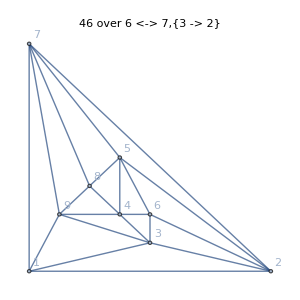
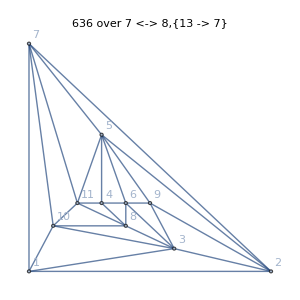
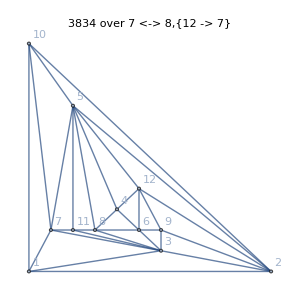
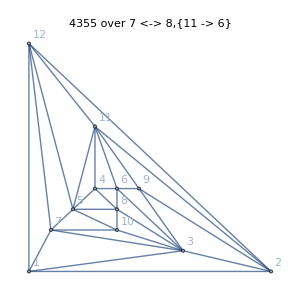
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-
-Graphics-⇒-Graphics-

```mathematica
TableForm[
Map[
Implies[
HighlightGraph[
Graph[ReadGrof[#[[1]]],PlotLabel->ToString[#[[1]]] <> " over " <> ToString[Read[StringToStream[#[[3]]]][[2]]] <> "," <> ToString[{Chrom[#[[1]]]/24->Chrom[#[[2]]]/24}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick", ImageSize->300],
Join[ReadGraphDiamondHighLights[#[[1]]],{ Style[Read[StringToStream[#[[3]]]][[2]],Thick,Dashed,Red]}]
],
HighlightGraph[
Graph[ReadGrof[#[[2]]],PlotLabel->ToString[#[[2]]] <> " over " <> ToString[Read[StringToStream[#[[3]]]][[3]]] <> "," <> ToString[{Chrom[#[[1]]]/24->Chrom[#[[2]]]/24}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick", ImageSize->300],
Join[ReadGraphDiamondHighLights[#[[2]]],{ Style[Read[StringToStream[#[[3]]]][[3]],Thick,Dashed,Red]}]
]
]&
,
Select[Take[Dalers,80],Ceiling[(Chrom[#[[1]]]/24+1)/2]==Chrom[#[[2]]]/24&]
]
]
```

```mathematica
HighlightGraph
```

```mathematica
HighlightGraph[
Graph[ReadGrof[7],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick", ImageSize->300],
{Style[ReadGraphDiamond[7],Green], Style[1<->5,Red]}
]
```

$Aborted

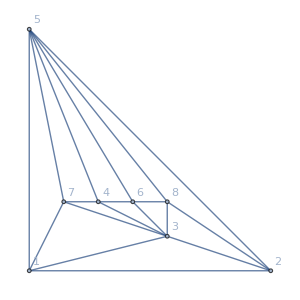

```mathematica
Graph[ReadGrof[21],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlightStyle->"Thick", ImageSize->300]
```